# Parameters & Configuration

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance

```mathematica
Omm=0.3111;
Oml=1-Omm;
H0=1/2997.9;
Lp4=4;
```

```mathematica
h=0.6766
```

0.6766

## Data imput

## Covariance Integrals

```mathematica
zsigma=Import["sigma8_CAMB.dat","Table"];
```

```mathematica
varcosmicMONObare=Import["integrals/varcosmic_mono_bare.dat","Table"];
varcosmicDIPbare=Import["integrals/varcosmic_dip_bare.dat","Table"];
varcosmicQUADbare=Import["integrals/varcosmic_quad_bare.dat","Table"];
varcosmicOCTbare=Import["integrals/varcosmic_oct_bare.dat","Table"];
varcosmicHEXAbare=Import["integrals/varcosmic_hexa_bare.dat","Table"];
varcosmic02bare=Import["integrals/varcosmic_mult02_bare.dat","Table"];
varcosmic04bare=Import["integrals/varcosmic_mult04_bare.dat","Table"];
varcosmic13bare=Import["integrals/varcosmic_mult13_bare.dat","Table"];
varcosmic24bare=Import["integrals/varcosmic_mult24_bare.dat","Table"];
varmixMONObare=Import["integrals/varmix_mono_bare.dat","Table"];
varmixDIPbare=Import["integrals/varmix_dip_bare.dat","Table"];
varmixQUADbare=Import["integrals/varmix_quad_bare.dat","Table"];
varmixOCTbare=Import["integrals/varmix_oct_bare.dat","Table"];
varmixHEXAbare=Import["integrals/varmix_hexa_bare.dat","Table"];
varmix02bare=Import["integrals/varmix_mult02_bare.dat","Table"];
varmix04bare=Import["integrals/varmix_mult04_bare.dat","Table"];
varmix13bare=Import["integrals/varmix_mult13_bare.dat","Table"];
varmix24bare=Import["integrals/varmix_mult24_bare.dat","Table"];
```

## Signals Integrals

```mathematica
nu1baretab=Import["/Users/danielsb/Documents/GitHub/magevolbias/Signals/nu1_z0_fid.dat","Table"];
```

```mathematica
nu1=Interpolation[nu1baretab];
```

```mathematica
nu1z0[d_]:=d H0 nu1[d];
```

MONOPOLE

```mathematica
mu0baretab=Import["/Users/danielsb/Documents/GitHub/magevolbias/Signals/mu0_z0_fid.dat","Table"];
```

```mathematica
mu0=Interpolation[mu0baretab];
```

```mathematica
mu0z0[d_]:= mu0[d];
```

QUADRUPOLE

```mathematica
mu2baretab=Import["/Users/danielsb/Documents/GitHub/magevolbias/Signals/mu2_z0_fid.dat","Table"];
```

```mathematica
mu2=Interpolation[mu2baretab];
```

```mathematica
mu2z0[d_]:=mu2[d];
```

OCTUPOLE

```mathematica
nu1baretab=Import["/Users/danielsb/Documents/GitHub/magevolbias/Signals/nu3_z0_fid.dat","Table"];
```

```mathematica
nu3=Interpolation[nu1baretab];
```

```mathematica
nu3z0[d_]:=d H0 nu3[d];
```

HEXADECAPOLE

```mathematica
mu4baretab=Import["/Users/danielsb/Documents/GitHub/magevolbias/Signals/mu4_z0_fid.dat","Table"];
mu4=Interpolation[mu4baretab];
mu4z0[d_]:= mu4[d];
```

```mathematica
mu0Lp4zbaretab=Table[mu0z0[d],{d,4,172,4}];
nu1Lp4zbaretab=Table[nu1z0[d],{d,4,172,4}];
mu2Lp4zbaretab=Table[mu2z0[d],{d,4,172,4}];
nu3Lp4zbaretab=Table[nu3z0[d],{d,4,172,4}];
mu4Lp4zbaretab=Table[mu4z0[d],{d,4,172,4}];
```

## Cosmology

```mathematica
r[z_]:=Integrate[1/(Sqrt[Omm x^3+Oml]),{x,1,1+z}];
```

```mathematica
r[0.15]/H0
```

433.566

```mathematica
D1[z_]:=5Omm/2(Omm(1+z)^3+1-Omm)^(1/2)NIntegrate[1/(Omm/x+(1-Omm) x^2)^(3/2),{x,0,1/(1+z)}]
```

```mathematica
fz[z_]:=1/(Omm+Oml/(1+z)^3)(-3Omm/2+5Omm/2/(1+z)/D1[z]);
```

```mathematica
HH[z_]=Sqrt[Omm(1+z)+(1-Omm)/(1+z)^2];
```

```mathematica
dD1dz[z_]:=(5 Omm /2) (3 Omm (1+z)^2/(2 Sqrt[Omm (1+z)^3 + Oml]) Integrate[(1+x)/(Sqrt[Omm(1+x)^3+Oml])^3,{x,z,Infinity}] - (1+z)/(Omm(1+z)^3+Oml))
```

```mathematica
Table[{D1[0],fz[0]},{i,1}]
```

{{0.785555,0.523414}}

```mathematica
OmegaLz[z_]:=1/(Omm (1+z)^3+Oml)
```

```mathematica
OmegaMz[z_]:= Omm (1+z)^3/(Omm(1+z)^3+Oml)
```

```mathematica
zSKA=List[0.15,0.25,0.35,0.45,0.55,0.65,0.75,0.85,0.95,1.05,1.15,1.25,1.35,1.45,1.55,1.65,1.75,1.85,1.95]; 
(* zSKA= List[0.20,0.28,0.36,0.44,0.53,0.64,0.79, 1.03, 1.31, 1.58, 1.86]; *)
```

```mathematica
ktot=Length[zSKA]
```

19

```mathematica
VzSKA=ParallelTable[4/3 Pi ( r[zSKA[[i]]+0.05]^3-r[zSKA[[i]]-0.05]^3)/H0^3 30000/41253,{i,1,ktot}];
fzSKA=ParallelTable[fz[zSKA[[i]]],{i,1,ktot}];
evolzSKA=ParallelTable[(D1[zSKA[[i]]]/D1[0])^2,{i,1,ktot}];
dzSKA=ParallelTable[r[zSKA[[i]]],{i,1,ktot}];
HzSKA=ParallelTable[HH[zSKA[[i]]],{i,1,ktot}];
dD1dzSKA=ParallelTable[dD1dz[zSKA[[i]]],{i,1,ktot}];
D1zSKA=Table[D1[i],{i,zSKA}];
D10=D1[0];
dfdzSKA=(3 Oml (1+zSKA)^2)/(Omm (1+zSKA)^3+Oml)^2 (-3 Omm/2 + 5 Omm /2 /((1+zSKA) D1zSKA)) - (5 Omm /2 )((1+zSKA)^3/(Omm(1+zSKA)^3+Oml))((D1zSKA+(1+zSKA) dD1dzSKA)/((1+zSKA)D1zSKA)^2);
rH0zSKA = r[zSKA];
```

```mathematica
VzSKA
```

{4.90045×10^8,1.20103×10^9,2.09836×10^9,3.09231×10^9,4.11482×10^9,5.11741×10^9,6.06784×10^9,6.94656×10^9,7.74333×10^9,8.45454×10^9,9.08098×10^9,9.62628×10^9,1.00957×10^10,1.04954×10^10,1.08317×10^10,1.11109×10^10,1.13393×10^10,1.15223×10^10,1.16654×10^10}

```mathematica
D1zSKA
```

{0.725792,0.688431,0.653295,0.620452,0.589882,0.561505,0.535207,0.510852,0.488297,0.467398,0.448017,0.430022,0.413292,0.397715,0.383189,0.369621,0.356928,0.345034,0.333872}

```mathematica
OmegaMzSKA=OmegaMz[zSKA]
```

{0.407165,0.468653,0.526309,0.579253,0.627097,0.669814,0.707623,0.740885,0.770035,0.795522,0.817786,0.837237,0.854242,0.869129,0.882186,0.893661,0.903769,0.912694,0.920593}

```mathematica
OmegaLzSKA=OmegaLz[zSKA]
```

{0.860552,0.771297,0.687605,0.610751,0.541302,0.479294,0.424412,0.376128,0.333815,0.296818,0.264499,0.236266,0.211581,0.18997,0.171017,0.15436,0.139688,0.126733,0.115266}

```mathematica
dOmegaLzSKA=- 3 Omm (1+zSKA)^2/(Omm(1+zSKA)^3+Oml)^2
```

{-0.914054,-0.86753,-0.804206,-0.731958,-0.656998,-0.583706,-0.51484,-0.451894,-0.395461,-0.345549,-0.301819,-0.263747,-0.230734,-0.202174,-0.177493,-0.156165,-0.137723,-0.121756,-0.107912}

```mathematica
b1=0.554;
b2=0.783;
bmeanzSKA=b1 Exp[b2 zSKA];
```

```mathematica
db=1.0;
dbz=Table[db,{i,Length[zSKA]}];
bBzSKA=bmeanzSKA+dbz/2;
bFzSKA=bmeanzSKA-dbz/2;
bTzSKA=(bBzSKA+bFzSKA)/2;
```

```mathematica
bBzSKA
```

{1.12304,1.17379,1.22867,1.28801,1.35219,1.4216,1.49666,1.57784,1.66563,1.76056,1.86323,1.97426,2.09434,2.22419,2.36462,2.51649,2.68073,2.85834,3.05042}

```mathematica
bFzSKA
```

{0.123042,0.173787,0.228665,0.288013,0.352194,0.421603,0.496665,0.57784,0.665627,0.760564,0.863233,0.974265,1.09434,1.22419,1.36462,1.51649,1.68073,1.85834,2.05042}

```mathematica
bB0=b1+db/2
bF0=b1-db/2
```

1.054

0.054

```mathematica
b1B=b1;
b1F=b1;
b2B=b2;
b2F=b2;
```

```mathematica
b1B
```

0.554

Import CAMB results

```mathematica
Length[zsigma]
```

100

Redshift is displayed in the wrong order in zsigma. σ8 is given i

```mathematica
sigma8ztab=zsigma[[All,2]];
```

```mathematica
redshifts=zsigma[[All,1]];
```

```mathematica
zsigma8tab=Table[{redshifts[[i]],sigma8ztab[[i]]},{i,1,Length[redshifts]}];
```

```mathematica
sigma8z=Interpolation[zsigma8tab];
```

```mathematica
Sigma8z0=sigma8z[0]
```

0.814468

```mathematica
sigma8z[0]*D1[0.5]/D1[0]
```

0.627151

```mathematica
sigma8z[0.5]
```

0.627168

```mathematica
Sigma8zSKA=sigma8z[zSKA];
```

Need of fevolB and fevolF

```mathematica
bBtildezSKA=bBzSKA D1zSKA Sigma8z0/D10
bFtildezSKA=bFzSKA D1zSKA Sigma8z0/D10
```

{0.845096,0.837813,0.832225,0.828564,0.826993,0.827618,0.830509,0.835711,0.843256,0.853172,0.865485,0.880225,0.897432,0.917153,0.939447,0.964384,0.992045,1.02253,1.05594}

{0.0925901,0.124044,0.154884,0.185276,0.2154,0.245446,0.275603,0.306056,0.336987,0.368571,0.400978,0.434376,0.468928,0.5048,0.542155,0.581158,0.62198,0.664792,0.709776}

```mathematica
bBtildezSKA-bFtildezSKA
```

{0.752505,0.713769,0.677341,0.643289,0.611593,0.582172,0.554906,0.529655,0.50627,0.484602,0.464507,0.44585,0.428504,0.412353,0.397292,0.383225,0.370065,0.357734,0.346161}

```mathematica
(bBtildezSKA+bFtildezSKA)/2
```

{0.468843,0.480929,0.493555,0.50692,0.521196,0.536532,0.553056,0.570883,0.590122,0.610871,0.633231,0.6573,0.68318,0.710977,0.740801,0.772771,0.807012,0.843659,0.882856}

# Multi-SPLIT Covariance

## Covariance Blocks

## Parameters

### Galaxy bias

```mathematica
b1=0.554;
b2=0.783;
bmeanzSKA=b1 Exp[b2 zSKA];
```

```mathematica
bB[m_, dbz_]:=bmeanzSKA+(m-1)dbz/m ;
bF[m_, dbz_]:=bmeanzSKA-dbz/m;
bT[m_,dbz_]:=bmeanzSKA ;
```

#### Standard splitting 50% (m = 2)

```mathematica
m = 2;
```

```mathematica
db=1.0;
dbz=Table[db,{i,Length[zSKA]}];
```

```mathematica
bBzSKA50=bB[2, dbz]
```

{1.12304,1.17379,1.22867,1.28801,1.35219,1.4216,1.49666,1.57784,1.66563,1.76056,1.86323,1.97426,2.09434,2.22419,2.36462,2.51649,2.68073,2.85834,3.05042}

```mathematica
bFzSKA50=bF[2,dbz]
```

{0.123042,0.173787,0.228665,0.288013,0.352194,0.421603,0.496665,0.57784,0.665627,0.760564,0.863233,0.974265,1.09434,1.22419,1.36462,1.51649,1.68073,1.85834,2.05042}

```mathematica
bTzSKA50 = bT[2,dbz]
```

{0.623042,0.673787,0.728665,0.788013,0.852194,0.921603,0.996665,1.07784,1.16563,1.26056,1.36323,1.47426,1.59434,1.72419,1.86462,2.01649,2.18073,2.35834,2.55042}

BRIGHT

```mathematica
nBSKA50 = 1/2;
```

```mathematica
smodelBzSKA50 = List[0.22441708,0.35788955,0.47077869,0.54038551,0.60761985,0.67991981,0.7531311,0.81864417,0.88081715,0.94857743,1.02785004,1.12008456,1.21930805,1.32187692,1.42534363,1.52897325,1.63180455,1.73334715,1.83420913];
```

```mathematica
fevolBzSKA50 = List[3.00956639,0.07976877,-0.81552783,-0.6173486,-0.39242556,-0.31155665,-0.26595514,-0.1091582,0.07791229,0.18253319,0.17336397,0.03980399,-0.12308668,-0.28681099,-0.41997146,-0.51728093,-0.57341237,-0.57764042,-0.55234844];
```

FAINT

```mathematica
nFSKA50 = 1/2;
```

```mathematica
smodelzSKA50 = List[0.10126775,0.16794581,0.24591785,0.34042118,0.44359672,0.54749941,0.64724732,0.74425817,0.83940737,0.93348225,1.02841809,1.12429914,1.2228487,1.3231631,1.42622787,1.53202081,1.64045919,1.75174659,1.86291714];
```

```mathematica
(*Check if'm' exists and if it's equal to a desired value*)
If[!ValueQ[m]||m!=2,m=1/(1-nFSKA50);]
```

```mathematica
m
```

2

```mathematica
smodelFzSKA50 = (m/(m-1)) smodelzSKA50 -(1/(m-1)) smodelBzSKA50
```

{-0.0218816,-0.0219979,0.021057,0.140457,0.279574,0.415079,0.541364,0.669872,0.797998,0.918387,1.02899,1.12851,1.22639,1.32445,1.42711,1.53507,1.64911,1.77015,1.89163}

```mathematica
fevolFzSKA50 = List[1.49669846,4.74321837,4.48561914,3.00325909,1.42466759,0.23953114,-0.63019961,-1.38888192,-2.01572455,-2.47043394,-2.7319998,-2.83059041,-2.87381247,-2.89939059,-2.94565432,-3.01777315,-3.12068025,-3.25274921,-3.36209773];
```

#### Splitting with 10% Bright (m=10)

```mathematica
m=10;
```

```mathematica
db=1.4;
dbz=Table[db,{i,Length[zSKA]}];
```

```mathematica
bBzSKA30=bB[10, dbz]
```

{1.88304,1.93379,1.98867,2.04801,2.11219,2.1816,2.25666,2.33784,2.42563,2.52056,2.62323,2.73426,2.85434,2.98419,3.12462,3.27649,3.44073,3.61834,3.81042}

```mathematica
bFzSKA30=bF[10,dbz]
```

{0.483042,0.533787,0.588665,0.648013,0.712194,0.781603,0.856665,0.93784,1.02563,1.12056,1.22323,1.33426,1.45434,1.58419,1.72462,1.87649,2.04073,2.21834,2.41042}

```mathematica
bTzSKA30 = bT[10,dbz]
```

{0.623042,0.673787,0.728665,0.788013,0.852194,0.921603,0.996665,1.07784,1.16563,1.26056,1.36323,1.47426,1.59434,1.72419,1.86462,2.01649,2.18073,2.35834,2.55042}

BRIGHT

```mathematica
nBSKA30 = 1/10;
```

```mathematica
smodelBzSKA30 = List[1.03913831,0.71999785,0.70016622,0.80291617,0.80509085,0.86385634,0.93133131,0.99350429,1.04896737,1.0983242,1.14410701,1.18703114,1.23676623,1.29877001,1.36750798,1.44075302,1.51593195,1.59199958,1.66844103];
```

```mathematica
fevolBzSKA30 = List[-24.02362577,1.23631355,-1.68886235,-1.2314607,-0.25657339,-0.01563204,0.06640555,0.27155143,0.57179683,0.94187865,1.35648053,1.79696626,2.16686823,2.40966479,2.59808125,2.75955326,2.92184145,3.10220004,3.29514781];
```

FAINT

```mathematica
nFSKA30 = 9/10;
```

```mathematica
smodelzSKA30 = List[0.10126775,0.16794581,0.24591785,0.34042118,0.44359672,0.54749941,0.64724732,0.74425817,0.83940737,0.93348225,1.02841809,1.12429914,1.2228487,1.3231631,1.42622787,1.53202081,1.64045919,1.75174659,1.86291714];
```

```mathematica
(*Check if'm' exists and if it's equal to a desired value*)
If[!ValueQ[m]||m!=3,m=1/(1-nFSKA30);]
m
```

10

```mathematica
smodelFzSKA30 = (m/(m-1)) smodelzSKA30 -(1/(m-1)) smodelBzSKA30
```

{-0.00294009,0.106607,0.195446,0.289033,0.403431,0.512349,0.615682,0.716564,0.816123,0.915166,1.01556,1.11733,1.2213,1.32587,1.43275,1.54216,1.6543,1.7695,1.88453}

```mathematica
fevolFzSKA30 = List[5.17277222,2.54206913,2.22659099,1.46233479,0.60197595,-0.03827728,-0.50524214,-0.86241689,-1.14009535,-1.37570916,-1.57218441,-1.75009982,-1.90570711,-2.03785252,-2.15846779,-2.27053596,-2.37692272,-2.47268313,-2.54081985];
```

### Survey

```mathematica
Redshift = List[0.15,0.25,0.35,0.45,0.55,0.65,0.75,0.85,0.95,1.05,1.15,1.25,1.35,1.45,1.55,1.65,1.75,1.85,1.95];
```

```mathematica
NbarzSKAlist=List[6.2 10^-2/h^3,3.63 10^-2/h^3,2.16 10^-2/h^3,1.31 10^-2/h^3,8.07 10^-3/h^3,5.11 10^-3/h^3,3.27 10^-3/h^3,2.11 10^-3/h^3,1.36 10^-3/h^3,8.7 10^-4/h^3,5.56 10^-4/h^3,3.53 10^-4/h^3,2.22 10^-4/h^3,1.39 10^-4/h^3,8.55 10^-5/h^3,5.2 10^-5/h^3,3.12 10^-5/h^3,1.83 10^-5/h^3,1.05 10^-5/h^3];
Table[{Redshift[[i]], NbarzSKAlist[[i]]}, {i,1,Length[NbarzSKAlist]}]
```

{{0.15,0.200168},{0.25,0.117195},{0.35,0.0697361},{0.45,0.0422937},{0.55,0.0260542},{0.65,0.0164978},{0.75,0.0105573},{0.85,0.00681219},{0.95,0.00439079},{1.05,0.00280882},{1.15,0.00179506},{1.25,0.00113967},{1.35,0.000716732},{1.45,0.000448765},{1.55,0.000276039},{1.65,0.000167883},{1.75,0.00010073},{1.85,0.000059082},{1.95,0.0000338995}}

```mathematica
NbarzSKAfint= Interpolation[Table[{Redshift[[i]], NbarzSKAlist[[i]]}, {i,1,Length[NbarzSKAlist]}]];
NbarzSKA = NbarzSKAfint[zSKA]
```

{0.200168,0.117195,0.0697361,0.0422937,0.0260542,0.0164978,0.0105573,0.00681219,0.00439079,0.00280882,0.00179506,0.00113967,0.000716732,0.000448765,0.000276039,0.000167883,0.00010073,0.000059082,0.0000338995}

```mathematica
NtotSKA=Sum[NbarzSKA[[k]]VzSKA[[k]],{k,1,Length[zSKA]}]
```

9.23016×10^8

```mathematica
nBzSKA50=Table[nBSKA50, {i,Length[zSKA]}];
nFzSKA50=Table[nFSKA50, {i,Length[zSKA]}];
nBzSKA30=Table[nBSKA30, {i,Length[zSKA]}];
nFzSKA30=Table[nFSKA30, {i,Length[zSKA]}];
```

```mathematica
nBzSKA50
```

{1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2}

```mathematica
nFzSKA50
```

{1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2}

```mathematica
nBzSKA30
```

{1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10}

```mathematica
nFzSKA30
```

{9/10,9/10,9/10,9/10,9/10,9/10,9/10,9/10,9/10,9/10,9/10,9/10,9/10,9/10,9/10,9/10,9/10,9/10,9/10}

```mathematica
NbarBzSKA50=NbarzSKA*nBzSKA50
```

{0.100084,0.0585977,0.0348681,0.0211468,0.0130271,0.00824888,0.00527864,0.00340609,0.0021954,0.00140441,0.00089753,0.000569834,0.000358366,0.000224382,0.000138019,0.0000839416,0.000050365,0.000029541,0.0000169498}

```mathematica
NbarFzSKA50=NbarzSKA*nFzSKA50
```

{0.100084,0.0585977,0.0348681,0.0211468,0.0130271,0.00824888,0.00527864,0.00340609,0.0021954,0.00140441,0.00089753,0.000569834,0.000358366,0.000224382,0.000138019,0.0000839416,0.000050365,0.000029541,0.0000169498}

```mathematica
NbarBzSKA30=NbarzSKA*nBzSKA30
```

{0.0200168,0.0117195,0.00697361,0.00422937,0.00260542,0.00164978,0.00105573,0.000681219,0.000439079,0.000280882,0.000179506,0.000113967,0.0000716732,0.0000448765,0.0000276039,0.0000167883,0.000010073,5.9082×10^-6,3.38995×10^-6}

```mathematica
NbarFzSKA30=NbarzSKA*nFzSKA30
```

{0.180152,0.105476,0.0627625,0.0380643,0.0234488,0.014848,0.00950155,0.00613097,0.00395171,0.00252793,0.00161555,0.0010257,0.000645059,0.000403888,0.000248435,0.000151095,0.000090657,0.0000531738,0.0000305096}

Coefficient for the mixed terms

```mathematica
coeff2popSKA=(evolzSKA/(VzSKA*NbarzSKA))
```

{8.70241×10^-9,5.45636×10^-9,4.72637×10^-9,4.76986×10^-9,5.25955×10^-9,6.05173×10^-9,7.2461×10^-9,8.93679×10^-9,1.13643×10^-8,1.49076×10^-8,1.99537×10^-8,2.73143×10^-8,3.82531×10^-8,5.44219×10^-8,7.95805×10^-8,1.18687×10^-7,1.80744×10^-7,2.83384×10^-7,4.56788×10^-7}

```mathematica
coeffBSKA50=evolzSKA/(VzSKA*NbarzSKA)
```

{8.70241×10^-9,5.45636×10^-9,4.72637×10^-9,4.76986×10^-9,5.25955×10^-9,6.05173×10^-9,7.2461×10^-9,8.93679×10^-9,1.13643×10^-8,1.49076×10^-8,1.99537×10^-8,2.73143×10^-8,3.82531×10^-8,5.44219×10^-8,7.95805×10^-8,1.18687×10^-7,1.80744×10^-7,2.83384×10^-7,4.56788×10^-7}

```mathematica
coeffBSKA50/nBzSKA50
```

{1.74048×10^-8,1.09127×10^-8,9.45275×10^-9,9.53971×10^-9,1.05191×10^-8,1.21035×10^-8,1.44922×10^-8,1.78736×10^-8,2.27287×10^-8,2.98152×10^-8,3.99075×10^-8,5.46287×10^-8,7.65062×10^-8,1.08844×10^-7,1.59161×10^-7,2.37373×10^-7,3.61488×10^-7,5.66768×10^-7,9.13575×10^-7}

```mathematica
coeffFSKA50=evolzSKA/(VzSKA*NbarzSKA)
```

{8.70241×10^-9,5.45636×10^-9,4.72637×10^-9,4.76986×10^-9,5.25955×10^-9,6.05173×10^-9,7.2461×10^-9,8.93679×10^-9,1.13643×10^-8,1.49076×10^-8,1.99537×10^-8,2.73143×10^-8,3.82531×10^-8,5.44219×10^-8,7.95805×10^-8,1.18687×10^-7,1.80744×10^-7,2.83384×10^-7,4.56788×10^-7}

```mathematica
coeffFSKA50/nFzSKA50
```

{1.74048×10^-8,1.09127×10^-8,9.45275×10^-9,9.53971×10^-9,1.05191×10^-8,1.21035×10^-8,1.44922×10^-8,1.78736×10^-8,2.27287×10^-8,2.98152×10^-8,3.99075×10^-8,5.46287×10^-8,7.65062×10^-8,1.08844×10^-7,1.59161×10^-7,2.37373×10^-7,3.61488×10^-7,5.66768×10^-7,9.13575×10^-7}

```mathematica
coeffBSKA30=evolzSKA/(VzSKA*NbarzSKA)
```

{8.70241×10^-9,5.45636×10^-9,4.72637×10^-9,4.76986×10^-9,5.25955×10^-9,6.05173×10^-9,7.2461×10^-9,8.93679×10^-9,1.13643×10^-8,1.49076×10^-8,1.99537×10^-8,2.73143×10^-8,3.82531×10^-8,5.44219×10^-8,7.95805×10^-8,1.18687×10^-7,1.80744×10^-7,2.83384×10^-7,4.56788×10^-7}

```mathematica
coeffBSKA30/nBzSKA30
```

{8.70241×10^-8,5.45636×10^-8,4.72637×10^-8,4.76986×10^-8,5.25955×10^-8,6.05173×10^-8,7.2461×10^-8,8.93679×10^-8,1.13643×10^-7,1.49076×10^-7,1.99537×10^-7,2.73143×10^-7,3.82531×10^-7,5.44219×10^-7,7.95805×10^-7,1.18687×10^-6,1.80744×10^-6,2.83384×10^-6,4.56788×10^-6}

```mathematica
coeffFSKA30=evolzSKA/(VzSKA*NbarzSKA)
```

{8.70241×10^-9,5.45636×10^-9,4.72637×10^-9,4.76986×10^-9,5.25955×10^-9,6.05173×10^-9,7.2461×10^-9,8.93679×10^-9,1.13643×10^-8,1.49076×10^-8,1.99537×10^-8,2.73143×10^-8,3.82531×10^-8,5.44219×10^-8,7.95805×10^-8,1.18687×10^-7,1.80744×10^-7,2.83384×10^-7,4.56788×10^-7}

```mathematica
coeffFSKA30/nFzSKA30
```

{9.66934×10^-9,6.06263×10^-9,5.25153×10^-9,5.29984×10^-9,5.84395×10^-9,6.72415×10^-9,8.05123×10^-9,9.92976×10^-9,1.26271×10^-8,1.6564×10^-8,2.21708×10^-8,3.03493×10^-8,4.25035×10^-8,6.04688×10^-8,8.84228×10^-8,1.31874×10^-7,2.00827×10^-7,3.14871×10^-7,5.07542×10^-7}

Coefficients for the Cosmic Variance

```mathematica
coeffCCSKA=evolzSKA^2/VzSKA
```

{1.48698×10^-9,4.91113×10^-10,2.27956×10^-10,1.25847×10^-10,7.72686×10^-11,5.10105×10^-11,3.55097×10^-11,2.57457×10^-11,1.92798×10^-11,1.48236×10^-11,1.16503×10^-11,9.3282×10^-12,7.589×10^-12,6.26012×10^-12,5.22696×10^-12,4.41133×10^-12,3.75864×10^-12,3.23×10^-12,2.79714×10^-12}

Coefficients needed for the cosmic variance of the dipole from relativistic effects

```mathematica
cBzSKA50=(5smodelBzSKA50 +(2-5smodelBzSKA50)/(dzSKA HzSKA)+1/2(-Omm(1+zSKA)+2/(1+zSKA)^2(1-Omm))/HzSKA^2-fevolBzSKA50)fzSKA
```

{3.03044,1.96942,1.50533,1.08587,0.778835,0.633417,0.577577,0.500896,0.433983,0.449219,0.574176,0.83023,1.14574,1.49666,1.85103,2.19899,2.5307,2.83137,3.11887}

```mathematica
cFzSKA50=(5smodelFzSKA50 +(2-5smodelFzSKA50)/(dzSKA HzSKA)+1/2(-Omm(1+zSKA)+2/(1+zSKA)^2(1-Omm))/HzSKA^2- fevolFzSKA50)fzSKA
```

{8.73219,3.49283,1.72274,1.11051,1.14024,1.34369,1.62634,2.0112,2.43762,2.84422,3.1753,3.42655,3.6648,3.91551,4.20934,4.55135,4.94709,5.39644,5.84627}

```mathematica
cBzSKA30=(5smodelBzSKA30 +(2-5smodelBzSKA30)/(dzSKA HzSKA)+1/2(-Omm(1+zSKA)+2/(1+zSKA)^2(1-Omm))/HzSKA^2-fevolBzSKA30)fzSKA
```

{3.67453,-3.17161,0.108577,-0.235995,-0.390502,-0.404636,-0.326334,-0.320991,-0.377902,-0.489366,-0.644755,-0.830883,-0.966863,-0.992326,-0.961212,-0.89451,-0.817281,-0.746799,-0.679258}

```mathematica
cFzSKA30=(5smodelFzSKA30 +(2-5smodelFzSKA30)/(dzSKA HzSKA)+1/2(-Omm(1+zSKA)+2/(1+zSKA)^2(1-Omm))/HzSKA^2- fevolFzSKA30)fzSKA
```

{6.12652,3.38699,1.78131,1.24643,1.10954,1.14335,1.26066,1.43127,1.63733,1.88406,2.15468,2.4572,2.77995,3.11702,3.47367,3.84958,4.24514,4.65398,5.05611}

### Elements

```mathematica
indist=5;
Acc =1.0 ;
```

```mathematica
distances=Table[d,{d,4,172,4}]
```

{4,8,12,16,20,24,28,32,36,40,44,48,52,56,60,64,68,72,76,80,84,88,92,96,100,104,108,112,116,120,124,128,132,136,140,144,148,152,156,160,164,168,172}

```mathematica
Table[distances[[d]],{d,indist,Length[distances]}]
```

{20,24,28,32,36,40,44,48,52,56,60,64,68,72,76,80,84,88,92,96,100,104,108,112,116,120,124,128,132,136,140,144,148,152,156,160,164,168,172}

```mathematica
maxsep=Length[distances]-3
```

40

```mathematica
dists =Table[distances[[d]],{d,indist,maxsep}]
```

{20,24,28,32,36,40,44,48,52,56,60,64,68,72,76,80,84,88,92,96,100,104,108,112,116,120,124,128,132,136,140,144,148,152,156,160}

```mathematica
dtot =Length[dists]
```

36

```mathematica
ldist=maxsep-(indist-1)
```

36

```mathematica
8 ldist
```

288

```mathematica
ktot=Length[zSKA]
```

19

```mathematica
dmin =distances[[indist]];
dmax =  distances[[maxsep]];
```

```mathematica
{dmin, dmax}
```

{20,160}

## Multipole’s Coefficients

### Cosmic Variance

#### Definitions

```mathematica
G[n_,m_,a_,b_]:=Integrate[LegendreP[n,x]LegendreP[m,x]LegendreP[a,x]LegendreP[b,x],{x,-1,1}]
```

```mathematica
alpha0[bL_,bM_,f_]:=bL bM +(bL+bM)/3 f+f^2/5
alpha2[bL_,bM_,f_]:=2/3(bL+bM) f+4f^2/7
alpha4[bL_,bM_,f_]:=8f^2/35
```

```mathematica
coeffvarianceCC[n_,m_,bL_,bM_,bN_,bP_,f_]:=
Collect[
1/4((alpha0[bL, bN,f]alpha0[bM, bP,f]+(-1)^m alpha0[bL, bP,f]alpha0[bM, bN,f])G[n,m,0,0]+(alpha0[bL, bN,f]alpha2[bM, bP,f]+(-1)^m alpha0[bL, bP,f]alpha2[bM, bN,f])G[n,m,0,2]+(alpha0[bL, bN,f]alpha4[bM, bP,f]+(-1)^m alpha0[bL, bP,f]alpha4[bM, bN,f])G[n,m,0,4]+(alpha2[bL, bN,f]alpha0[bM, bP,f]+(-1)^m alpha2[bL, bP,f]alpha0[bM, bN,f])G[n,m,2,0]+(alpha2[bL, bN,f]alpha2[bM, bP,f]+(-1)^m alpha2[bL, bP,f]alpha2[bM, bN,f])G[n,m,2,2]+(alpha2[bL, bN,f]alpha4[bM, bP,f]+(-1)^m alpha2[bL, bP,f]alpha4[bM, bN,f])G[n,m,2,4]+(alpha4[bL, bN,f]alpha0[bM, bP,f]+(-1)^m alpha4[bL, bP,f]alpha0[bM, bN,f])G[n,m,4,0]+(alpha4[bL, bN,f]alpha2[bM, bP,f]+(-1)^m alpha4[bL, bP,f]alpha2[bM, bN,f])G[n,m,4,2]+(alpha4[bL, bN,f]alpha4[bM, bP,f]+(-1)^m alpha4[bL, bP,f]alpha4[bM, bN,f])G[n,m,4,4]),f,Simplify]
```

```mathematica
corrCC[n_,m_]:=If[n==m,1,(2n+1)(2m+1)(-1)^((m-n)/2)(-1)^(m+n)]
```

```mathematica
coeffvarCC[n_,m_,bL_,bM_,bN_,bP_,f_]:= corrCC[n,m]coeffvarianceCC[n,m,bL,bM,bN,bP,f]
```

COSMIC VARIANCE (DIPOLE)

```mathematica
alpha1[bL_,bM_,cL_,cM_,f_]:=cL(bM+3f/5)-cM(bL+3f/5)
alpha3[bL_,bM_,cL_,cM_,f_]:=2f/5(cL-cM)
```

```mathematica
coeffcovCCrel[n_,m_,bL_,bM_,bN_,bP_,cL_,cM_,cN_,cP_,f_]:=Collect[(alpha1[bL, bM,cL,cM,f]alpha1[bN, bP,cN,cP,f]G[n,m,1,1]+alpha1[bL, bM,cL,cM,f]alpha3[bN, bP,cN,cP,f]G[n,m,1,3]+alpha3[bL, bM,cL,cM,f]alpha1[bN, bP,cN,cP,f]G[n,m,3,1]+alpha3[bL, bM,cL,cM,f]alpha3[bN, bP,cN,cP,f]G[n,m,3,3]),f,Simplify]
```

```mathematica
G[1,3,3,3]
```

24/385

```mathematica
coeffvarCCrelSKAz[n_,m_,bL_,bM_,bN_,bP_,cL_,cM_,cN_,cP_,f_]:=evolzSKA^2 /VzSKA /4HzSKA^2corrCC[n,m]coeffcovCCrel[n,m,bL,bM,bN,bP,cL,cM,cN,cP,f]
```

```mathematica
varcosmicMONOzbaretab=Table[varcosmicMONObare,{i,Length[zSKA]}];
```

From 4 to 172 Mpc/h

```mathematica
varcosmicMONObare[[5,1]]
```

4.

```mathematica
varcosmicMONObare[[4,2]]
```

4.

```mathematica
varcosmicMONObare[[47,1]]
```

172.

```mathematica
varcosmicMONObare[[4,44]]
```

172.

```mathematica
4 i /. i-> 1
```

4

```mathematica
4 i /. i -> 43
```

172

```mathematica
varcosmicQUADzbaretab=Table[varcosmicQUADbare,{i,Length[zSKA]}];
```

```mathematica
varcosmicHEXAzbaretab=Table[varcosmicHEXAbare,{i,Length[zSKA]}];
```

```mathematica
varcosmic02zbaretab=Table[varcosmic02bare,{i,Length[zSKA]}];
```

```mathematica
varcosmic04zbaretab=Table[varcosmic04bare,{i,Length[zSKA]}];
```

```mathematica
varcosmic24zbaretab=Table[varcosmic24bare,{i,Length[zSKA]}];
varcosmicDIPzbaretab=Table[varcosmicDIPbare, {i,Length[zSKA]}];
varcosmicOCTzbaretab=Table[varcosmicOCTbare, {i,Length[zSKA]}];
varcosmic13zbaretab=Table[varcosmic13bare, {i,Length[zSKA]}];
```

#### Monopole

Monopole 50  - Monopole 50

```mathematica
coeffvarCCpop50pop30BzSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA50,bBzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{1.22598×10^-8,4.79069×10^-9,2.6217×10^-9,1.70215×10^-9,1.22737×10^-9,9.51313×10^-10,7.78092×10^-10,6.63953×10^-10,5.86618×10^-10,5.33813×10^-10,4.98379×10^-10,4.75984×10^-10,4.6397×10^-10,4.60731×10^-10,4.65372×10^-10,4.77513×10^-10,4.97186×10^-10,5.24781×10^-10,5.61029×10^-10}

```mathematica
coeffvarCCpop30pop50BzSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA30,bBzSKA30,bBzSKA50,bBzSKA50,fzSKA]
```

{1.22598×10^-8,4.79069×10^-9,2.6217×10^-9,1.70215×10^-9,1.22737×10^-9,9.51313×10^-10,7.78092×10^-10,6.63953×10^-10,5.86618×10^-10,5.33813×10^-10,4.98379×10^-10,4.75984×10^-10,4.6397×10^-10,4.60731×10^-10,4.65372×10^-10,4.77513×10^-10,4.97186×10^-10,5.24781×10^-10,5.61029×10^-10}

```mathematica
coeffvarCCpop50pop30FzSKA=coeffCCSKA coeffvarCC[0,0,bFzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{1.61389×10^-10,8.62239×10^-11,6.1574×10^-11,5.03891×10^-11,4.46177×10^-11,4.16325×10^-11,4.03708×10^-11,4.03531×10^-11,4.13625×10^-11,4.33202×10^-11,4.62346×10^-11,5.01789×10^-11,5.52839×10^-11,6.17386×10^-11,6.97972×10^-11,7.97904×10^-11,9.21417×10^-11,1.0739×10^-10,1.26218×10^-10}

```mathematica
coeffvarCCpop30pop50FzSKA=coeffCCSKA coeffvarCC[0,0,bFzSKA30,bFzSKA30,bFzSKA50,bFzSKA50,fzSKA]
```

{1.61389×10^-10,8.62239×10^-11,6.1574×10^-11,5.03891×10^-11,4.46177×10^-11,4.16325×10^-11,4.03708×10^-11,4.03531×10^-11,4.13625×10^-11,4.33202×10^-11,4.62346×10^-11,5.01789×10^-11,5.52839×10^-11,6.17386×10^-11,6.97972×10^-11,7.97904×10^-11,9.21417×10^-11,1.0739×10^-10,1.26218×10^-10}

```mathematica
varCCMONO50Bx30BLp4d4to172zSKA=Table[coeffvarCCpop50pop30BzSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30Bx50BLp4d4to172zSKA=Table[coeffvarCCpop30pop50BzSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCCMONO50Fx30FLp4d4to172zSKA=Table[coeffvarCCpop50pop30FzSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47},{j,2,44}];
varCCMONO30Fx50FLp4d4to172zSKA=Table[coeffvarCCpop30pop50FzSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47},{j,2,44}];
```

Monopole - 2 populations

```mathematica
coeffvarCC[0,0,bL,bM,bN,bP,f]
```

bL bM bN bP+1/3 (bL bN bP+bM bN bP+bL bM (bN+bP)) f+1/5 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2+1/7 (bL+bM+bN+bP) f^3+f^4/9

```mathematica
coeffvarCCpop50BFpop30BFzSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{1.26391×10^-9,5.88634×10^-10,3.73532×10^-10,2.75603×10^-10,2.2245×10^-10,1.90785×10^-10,1.71129×10^-10,1.59006×10^-10,1.52096×10^-10,1.49127×10^-10,1.49402×10^-10,1.52569×10^-10,1.58505×10^-10,1.67263×10^-10,1.79041×10^-10,1.94177×10^-10,2.13157×10^-10,2.36629×10^-10,2.65435×10^-10}

```mathematica
coeffvarCCpop30BFpop50BFzSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA30,bFzSKA30,bBzSKA50,bFzSKA50,fzSKA]
```

{1.26391×10^-9,5.88634×10^-10,3.73532×10^-10,2.75603×10^-10,2.2245×10^-10,1.90785×10^-10,1.71129×10^-10,1.59006×10^-10,1.52096×10^-10,1.49127×10^-10,1.49402×10^-10,1.52569×10^-10,1.58505×10^-10,1.67263×10^-10,1.79041×10^-10,1.94177×10^-10,2.13157×10^-10,2.36629×10^-10,2.65435×10^-10}

```mathematica
varCCMONO50BFx30BFLp4d4to172zSKA=Table[coeffvarCCpop50BFpop30BFzSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30BFx50BFLp4d4to172zSKA=Table[coeffvarCCpop30BFpop50BFzSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCC50Bx30BF00zSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA50,bBzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{4.29173×10^-9,1.78234×10^-9,1.02982×10^-9,7.02205×10^-10,5.29535×10^-10,4.27796×10^-10,3.63718×10^-10,3.21916×10^-10,2.94477×10^-10,2.77024×10^-10,2.67025×10^-10,2.62993×10^-10,2.64081×10^-10,2.6987×10^-10,2.80253×10^-10,2.95372×10^-10,3.15599×10^-10,3.41526×10^-10,3.73988×10^-10}

```mathematica
coeffvarCC30BFx50B00zSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA30,bFzSKA30,bBzSKA50,bBzSKA50,fzSKA]
```

{4.29173×10^-9,1.78234×10^-9,1.02982×10^-9,7.02205×10^-10,5.29535×10^-10,4.27796×10^-10,3.63718×10^-10,3.21916×10^-10,2.94477×10^-10,2.77024×10^-10,2.67025×10^-10,2.62993×10^-10,2.64081×10^-10,2.6987×10^-10,2.80253×10^-10,2.95372×10^-10,3.15599×10^-10,3.41526×10^-10,3.73988×10^-10}

```mathematica
coeffvarCC50Fx30BF00zSKA=coeffCCSKA coeffvarCC[0,0,bFzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{4.12854×10^-10,2.10478×10^-10,1.44164×10^-10,1.13607×10^-10,9.71647×10^-11,8.77724×10^-11,8.25376×10^-11,8.01056×10^-11,7.97984×10^-11,8.12802×10^-11,8.44136×10^-11,8.91924×10^-11,9.57114×10^-11,1.04155×10^-10,1.14797×10^-10,1.2801×10^-10,1.44278×10^-10,1.64222×10^-10,1.88629×10^-10}

```mathematica
coeffvarCC30BFx50F00zSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA30,bFzSKA30,bFzSKA50,bFzSKA50,fzSKA]
```

{4.12854×10^-10,2.10478×10^-10,1.44164×10^-10,1.13607×10^-10,9.71647×10^-11,8.77724×10^-11,8.25376×10^-11,8.01056×10^-11,7.97984×10^-11,8.12802×10^-11,8.44136×10^-11,8.91924×10^-11,9.57114×10^-11,1.04155×10^-10,1.14797×10^-10,1.2801×10^-10,1.44278×10^-10,1.64222×10^-10,1.88629×10^-10}

```mathematica
coeffvarCC30Bx50BF00zSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA30,bBzSKA30,bBzSKA50,bFzSKA50,fzSKA]
```

{3.40525×10^-9,1.50768×10^-9,9.13723×10^-10,6.46325×10^-10,5.01667×10^-10,4.14767×10^-10,3.59332×10^-10,3.22976×10^-10,2.99226×10^-10,2.84459×10^-10,2.76566×10^-10,2.74313×10^-10,2.77013×10^-10,2.84356×10^-10,2.96313×10^-10,3.13088×10^-10,3.35106×10^-10,3.6301×10^-10,3.97684×10^-10}

```mathematica
coeffvarCC50BFx30B00zSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA50,bFzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{3.40525×10^-9,1.50768×10^-9,9.13723×10^-10,6.46325×10^-10,5.01667×10^-10,4.14767×10^-10,3.59332×10^-10,3.22976×10^-10,2.99226×10^-10,2.84459×10^-10,2.76566×10^-10,2.74313×10^-10,2.77013×10^-10,2.84356×10^-10,2.96313×10^-10,3.13088×10^-10,3.35106×10^-10,3.6301×10^-10,3.97684×10^-10}

```mathematica
coeffvarCC30Fx50BF00zSKA=coeffCCSKA coeffvarCC[0,0,bFzSKA30,bFzSKA30,bBzSKA50,bFzSKA50,fzSKA]
```

{4.78347×10^-10,2.34173×10^-10,1.55416×10^-10,1.19444×10^-10,1.00101×10^-10,8.89192×10^-11,8.24502×10^-11,7.90786×10^-11,7.79891×10^-11,7.8766×10^-11,8.12203×10^-11,8.5309×10^-11,9.10983×10^-11,9.87473×10^-11,1.08506×10^-10,1.20722×10^-10,1.35853×10^-10,1.54491×10^-10,1.77389×10^-10}

```mathematica
coeffvarCC50BFx30F00zSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{4.78347×10^-10,2.34173×10^-10,1.55416×10^-10,1.19444×10^-10,1.00101×10^-10,8.89192×10^-11,8.24502×10^-11,7.90786×10^-11,7.79891×10^-11,7.8766×10^-11,8.12203×10^-11,8.5309×10^-11,9.10983×10^-11,9.87473×10^-11,1.08506×10^-10,1.20722×10^-10,1.35853×10^-10,1.54491×10^-10,1.77389×10^-10}

```mathematica
varCCMONO50Bx30BFLp4d4to172zSKA=Table[coeffvarCC50Bx30BF00zSKA[[k] ]varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCCMONO30BFx50BLp4d4to172zSKA=Table[coeffvarCC30BFx50B00zSKA[[k] ]varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCCMONO30Bx50BFLp4d4to172zSKA=Table[coeffvarCC30Bx50BF00zSKA[[k] ]varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCCMONO50BFx30BLp4d4to172zSKA=Table[coeffvarCC50BFx30B00zSKA[[k] ]varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varCCMONO50Fx30BFLp4d4to172zSKA= Table[coeffvarCC50Fx30BF00zSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCCMONO30BFx50FLp4d4to172zSKA= Table[coeffvarCC30BFx50F00zSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCCMONO30Fx50BFLp4d4to172zSKA= Table[coeffvarCC30Fx50BF00zSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCCMONO50BFx30FLp4d4to172zSKA= Table[coeffvarCC50BFx30F00zSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
coeffvarCCpop50Bpop30FzSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA50,bBzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{1.54402×10^-9,6.79739×10^-10,4.13586×10^-10,2.9543×10^-10,2.3243×10^-10,1.95277×10^-10,1.72229×10^-10,1.57815×10^-10,1.49219×10^-10,1.44904×10^-10,1.44019×10^-10,1.46111×10^-10,1.50993×10^-10,1.58665×10^-10,1.69285×10^-10,1.83157×10^-10,2.0073×10^-10,2.22617×10^-10,2.49619×10^-10}

```mathematica
coeffvarCCpop30Fpop50BzSKA=coeffCCSKA coeffvarCC[0,0,bFzSKA30,bFzSKA30,bBzSKA50,bBzSKA50,fzSKA]
```

{1.54402×10^-9,6.79739×10^-10,4.13586×10^-10,2.9543×10^-10,2.3243×10^-10,1.95277×10^-10,1.72229×10^-10,1.57815×10^-10,1.49219×10^-10,1.44904×10^-10,1.44019×10^-10,1.46111×10^-10,1.50993×10^-10,1.58665×10^-10,1.69285×10^-10,1.83157×10^-10,2.0073×10^-10,2.22617×10^-10,2.49619×10^-10}

```mathematica
coeffvarCCpop50Fpop30BzSKA=coeffCCSKA coeffvarCC[0,0,bFzSKA50,bFzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{1.07004×10^-9,5.20733×10^-10,3.42049×10^-10,2.59441×10^-10,2.14167×10^-10,1.87124×10^-10,1.70467×10^-10,1.60468×10^-10,1.55188×10^-10,1.53569×10^-10,1.55045×10^-10,1.59347×10^-10,1.66413×10^-10,1.7634×10^-10,1.89365×10^-10,2.05863×10^-10,2.26354×10^-10,2.51524×10^-10,2.82254×10^-10}

```mathematica
coeffvarCCpop30Bpop50FzSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA30,bBzSKA30,bFzSKA50,bFzSKA50,fzSKA]
```

{1.07004×10^-9,5.20733×10^-10,3.42049×10^-10,2.59441×10^-10,2.14167×10^-10,1.87124×10^-10,1.70467×10^-10,1.60468×10^-10,1.55188×10^-10,1.53569×10^-10,1.55045×10^-10,1.59347×10^-10,1.66413×10^-10,1.7634×10^-10,1.89365×10^-10,2.05863×10^-10,2.26354×10^-10,2.51524×10^-10,2.82254×10^-10}

```mathematica
varCCMONO50Bx30FLp4d4to172zSKA=Table[coeffvarCCpop50Bpop30FzSKA[[k] ]varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCCMONO30Fx50BLp4d4to172zSKA=Table[coeffvarCCpop30Fpop50BzSKA[[k] ]varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCCMONO30Bx50FLp4d4to172zSKA=Table[coeffvarCCpop30Bpop50FzSKA[[k] ]varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCCMONO50Fx30BLp4d4to172zSKA=Table[coeffvarCCpop50Fpop30BzSKA[[k] ]varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

#### Dipole

```mathematica
coeffcovCCrel[1,1,bL,bM,bN,bP,cL,cM,cN,cP,f]
```

2/5 (bM cL-bL cM) (bP cN-bN cP)-2/7 (bL cM cN+bP (-cL+cM) cN+bN cL cP-bL cM cP-bN cM cP+bM cL (-cN+cP)) f+2/9 (cL-cM) (cN-cP) f^2

```mathematica
Simplify[Collect[coeffcovCCrel[1,1,bN,bP,bL,bM,cN,cP,cL,cM,f]-coeffcovCCrel[1,1,bL,bM,bN,bP,cL,cM,cN,cP,f],f]]
```

0

```mathematica
coeffvarCC50BFx30BFrelzSKA=coeffvarCCrelSKAz[1,1,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,cBzSKA50,cFzSKA50,cBzSKA30,cFzSKA30,fzSKA]
```

{1.68847×10^-8,2.07335×10^-9,1.47929×10^-10,3.8681×10^-11,3.01744×10^-11,2.97676×10^-11,3.085×10^-11,3.59554×10^-11,4.28888×10^-11,5.00898×10^-11,5.58296×10^-11,5.9576×10^-11,6.20823×10^-11,6.34683×10^-11,6.56399×10^-11,6.91688×10^-11,7.47504×10^-11,8.29899×10^-11,9.2231×10^-11}

```mathematica
coeffvarCC30BFx50BFrelzSKA=coeffvarCCrelSKAz[1,1,bBzSKA30,bFzSKA30,bBzSKA50,bFzSKA50,cBzSKA30,cFzSKA30,cBzSKA50,cFzSKA50,fzSKA]
```

{1.68847×10^-8,2.07335×10^-9,1.47929×10^-10,3.8681×10^-11,3.01744×10^-11,2.97676×10^-11,3.085×10^-11,3.59554×10^-11,4.28888×10^-11,5.00898×10^-11,5.58296×10^-11,5.9576×10^-11,6.20823×10^-11,6.34683×10^-11,6.56399×10^-11,6.91688×10^-11,7.47504×10^-11,8.29899×10^-11,9.2231×10^-11}

```mathematica
varCCDIP50BFx30BFrelLp4d4to172zSKA=Table[coeffvarCC50BFx30BFrelzSKA[[k]] varcosmicDIPzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCDIP30BFx50BFrelLp4d4to172zSKA=Table[coeffvarCC30BFx50BFrelzSKA[[k]] varcosmicDIPzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Quadrupole

```mathematica
coeffvarCC22=coeffvarCC[2,2,bL,bM,bN,bP,f]
```

1/5 bL bM bN bP+11/105 (bL bN bP+bM bN bP+bL bM (bN+bP)) f+3/35 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2+17/231 (bL+bM+bN+bP) f^3+(83 f^4)/1287

Cuadrupole - 1 Population

```mathematica
coeffvarCCpop50pop3022BzSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA50,bBzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{3.32412×10^-9,1.31332×10^-9,7.23829×10^-10,4.71693×10^-10,3.40396×10^-10,2.63405×10^-10,2.14653×10^-10,1.82186×10^-10,1.59884×10^-10,1.44352×10^-10,1.33594×10^-10,1.26388×10^-10,1.2197×10^-10,1.19865×10^-10,1.19786×10^-10,1.21586×10^-10,1.25223×10^-10,1.30742×10^-10,1.38273×10^-10}

```mathematica
coeffvarCCpop50pop3022FzSKA=coeffCCSKA coeffvarCC[2,2,bFzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{7.39588×10^-11,3.83829×10^-11,2.66362×10^-11,2.11764×10^-11,1.82055×10^-11,1.6482×10^-11,1.54975×10^-11,1.50137×10^-11,1.49117×10^-11,1.51325×10^-11,1.56526×10^-11,1.64717×10^-11,1.76076×10^-11,1.90949×10^-11,2.09843×10^-11,2.3345×10^-11,2.62675×10^-11,2.98679×10^-11,3.42939×10^-11}

```mathematica
coeffvarCCpop30pop5022BzSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA30,bBzSKA30,bBzSKA50,bBzSKA50,fzSKA]
```

{3.32412×10^-9,1.31332×10^-9,7.23829×10^-10,4.71693×10^-10,3.40396×10^-10,2.63405×10^-10,2.14653×10^-10,1.82186×10^-10,1.59884×10^-10,1.44352×10^-10,1.33594×10^-10,1.26388×10^-10,1.2197×10^-10,1.19865×10^-10,1.19786×10^-10,1.21586×10^-10,1.25223×10^-10,1.30742×10^-10,1.38273×10^-10}

```mathematica
coeffvarCCpop30pop5022FzSKA=coeffCCSKA coeffvarCC[2,2,bFzSKA30,bFzSKA30,bFzSKA50,bFzSKA50,fzSKA]
```

{7.39588×10^-11,3.83829×10^-11,2.66362×10^-11,2.11764×10^-11,1.82055×10^-11,1.6482×10^-11,1.54975×10^-11,1.50137×10^-11,1.49117×10^-11,1.51325×10^-11,1.56526×10^-11,1.64717×10^-11,1.76076×10^-11,1.90949×10^-11,2.09843×10^-11,2.3345×10^-11,2.62675×10^-11,2.98679×10^-11,3.42939×10^-11}

```mathematica
varCCQUAD50Bx30BLp4d4to172zSKA= Table[coeffvarCCpop50pop3022BzSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD30Bx50BLp4d4to172zSKA= Table[coeffvarCCpop30pop5022BzSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCCQUAD50Fx30FLp4d4to172zSKA= Table[coeffvarCCpop50pop3022FzSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD30Fx50FLp4d4to172zSKA= Table[coeffvarCCpop30pop5022FzSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCCpop50Bpop30F22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA50,bBzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{5.18384×10^-10,2.28369×10^-10,1.38446×10^-10,9.81858×10^-11,7.6472×10^-11,6.34533×10^-11,5.51674×10^-11,4.97569×10^-11,4.62562×10^-11,4.41278×10^-11,4.30619×10^-11,4.28806×10^-11,4.34895×10^-11,4.48523×10^-11,4.69774×10^-11,4.99117×10^-11,5.3739×10^-11,5.85816×10^-11,6.46044×10^-11}

```mathematica
coeffvarCCpop30Bpop50F22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA30,bBzSKA30,bFzSKA50,bFzSKA50,fzSKA]
```

{4.28381×10^-10,2.01911×10^-10,1.28787×10^-10,9.49892×10^-11,7.63106×10^-11,6.49189×10^-11,5.76042×10^-11,5.28366×10^-11,4.98104×10^-11,4.80732×10^-11,4.73641×10^-11,4.75359×10^-11,4.8515×10^-11,5.02811×10^-11,5.28559×10^-11,5.6299×10^-11,6.07067×10^-11,6.62151×10^-11,7.30043×10^-11}

```mathematica
coeffvarCCpop50Fpop30B22zSKA=coeffCCSKA coeffvarCC[2,2,bFzSKA50,bFzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{4.28381×10^-10,2.01911×10^-10,1.28787×10^-10,9.49892×10^-11,7.63106×10^-11,6.49189×10^-11,5.76042×10^-11,5.28366×10^-11,4.98104×10^-11,4.80732×10^-11,4.73641×10^-11,4.75359×10^-11,4.8515×10^-11,5.02811×10^-11,5.28559×10^-11,5.6299×10^-11,6.07067×10^-11,6.62151×10^-11,7.30043×10^-11}

```mathematica
coeffvarCCpop30Fpop50B22zSKA=coeffCCSKA coeffvarCC[2,2,bFzSKA30,bFzSKA30,bBzSKA50,bBzSKA50,fzSKA]
```

{5.18384×10^-10,2.28369×10^-10,1.38446×10^-10,9.81858×10^-11,7.6472×10^-11,6.34533×10^-11,5.51674×10^-11,4.97569×10^-11,4.62562×10^-11,4.41278×10^-11,4.30619×10^-11,4.28806×10^-11,4.34895×10^-11,4.48523×10^-11,4.69774×10^-11,4.99117×10^-11,5.3739×10^-11,5.85816×10^-11,6.46044×10^-11}

```mathematica
varCCQUAD50Bx30FLp4d4to172zSKA= Table[coeffvarCCpop50Bpop30F22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD30Bx50FLp4d4to172zSKA= Table[coeffvarCCpop30Bpop50F22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCCQUAD50Fx30BLp4d4to172zSKA= Table[coeffvarCCpop50Fpop30B22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD30Fx50BLp4d4to172zSKA= Table[coeffvarCCpop30Fpop50B22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Cuadrupole - 2 populations

```mathematica
coeffvarCC[2,2,bL,bM,bN,bP,f]
```

1/5 bL bM bN bP+11/105 (bL bN bP+bM bN bP+bL bM (bN+bP)) f+3/35 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2+17/231 (bL+bM+bN+bP) f^3+(83 f^4)/1287

```mathematica
coeffvarCCpop50BFpop30BF22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{4.67031×10^-10,2.13472×10^-10,1.33003×10^-10,9.63161×10^-11,7.62521×10^-11,6.41023×10^-11,5.63253×10^-11,5.12449×10^-11,4.79827×10^-11,4.60473×10^-11,4.51551×10^-11,4.51442×10^-11,4.59312×10^-11,4.74878×10^-11,4.98293×10^-11,5.30089×10^-11,5.71166×10^-11,6.22814×10^-11,6.8676×10^-11}

```mathematica
coeffvarCCpop30BFpop50BF22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA30,bFzSKA30,bBzSKA50,bFzSKA50,fzSKA]
```

{4.67031×10^-10,2.13472×10^-10,1.33003×10^-10,9.63161×10^-11,7.62521×10^-11,6.41023×10^-11,5.63253×10^-11,5.12449×10^-11,4.79827×10^-11,4.60473×10^-11,4.51551×10^-11,4.51442×10^-11,4.59312×10^-11,4.74878×10^-11,4.98293×10^-11,5.30089×10^-11,5.71166×10^-11,6.22814×10^-11,6.8676×10^-11}

```mathematica
varCCQUAD50BFx30BFLp4d4to172zSKA=Table[coeffvarCCpop50BFpop30BF22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD30BFx50BFLp4d4to172zSKA=Table[coeffvarCCpop30BFpop50BF22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCC50Bx30BF22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA50,bBzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{1.29862×10^-9,5.42384×10^-10,3.13844×10^-10,2.13563×10^-10,1.60249×10^-10,1.28511×10^-10,1.0825×10^-10,9.47739×10^-11,8.56549×10^-11,7.95366×10^-11,7.56223×10^-11,7.34312×10^-11,7.26747×10^-11,7.31894×10^-11,7.49005×10^-11,7.78021×10^-11,8.19463×10^-11,8.74405×10^-11,9.44478×10^-11}

```mathematica
coeffvarCC30BFx50B22zSKA =coeffCCSKA coeffvarCC[2,2,bBzSKA30,bFzSKA30,bBzSKA50,bBzSKA50,fzSKA]
```

{1.29862×10^-9,5.42384×10^-10,3.13844×10^-10,2.13563×10^-10,1.60249×10^-10,1.28511×10^-10,1.0825×10^-10,9.47739×10^-11,8.56549×10^-11,7.95366×10^-11,7.56223×10^-11,7.34312×10^-11,7.26747×10^-11,7.31894×10^-11,7.49005×10^-11,7.78021×10^-11,8.19463×10^-11,8.74405×10^-11,9.44478×10^-11}

```mathematica
coeffvarCC50Fx30BF22zSKA=coeffCCSKA coeffvarCC[2,2,bFzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{1.7759×10^-10,8.78086×10^-11,5.84091×10^-11,4.47226×10^-11,3.71659×10^-11,3.26179×10^-11,2.97961×10^-11,2.80912×10^-11,2.71864×10^-11,2.69101×10^-11,2.71716×10^-11,2.79297×10^-11,2.91788×10^-11,3.09406×10^-11,3.32618×10^-11,3.62141×10^-11,3.9896×10^-11,4.44371×10^-11,5.00039×10^-11}

```mathematica
coeffvarCC30BFx50F22zSKA =coeffCCSKA coeffvarCC[2,2,bBzSKA30,bFzSKA30,bFzSKA50,bFzSKA50,fzSKA]
```

{1.7759×10^-10,8.78086×10^-11,5.84091×10^-11,4.47226×10^-11,3.71659×10^-11,3.26179×10^-11,2.97961×10^-11,2.80912×10^-11,2.71864×10^-11,2.69101×10^-11,2.71716×10^-11,2.79297×10^-11,2.91788×10^-11,3.09406×10^-11,3.32618×10^-11,3.62141×10^-11,3.9896×10^-11,4.44371×10^-11,5.00039×10^-11}

```mathematica
varCCQUAD50Bx30BFLp4d4to172zSKA=Table[coeffvarCC50Bx30BF22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD50Fx30BFLp4d4to172zSKA=Table[coeffvarCC50Fx30BF22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD30BFx50BLp4d4to172zSKA=Table[coeffvarCC30BFx50B22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD30BFx50FLp4d4to172zSKA=Table[coeffvarCC30BFx50F22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCC30Bx50BF22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA30,bBzSKA30,bBzSKA50,bFzSKA50,fzSKA]
```

{1.14678×10^-9,4.99315×10^-10,2.97976×10^-10,2.07595×10^-10,1.58663×10^-10,1.29117×10^-10,1.10058×10^-10,9.72952×10^-11,8.86368×10^-11,8.28465×10^-11,7.91931×10^-11,7.7234×10^-11,7.67039×10^-11,7.74551×10^-11,7.94246×10^-11,8.26156×10^-11,8.70888×10^-11,9.29597×10^-11,1.004×10^-10}

```mathematica
coeffvarCC50BFx30B22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA50,bFzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{1.14678×10^-9,4.99315×10^-10,2.97976×10^-10,2.07595×10^-10,1.58663×10^-10,1.29117×10^-10,1.10058×10^-10,9.72952×10^-11,8.86368×10^-11,8.28465×10^-11,7.91931×10^-11,7.7234×10^-11,7.67039×10^-11,7.74551×10^-11,7.94246×10^-11,8.26156×10^-11,8.70888×10^-11,9.29597×10^-11,1.004×10^-10}

```mathematica
coeffvarCC30Fx50BF22zSKA=coeffCCSKA coeffvarCC[2,2,bFzSKA30,bFzSKA30,bBzSKA50,bFzSKA50,fzSKA]
```

{1.92044×10^-10,9.21696×10^-11,5.99469×10^-11,4.51081×10^-11,3.69733×10^-11,3.20901×10^-11,2.90481×10^-11,2.71801×10^-11,2.61397×10^-11,2.57388×10^-11,2.58759×10^-11,2.65031×10^-11,2.76088×10^-11,2.92101×10^-11,3.1349×10^-11,3.40923×10^-11,3.75334×10^-11,4.17959×10^-11,4.70393×10^-11}

```mathematica
coeffvarCC50BFx30F22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{1.92044×10^-10,9.21696×10^-11,5.99469×10^-11,4.51081×10^-11,3.69733×10^-11,3.20901×10^-11,2.90481×10^-11,2.71801×10^-11,2.61397×10^-11,2.57388×10^-11,2.58759×10^-11,2.65031×10^-11,2.76088×10^-11,2.92101×10^-11,3.1349×10^-11,3.40923×10^-11,3.75334×10^-11,4.17959×10^-11,4.70393×10^-11}

```mathematica
varCCQUAD30Bx50BFLp4d4to172zSKA=Table[coeffvarCC30Bx50BF22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD30Fx50BFLp4d4to172zSKA=Table[coeffvarCC30Fx50BF22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD50BFx30BLp4d4to172zSKA=Table[coeffvarCC50BFx30B22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD50BFx30FLp4d4to172zSKA=Table[coeffvarCC50BFx30F22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Octupole

```mathematica
coeffCCSKA coeffvarCC[3,3,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{-1.95075×10^-26,-1.23×10^-26,4.27571×10^-27,-7.64086×10^-28,-8.20993×10^-28,-4.75629×10^-27,-4.77396×10^-28,-3.9079×10^-28,-3.58699×10^-27,1.31145×10^-27,1.22271×10^-27,3.2121×10^-27,-2.3565×10^-27,-3.80085×10^-27,8.1606×10^-27,-2.77018×10^-27,-8.99788×10^-28,1.12063×10^-28,-1.66918×10^-27}

```mathematica
coeffvarCCOCT50BFx30BFrelzSKA=coeffvarCCrelSKAz[3,3,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,cBzSKA50,cFzSKA50,cBzSKA30,cFzSKA30,fzSKA]
```

{6.32184×10^-9,7.84922×10^-10,5.51228×10^-11,1.43878×10^-11,1.13671×10^-11,1.12773×10^-11,1.17047×10^-11,1.36559×10^-11,1.62943×10^-11,1.90209×10^-11,2.11775×10^-11,2.25621×10^-11,2.3466×10^-11,2.39392×10^-11,2.47085×10^-11,2.59896×10^-11,2.80427×10^-11,3.10926×10^-11,3.45125×10^-11}

```mathematica
coeffvarCCOCT30BFx50BFrelzSKA=coeffvarCCrelSKAz[3,3,bBzSKA30,bFzSKA30,bBzSKA50,bFzSKA50,cBzSKA30,cFzSKA30,cBzSKA50,cFzSKA50,fzSKA]
```

{6.32184×10^-9,7.84922×10^-10,5.51228×10^-11,1.43878×10^-11,1.13671×10^-11,1.12773×10^-11,1.17047×10^-11,1.36559×10^-11,1.62943×10^-11,1.90209×10^-11,2.11775×10^-11,2.25621×10^-11,2.3466×10^-11,2.39392×10^-11,2.47085×10^-11,2.59896×10^-11,2.80427×10^-11,3.10926×10^-11,3.45125×10^-11}

```mathematica
varCCOCT50BFx30BFrelLp4d4to172zSKA=Table[coeffvarCCOCT50BFx30BFrelzSKA[[k]] varcosmicOCTzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCOCT30BFx50BFrelLp4d4to172zSKA=Table[coeffvarCCOCT30BFx50BFrelzSKA[[k]] varcosmicOCTzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Hexadecapole

```mathematica
coeffvarCC44=coeffvarCC[4,4,bL,bM,bN,bP,f]
```

1/9 bL bM bN bP+13/231 (bL bN bP+bM bN bP+bL bM (bN+bP)) f+(643 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2)/15015+(109 (bL+bM+bN+bP) f^3)/3003+(79 f^4)/2431

We use the HEXADECAPOLE of the TOTAL POPULATION (for each splitting, same total population)

```mathematica
bTzSKA50
```

{0.623042,0.673787,0.728665,0.788013,0.852194,0.921603,0.996665,1.07784,1.16563,1.26056,1.36323,1.47426,1.59434,1.72419,1.86462,2.01649,2.18073,2.35834,2.55042}

```mathematica
bTzSKA30
```

{0.623042,0.673787,0.728665,0.788013,0.852194,0.921603,0.996665,1.07784,1.16563,1.26056,1.36323,1.47426,1.59434,1.72419,1.86462,2.01649,2.18073,2.35834,2.55042}

```mathematica
coeffvarCC[4,4,bT,bT,bQ,bQ,f]
```

(bQ^2 bT^2)/9+26/231 bQ bT (bQ+bT) f+(643 (bQ^2+4 bQ bT+bT^2) f^2)/15015+(218 (bQ+bT) f^3)/3003+(79 f^4)/2431

```mathematica
coeffvarCC50Tx30T44zSKA= coeffCCSKA coeffvarCC[4,4,bTzSKA50,bTzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{1.66145×10^-10,7.50824×10^-11,4.65919×10^-11,3.37633×10^-11,2.68328×10^-11,2.26944×10^-11,2.00951×10^-11,1.84471×10^-11,1.74459×10^-11,1.69242×10^-11,1.67885×10^-11,1.69889×10^-11,1.75044×10^-11,1.83346×10^-11,1.94968×10^-11,2.10241×10^-11,2.2966×10^-11,2.53903×10^-11,2.83856×10^-11}

```mathematica
coeffvarCC30Tx50T44zSKA= coeffCCSKA coeffvarCC[4,4,bTzSKA30,bTzSKA30,bTzSKA50,bTzSKA50,fzSKA]
```

{1.66145×10^-10,7.50824×10^-11,4.65919×10^-11,3.37633×10^-11,2.68328×10^-11,2.26944×10^-11,2.00951×10^-11,1.84471×10^-11,1.74459×10^-11,1.69242×10^-11,1.67885×10^-11,1.69889×10^-11,1.75044×10^-11,1.83346×10^-11,1.94968×10^-11,2.10241×10^-11,2.2966×10^-11,2.53903×10^-11,2.83856×10^-11}

```mathematica
varCCHEXA50Tx30TLp4d4to172zSKA=Table[coeffvarCC50Tx30T44zSKA[[k]] varcosmicHEXAzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCHEXA30Tx50TLp4d4to172zSKA=Table[coeffvarCC30Tx50T44zSKA[[k]] varcosmicHEXAzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Monopole/Quadrupole

```mathematica
coeffvarCC02[bL_,bM_,bN_,bP_,f_]=coeffvarCC[0,2,bL,bM,bN,bP,f]
```

-5 (2/15 (bL bN bP+bM bN bP+bL bM (bN+bP)) f+4/35 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2+2/21 (bL+bM+bN+bP) f^3+(8 f^4)/99)

Monopole/Cuadrupole - 1 Population

```mathematica
coeffvarCC50Bx30B02zSKA=coeffCCSKA coeffvarCC[0,2,bBzSKA50,bBzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{-1.28944×10^-8,-5.22188×10^-9,-2.92223×10^-9,-1.91904×10^-9,-1.38703×10^-9,-1.0695×10^-9,-8.6467×10^-10,-7.25328×10^-10,-6.26985×10^-10,-5.55864×10^-10,-5.03721×10^-10,-4.65381×10^-10,-4.37481×10^-10,-4.17781×10^-10,-4.04768×10^-10,-3.97421×10^-10,-3.95067×10^-10,-3.97288×10^-10,-4.03865×10^-10}

```mathematica
coeffvarCC30Bx50B02zSKA=coeffCCSKA coeffvarCC[0,2,bBzSKA30,bBzSKA30,bBzSKA50,bBzSKA50,fzSKA]
```

{-1.28944×10^-8,-5.22188×10^-9,-2.92223×10^-9,-1.91904×10^-9,-1.38703×10^-9,-1.0695×10^-9,-8.6467×10^-10,-7.25328×10^-10,-6.26985×10^-10,-5.55864×10^-10,-5.03721×10^-10,-4.65381×10^-10,-4.37481×10^-10,-4.17781×10^-10,-4.04768×10^-10,-3.97421×10^-10,-3.95067×10^-10,-3.97288×10^-10,-4.03865×10^-10}

```mathematica
coeffvarCC50Fx30F02zSKA=coeffCCSKA coeffvarCC[0,2,bFzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{-4.72824×10^-10,-2.43647×10^-10,-1.67648×10^-10,-1.31934×10^-10,-1.12055×10^-10,-9.99994×10^-11,-9.24551×10^-11,-8.78373×10^-11,-8.5311×10^-11,-8.44105×10^-11,-8.48721×10^-11,-8.65529×10^-11,-8.93901×10^-11,-9.33783×10^-11,-9.85584×10^-11,-1.05012×10^-10,-1.12857×10^-10,-1.22255×10^-10,-1.33407×10^-10}

```mathematica
coeffvarCC30Fx50F02zSKA=coeffCCSKA coeffvarCC[0,2,bFzSKA30,bFzSKA30,bFzSKA50,bFzSKA50,fzSKA]
```

{-4.72824×10^-10,-2.43647×10^-10,-1.67648×10^-10,-1.31934×10^-10,-1.12055×10^-10,-9.99994×10^-11,-9.24551×10^-11,-8.78373×10^-11,-8.5311×10^-11,-8.44105×10^-11,-8.48721×10^-11,-8.65529×10^-11,-8.93901×10^-11,-9.33783×10^-11,-9.85584×10^-11,-1.05012×10^-10,-1.12857×10^-10,-1.22255×10^-10,-1.33407×10^-10}

```mathematica
varCCMONO50BxQUAD30BLp4d4to172zSKA=Table[coeffvarCC50Bx30B02zSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30BxQUAD50BLp4d4to172zSKA=Table[coeffvarCC30Bx50B02zSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO50FxQUAD30FLp4d4to172zSKA=Table[coeffvarCC50Fx30F02zSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30FxQUAD50FLp4d4to172zSKA=Table[coeffvarCC30Fx50F02zSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCC0250Bx30F=coeffCCSKA coeffvarCC[0,2,bBzSKA50,bBzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{-2.80152×10^-9,-1.23413×10^-9,-7.45032×10^-10,-5.24274×10^-10,-4.03864×10^-10,-3.30461×10^-10,-2.82526×10^-10,-2.49895×10^-10,-2.2722×10^-10,-2.11461×10^-10,-2.00786×10^-10,-1.94053×10^-10,-1.90537×10^-10,-1.8978×10^-10,-1.91505×10^-10,-1.95569×10^-10,-2.01931×10^-10,-2.10636×10^-10,-2.21802×10^-10}

```mathematica
coeffvarCC0230Fx50B=coeffCCSKA coeffvarCC[0,2,bFzSKA30,bFzSKA30,bBzSKA50,bBzSKA50,fzSKA]
```

{-2.80152×10^-9,-1.23413×10^-9,-7.45032×10^-10,-5.24274×10^-10,-4.03864×10^-10,-3.30461×10^-10,-2.82526×10^-10,-2.49895×10^-10,-2.2722×10^-10,-2.11461×10^-10,-2.00786×10^-10,-1.94053×10^-10,-1.90537×10^-10,-1.8978×10^-10,-1.91505×10^-10,-1.95569×10^-10,-2.01931×10^-10,-2.10636×10^-10,-2.21802×10^-10}

```mathematica
coeffvarCC0230Bx50F=coeffCCSKA coeffvarCC[0,2,bBzSKA30,bBzSKA30,bFzSKA50,bFzSKA50,fzSKA]
```

{-2.69801×10^-9,-1.24665×10^-9,-7.78981×10^-10,-5.62294×10^-10,-4.41496×10^-10,-3.66499×10^-10,-3.16766×10^-10,-2.82466×10^-10,-2.58361×10^-10,-2.4143×10^-10,-2.29838×10^-10,-2.22425×10^-10,-2.18446×10^-10,-2.17426×10^-10,-2.19077×10^-10,-2.23243×10^-10,-2.29878×10^-10,-2.3902×10^-10,-2.50789×10^-10}

```mathematica
coeffvarCC0250Fx30B=coeffCCSKA coeffvarCC[0,2,bFzSKA50,bFzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{-2.69801×10^-9,-1.24665×10^-9,-7.78981×10^-10,-5.62294×10^-10,-4.41496×10^-10,-3.66499×10^-10,-3.16766×10^-10,-2.82466×10^-10,-2.58361×10^-10,-2.4143×10^-10,-2.29838×10^-10,-2.22425×10^-10,-2.18446×10^-10,-2.17426×10^-10,-2.19077×10^-10,-2.23243×10^-10,-2.29878×10^-10,-2.3902×10^-10,-2.50789×10^-10}

```mathematica
varCCMONO50BxQUAD30FLp4d4to172zSKA=Table[coeffvarCC0250Bx30F[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30FxQUAD50BLp4d4to172zSKA=Table[coeffvarCC0230Fx50B[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30BxQUAD50FLp4d4to172zSKA=Table[coeffvarCC0230Bx50F[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO50FxQUAD30BLp4d4to172zSKA=Table[coeffvarCC0250Fx30B[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Monopole/Cuadrupole - 2 populations

```mathematica
coeffvarCC[0,2,bL,bM,bN,bP,f]
```

-5 (2/15 (bL bN bP+bM bN bP+bL bM (bN+bP)) f+4/35 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2+2/21 (bL+bM+bN+bP) f^3+(8 f^4)/99)

```mathematica
coeffvarCC50BFx30BF02zSKA=coeffCCSKA coeffvarCC[0,2,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{-2.79959×10^-9,-1.2557×10^-9,-7.68331×10^-10,-5.46213×10^-10,-4.24059×10^-10,-3.49067×10^-10,-2.99799×10^-10,-2.66084×10^-10,-2.42546×10^-10,-2.26112×10^-10,-2.14925×10^-10,-2.07821×10^-10,-2.04055×10^-10,-2.03157×10^-10,-2.0484×10^-10,-2.08955×10^-10,-2.15454×10^-10,-2.2438×10^-10,-2.35851×10^-10}

```mathematica
coeffvarCC30BFx50BF02zSKA = coeffCCSKA coeffvarCC[0,2,bBzSKA30,bFzSKA30,bBzSKA50,bFzSKA50,fzSKA]
```

{-2.79959×10^-9,-1.2557×10^-9,-7.68331×10^-10,-5.46213×10^-10,-4.24059×10^-10,-3.49067×10^-10,-2.99799×10^-10,-2.66084×10^-10,-2.42546×10^-10,-2.26112×10^-10,-2.14925×10^-10,-2.07821×10^-10,-2.04055×10^-10,-2.03157×10^-10,-2.0484×10^-10,-2.08955×10^-10,-2.15454×10^-10,-2.2438×10^-10,-2.35851×10^-10}

```mathematica
varCCMONO50BFxQUAD30BFLp4d4to172zSKA=Table[coeffvarCC50BFx30BF02zSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30BFxQUAD50BFLp4d4to172zSKA=Table[coeffvarCC30BFx50BF02zSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCC[0,2,bL,bL,bN,bP,f]
```

-5 (2/15 bL (2 bN bP+bL (bN+bP)) f+4/35 (bL^2+bN bP+2 bL (bN+bP)) f^2+2/21 (2 bL+bN+bP) f^3+(8 f^4)/99)

```mathematica
coeffvarCC[0,2,bL,bL,bN,bP,f]-coeffvarCC[0,2,bN,bP,bL,bL,f]
```

0

```mathematica
coeffvarCC[0,2,bN,bN,bL,bM,f]
```

-5 (2/15 bN (bM bN+bL (2 bM+bN)) f+4/35 (bN (2 bM+bN)+bL (bM+2 bN)) f^2+2/21 (bL+bM+2 bN) f^3+(8 f^4)/99)

```mathematica
Collect[coeffvarCC[0,2,bL,bL,bN,bP,f] - coeffvarCC[0,2,bN,bN,bL,bM,f],f]
```

(2/3 bN (bM bN+bL (2 bM+bN))-2/3 bL (2 bN bP+bL (bN+bP))) f+(4/7 (bN (2 bM+bN)+bL (bM+2 bN))-4/7 (bL^2+bN bP+2 bL (bN+bP))) f^2+(10/21 (bL+bM+2 bN)-10/21 (2 bL+bN+bP)) f^3

```mathematica
coeffvarCC50Bx30BF02zSKA=coeffCCSKA coeffvarCC[0,2,bBzSKA50,bBzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{-6.21088×10^-9,-2.6127×10^-9,-1.51358×10^-9,-1.02609×10^-9,-7.63853×10^-10,-6.05514×10^-10,-5.02531×10^-10,-4.3219×10^-10,-3.82624×10^-10,-3.4711×10^-10,-3.21608×10^-10,-3.03579×10^-10,-2.91377×10^-10,-2.83922×10^-10,-2.80503×10^-10,-2.80669×10^-10,-2.84156×10^-10,-2.90848×10^-10,-3.00746×10^-10}

```mathematica
coeffvarCC30BFx50B02zSKA= coeffCCSKA coeffvarCC[0,2,bBzSKA30,bFzSKA30,bBzSKA50,bBzSKA50,fzSKA]
```

{-6.21088×10^-9,-2.6127×10^-9,-1.51358×10^-9,-1.02609×10^-9,-7.63853×10^-10,-6.05514×10^-10,-5.02531×10^-10,-4.3219×10^-10,-3.82624×10^-10,-3.4711×10^-10,-3.21608×10^-10,-3.03579×10^-10,-2.91377×10^-10,-2.83922×10^-10,-2.80503×10^-10,-2.80669×10^-10,-2.84156×10^-10,-2.90848×10^-10,-3.00746×10^-10}

```mathematica
coeffvarCC30Bx50BF02zSKA= coeffCCSKA coeffvarCC[0,2,bBzSKA30,bBzSKA30,bBzSKA50,bFzSKA50,fzSKA]
```

{-6.50229×10^-9,-2.75647×10^-9,-1.60618×10^-9,-1.09365×10^-9,-8.16821×10^-10,-6.49056×10^-10,-5.39574×10^-10,-4.64553×10^-10,-4.11513×10^-10,-3.73371×10^-10,-3.45856×10^-10,-3.26278×10^-10,-3.12889×10^-10,-3.04534×10^-10,-3.00453×10^-10,-3.00156×10^-10,-3.03353×10^-10,-3.09907×10^-10,-3.19805×10^-10}

```mathematica
coeffvarCC50BFx30B02zSKA=coeffCCSKA coeffvarCC[0,2,bBzSKA50,bFzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{-6.50229×10^-9,-2.75647×10^-9,-1.60618×10^-9,-1.09365×10^-9,-8.16821×10^-10,-6.49056×10^-10,-5.39574×10^-10,-4.64553×10^-10,-4.11513×10^-10,-3.73371×10^-10,-3.45856×10^-10,-3.26278×10^-10,-3.12889×10^-10,-3.04534×10^-10,-3.00453×10^-10,-3.00156×10^-10,-3.03353×10^-10,-3.09907×10^-10,-3.19805×10^-10}

```mathematica
coeffvarCC50BFx30F02zSKA=coeffCCSKA coeffvarCC[0,2,bBzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{-1.18817×10^-9,-5.62946×10^-10,-3.61365×10^-10,-2.68099×10^-10,-2.16337×10^-10,-1.84504×10^-10,-1.63767×10^-10,-1.49911×10^-10,-1.40702×10^-10,-1.34867×10^-10,-1.31647×10^-10,-1.30579×10^-10,-1.31388×10^-10,-1.33921×10^-10,-1.38117×10^-10,-1.43986×10^-10,-1.51594×10^-10,-1.61066×10^-10,-1.72578×10^-10}

```mathematica
coeffvarCC30Fx50BF02zSKA= coeffCCSKA coeffvarCC[0,2,bFzSKA30,bFzSKA30,bBzSKA50,bFzSKA50,fzSKA]
```

{-1.18817×10^-9,-5.62946×10^-10,-3.61365×10^-10,-2.68099×10^-10,-2.16337×10^-10,-1.84504×10^-10,-1.63767×10^-10,-1.49911×10^-10,-1.40702×10^-10,-1.34867×10^-10,-1.31647×10^-10,-1.30579×10^-10,-1.31388×10^-10,-1.33921×10^-10,-1.38117×10^-10,-1.43986×10^-10,-1.51594×10^-10,-1.61066×10^-10,-1.72578×10^-10}

```mathematica
coeffvarCC50Fx30BF02zSKA= coeffCCSKA coeffvarCC[0,2,bFzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{-1.13123×10^-9,-5.52438×10^-10,-3.62486×10^-10,-2.73357×10^-10,-2.23329×10^-10,-1.92287×10^-10,-1.71933×10^-10,-1.58276×10^-10,-1.49192×10^-10,-1.43459×10^-10,-1.40347×10^-10,-1.39411×10^-10,-1.40384×10^-10,-1.4312×10^-10,-1.47562×10^-10,-1.53722×10^-10,-1.61672×10^-10,-1.71539×10^-10,-1.83503×10^-10}

```mathematica
coeffvarCC30BFx50F02zSKA= coeffCCSKA coeffvarCC[0,2,bBzSKA30,bFzSKA30,bFzSKA50,bFzSKA50,fzSKA]
```

{-1.13123×10^-9,-5.52438×10^-10,-3.62486×10^-10,-2.73357×10^-10,-2.23329×10^-10,-1.92287×10^-10,-1.71933×10^-10,-1.58276×10^-10,-1.49192×10^-10,-1.43459×10^-10,-1.40347×10^-10,-1.39411×10^-10,-1.40384×10^-10,-1.4312×10^-10,-1.47562×10^-10,-1.53722×10^-10,-1.61672×10^-10,-1.71539×10^-10,-1.83503×10^-10}

```mathematica
varCCMONO50BxQUAD30BFLp4d4to172zSKA=Table[coeffvarCC50Bx30BF02zSKA[[k]] varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO50FxQUAD30BFLp4d4to172zSKA=Table[coeffvarCC50Fx30BF02zSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO50BFxQUAD30BLp4d4to172zSKA=Table[coeffvarCC50BFx30B02zSKA[[k]] varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO50BFxQUAD30FLp4d4to172zSKA=Table[coeffvarCC50BFx30F02zSKA[[k]] varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30BxQUAD50BFLp4d4to172zSKA=Table[coeffvarCC30Bx50BF02zSKA[[k]] varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30FxQUAD50BFLp4d4to172zSKA=Table[coeffvarCC30Fx50BF02zSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30BFxQUAD50BLp4d4to172zSKA=Table[coeffvarCC30BFx50B02zSKA[[k]] varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30BFxQUAD50FLp4d4to172zSKA=Table[coeffvarCC30BFx50F02zSKA[[k]] varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Monopole/Hexadecapole

We use the HEXADECAPOLE of the TOTAL population (mean bias)

```mathematica
coeffvarCC04[bL_,bM_,bN_,bP_,f_]=coeffvarCC[0,4,bL,bM,bN,bP,f]
```

9 (8/315 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2+8/231 (bL+bM+bN+bP) f^3+(16 f^4)/429)

Monopole - 1 Population / Hexadecapole - TOTAL Population

```mathematica
coeffvarCC50Bx30T04BzSKA= coeffCCSKA coeffvarCC[0,4,bBzSKA50,bBzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{9.94159×10^-10,4.35712×10^-10,2.59554×10^-10,1.78996×10^-10,1.34347×10^-10,1.06575×10^-10,8.79548×10^-11,7.48127×10^-11,6.51968×10^-11,5.79792×10^-11,5.24656×10^-11,4.8207×10^-11,4.49018×10^-11,4.23408×10^-11,4.03759×10^-11,3.89×10^-11,3.7835×10^-11,3.71235×10^-11,3.67236×10^-11}

```mathematica
coeffvarCC30Bx50T04BzSKA = coeffCCSKA coeffvarCC[0,4,bBzSKA30,bBzSKA30,bTzSKA50,bTzSKA50,fzSKA]
```

{1.67954×10^-9,7.16845×10^-10,4.16794×10^-10,2.81066×10^-10,2.06593×10^-10,1.60693×10^-10,1.30163×10^-10,1.08757×10^-10,9.31674×10^-11,8.14952×10^-11,7.2576×10^-11,6.56607×10^-11,6.02476×10^-11,5.59904×10^-11,5.26439×10^-11,5.00309×10^-11,4.80218×10^-11,4.65204×10^-11,4.54553×10^-11}

```mathematica
coeffvarCC50Fx30T04FzSKA=coeffCCSKA coeffvarCC[0,4,bFzSKA50,bFzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{3.14063×10^-10,1.51478×10^-10,9.79055×10^-11,7.24752×10^-11,5.79097×10^-11,4.85895×10^-11,4.21952×10^-11,3.76067×10^-11,3.42197×10^-11,3.16798×10^-11,2.97655×10^-11,2.83317×10^-11,2.72798×10^-11,2.65413×10^-11,2.60674×10^-11,2.58236×10^-11,2.57852×10^-11,2.59352×10^-11,2.62626×10^-11}

```mathematica
coeffvarCC30Fx50T04FzSKA=coeffCCSKA coeffvarCC[0,4,bFzSKA30,bFzSKA30,bTzSKA50,bTzSKA50,fzSKA]
```

{5.29873×10^-10,2.42586×10^-10,1.50176×10^-10,1.07186×10^-10,8.29894×10^-11,6.77336×10^-11,5.73886×10^-11,5.00247×10^-11,4.46088×10^-11,4.05398×10^-11,3.74451×10^-11,3.50823×10^-11,3.32873×10^-11,3.19463×10^-11,3.09785×10^-11,3.03256×10^-11,2.99459×10^-11,2.98091×10^-11,2.9894×10^-11}

```mathematica
varCCMONO50BxHEXA30Lp4d4to172zSKA=Table[coeffvarCC50Bx30T04BzSKA[[k]] varcosmic04zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO50FxHEXA30Lp4d4to172zSKA=Table[coeffvarCC50Fx30T04FzSKA[[k]] varcosmic04zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30BxHEXA50Lp4d4to172zSKA=Table[coeffvarCC30Bx50T04BzSKA[[k]] varcosmic04zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30FxHEXA50Lp4d4to172zSKA=Table[coeffvarCC30Fx50T04FzSKA[[k]] varcosmic04zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Monopole - 2 populations / Hexadecapole - TOTAL Population

```mathematica
coeffvarCC2pop04=coeffvarCC[0,4,bB,bF,bT,bT,f]
```

9 (8/315 (bT (2 bF+bT)+bB (bF+2 bT)) f^2+8/231 (bB+bF+2 bT) f^3+(16 f^4)/429)

```mathematica
coeffvarCC50BFx30T04zSKA=  coeffCCSKA coeffvarCC[0,4,bBzSKA50,bFzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{5.91123×10^-10,2.69255×10^-10,1.65875×10^-10,1.17843×10^-10,9.08381×10^-11,7.38263×10^-11,6.22971×10^-11,5.40912×10^-11,4.80531×10^-11,4.35105×10^-11,4.0047×10^-11,3.73915×10^-11,3.53607×10^-11,3.38273×10^-11,3.27008×10^-11,3.19159×10^-11,3.14255×10^-11,3.11953×10^-11,3.12011×10^-11}

```mathematica
coeffvarCC30BFx50T04zSKA=  coeffCCSKA coeffvarCC[0,4,bBzSKA30,bFzSKA30,bTzSKA50,bTzSKA50,fzSKA]
```

{9.81249×10^-10,4.32008×10^-10,2.5829×10^-10,1.78657×10^-10,1.34422×10^-10,1.06851×10^-10,8.83314×10^-11,7.52384×10^-11,6.56439×10^-11,5.84323×10^-11,5.29164×10^-11,4.86509×10^-11,4.53365×10^-11,4.27654×10^-11,4.07902×10^-11,3.93044×10^-11,3.823×10^-11,3.75099×10^-11,3.71022×10^-11}

```mathematica
varCCMONO50BFxHEXA30Lp4d4to172zSKA=Table[coeffvarCC50BFx30T04zSKA[[k]] varcosmic04zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30BFxHEXA50Lp4d4to172zSKA=Table[coeffvarCC30BFx50T04zSKA[[k]] varcosmic04zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Quadrupole/Hexadecapole

We use the HEXADECAPOLE of the TOTAL population (mean bias)

```mathematica
coeffvarCC[2,4,bL,bM,bN,bP,f]
```

-45 (4/105 (bL bN bP+bM bN bP+bL bM (bN+bP)) f+(136 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2)/3465+(116 (bL+bM+bN+bP) f^3)/3003+(16 f^4)/429)

Cuadrupole - 1 Population/Hexadecapole - TOTAL population

```mathematica
coeffvarCC50Bx30T24BzSKA=coeffCCSKA coeffvarCC[2,4,bBzSKA50,bBzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{-1.05018×10^-8,-4.55522×10^-9,-2.70959×10^-9,-1.87959×10^-9,-1.42775×10^-9,-1.15226×10^-9,-9.71836×10^-10,-8.48168×10^-10,-7.61121×10^-10,-6.99229×10^-10,-6.55573×10^-10,-6.25798×10^-10,-6.07098×10^-10,-5.97648×10^-10,-5.96286×10^-10,-6.02317×10^-10,-6.154×10^-10,-6.35474×10^-10,-6.6272×10^-10}

```mathematica
coeffvarCC50Fx30T24FzSKA=coeffCCSKA coeffvarCC[2,4,bFzSKA50,bFzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{-2.0818×10^-9,-1.03666×10^-9,-6.91923×10^-10,-5.29614×10^-10,-4.38372×10^-10,-3.81845×10^-10,-3.45026×10^-10,-3.20707×10^-10,-3.05053×10^-10,-2.95881×10^-10,-2.91894×10^-10,-2.92325×10^-10,-2.96739×10^-10,-3.04932×10^-10,-3.16875×10^-10,-3.3268×10^-10,-3.52589×10^-10,-3.76961×10^-10,-4.06283×10^-10}

```mathematica
coeffvarCC30Bx50T24BzSKA=coeffCCSKA coeffvarCC[2,4,bBzSKA30,bBzSKA30,bTzSKA50,bTzSKA50,fzSKA]
```

{-2.07898×10^-8,-8.73185×10^-9,-5.04382×10^-9,-3.40562×10^-9,-2.52278×10^-9,-1.98848×10^-9,-1.63992×10^-9,-1.40082×10^-9,-1.23127×10^-9,-1.10865×10^-9,-1.0193×10^-9,-9.54615×10^-10,-9.08974×10^-10,-8.78648×10^-10,-8.61145×10^-10,-8.54823×10^-10,-8.58656×10^-10,-8.72084×10^-10,-8.94921×10^-10}

```mathematica
coeffvarCC30Fx50T24FzSKA=coeffCCSKA coeffvarCC[2,4,bFzSKA30,bFzSKA30,bTzSKA50,bTzSKA50,fzSKA]
```

{-4.44318×10^-9,-2.04454×10^-9,-1.28034×10^-9,-9.2947×10^-10,-7.35448×10^-10,-6.16012×10^-10,-5.37656×10^-10,-4.84449×10^-10,-4.47958×10^-10,-4.23365×10^-10,-4.07775×10^-10,-3.99392×10^-10,-3.97099×10^-10,-4.00227×10^-10,-4.08418×10^-10,-4.21554×10^-10,-4.39705×10^-10,-4.63112×10^-10,-4.92174×10^-10}

```mathematica
varCCQUAD50BxHEXA30Lp4d4to172zSKA=Table[coeffvarCC50Bx30T24BzSKA[[k]]  varcosmic24zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD50FxHEXA30Lp4d4to172zSKA=Table[coeffvarCC50Fx30T24FzSKA[[k]]  varcosmic24zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD30BxHEXA50Lp4d4to172zSKA=Table[coeffvarCC30Bx50T24BzSKA[[k]]  varcosmic24zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD30FxHEXA50Lp4d4to172zSKA=Table[coeffvarCC30Fx50T24FzSKA[[k]]  varcosmic24zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Cuadrupole/Hexadecapole - 2 populations

```mathematica
coeffvarCC2pop24=coeffvarCC[2,4,bB,bF,bT,bT,f]
```

-45 (4/105 bT (bF bT+bB (2 bF+bT)) f+(136 (bT (2 bF+bT)+bB (bF+2 bT)) f^2)/3465+(116 (bB+bF+2 bT) f^3)/3003+(16 f^4)/429)

Cuadrupole - 2 Populations/Hexadecapole - TOTAL population

```mathematica
coeffvarCC50BFx30T24zSKA= coeffCCSKA coeffvarCC[2,4,bBzSKA50,bFzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{-4.83819×10^-9,-2.23429×10^-9,-1.40141×10^-9,-1.01768×10^-9,-8.04806×10^-10,-6.7334×10^-10,-5.8677×10^-10,-5.27702×10^-10,-4.86906×10^-10,-4.59098×10^-10,-4.41087×10^-10,-4.30885×10^-10,-4.27246×10^-10,-4.29409×10^-10,-4.36953×10^-10,-4.49712×10^-10,-4.67726×10^-10,-4.91213×10^-10,-5.20556×10^-10}

```mathematica
coeffvarCC30BFx50T24zSKA= coeffCCSKA coeffvarCC[2,4,bBzSKA30,bFzSKA30,bTzSKA50,bTzSKA50,fzSKA]
```

{-9.7674×10^-9,-4.28736×10^-9,-2.57536×10^-9,-1.80118×10^-9,-1.37774×10^-9,-1.11857×10^-9,-9.48332×10^-10,-8.31431×10^-10,-7.49102×10^-10,-6.90634×10^-10,-6.49553×10^-10,-6.21778×10^-10,-6.04679×10^-10,-5.96551×10^-10,-5.96312×10^-10,-6.03327×10^-10,-6.17295×10^-10,-6.38189×10^-10,-6.66213×10^-10}

```mathematica
varCCQUAD50BFxHEXA30Lp4d4to172zSKA=Table[coeffvarCC50BFx30T24zSKA[[k]]  varcosmic24zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD30BFxHEXA50Lp4d4to172zSKA=Table[coeffvarCC30BFx50T24zSKA[[k]]  varcosmic24zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Dipole/Octupole

```mathematica
coeffvarCC[1,3,bL,bM,bN,bP,f]
```

0

Dipole/Octupole - 2 populations

```mathematica
coeffcovCCrel[1,3,bL,bM,bN,bP,cL,cM,cN,cP,f]
```

4/35 (bM cL-bL cM) (bP cN-bN cP)-8/63 (bL cM cN+bP (-cL+cM) cN+bN cL cP-bL cM cP-bN cM cP+bM cL (-cN+cP)) f+4/33 (cL-cM) (cN-cP) f^2

```mathematica
coeffvarCC50BFx30BF13zSKA= coeffvarCCrelSKAz [1,3,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,cBzSKA50,cFzSKA50,cBzSKA30,cFzSKA30,fzSKA]
```

{-1.18282×10^-7,-1.53522×10^-8,-1.01067×10^-9,-2.62471×10^-10,-2.18088×10^-10,-2.20916×10^-10,-2.30506×10^-10,-2.69955×10^-10,-3.22491×10^-10,-3.75797×10^-10,-4.16741×10^-10,-4.41311×10^-10,-4.55653×10^-10,-4.61051×10^-10,-4.72089×10^-10,-4.92915×10^-10,-5.2839×10^-10,-5.82593×10^-10,-6.43274×10^-10}

```mathematica
coeffvarCC30BFx50BF13zSKA= coeffvarCCrelSKAz [1,3,bBzSKA30,bFzSKA30,bBzSKA50,bFzSKA50,cBzSKA30,cFzSKA30,cBzSKA50,cFzSKA50,fzSKA]
```

{-1.18282×10^-7,-1.53522×10^-8,-1.01067×10^-9,-2.62471×10^-10,-2.18088×10^-10,-2.20916×10^-10,-2.30506×10^-10,-2.69955×10^-10,-3.22491×10^-10,-3.75797×10^-10,-4.16741×10^-10,-4.41311×10^-10,-4.55653×10^-10,-4.61051×10^-10,-4.72089×10^-10,-4.92915×10^-10,-5.2839×10^-10,-5.82593×10^-10,-6.43274×10^-10}

```mathematica
varCCDIP50BFxOCT30BFLp4d4to172zSKA=Table[coeffvarCC50BFx30BF13zSKA[[k]]  varcosmic13zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCDIP30BFxOCT50BFLp4d4to172zSKA=Table[coeffvarCC30BFx50BF13zSKA[[k]] varcosmic13zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

### Mixed terms

#### Definitions

```mathematica
coeffvarmixed[n_,m_,NL_,NM_,bL_,bM_,bN_,bP_,f_]:=Collect[1/8(((alpha0[bM,bP,f]/NL KroneckerDelta[bL,bN]+alpha0[bM,bN,f]/NL KroneckerDelta[bL,bP])(-1)^(m+n)+alpha0[bL,bN,f]/NM KroneckerDelta[bM,bP]+alpha0[bL,bP,f]/NM KroneckerDelta[bN,bM]) G[n,m,0,0]+((alpha2[bM,bP,f]/NL KroneckerDelta[bL,bN]+alpha2[bM,bN,f]/NL KroneckerDelta[bL,bP])(-1)^(m+n)+alpha2[bL,bN,f]/NM KroneckerDelta[bM,bP]+alpha2[bL,bP,f]/NM KroneckerDelta[bN,bM]) G[n,m,2,0]+((alpha4[bM,bP,f]/NL KroneckerDelta[bL,bN]+alpha4[bM,bN,f]/NL KroneckerDelta[bL,bP])(-1)^(m+n)+alpha4[bL,bN,f]/NM KroneckerDelta[bM,bP]+alpha4[bL,bP,f]/NM KroneckerDelta[bN,bM]) G[n,m,4,0]),f,Simplify]
```

```mathematica
coeffvarmixedJoint[n_,m_,nN_,nP_,oLN_,oLP_,oMN_,oMP_,bL_,bM_,bN_,bP_,f_]:=
Collect[1/8(
((oMP alpha0[bL, bN,f]  +  (-1)^m(-1)^(n+m)oLP alpha0[bM, bN,f] ) /nP 
+((-1)^m oMN alpha0[bL,bP,f]  + (-1)^(n+m) oLN alpha0[bM,bP,f])/nN ) G[n,m,0,0] 
+ ((oMP alpha2[bL, bN,f]  +  (-1)^m(-1)^(n+m)oLP alpha2[bM, bN,f] ) /nP 
+((-1)^m oMN alpha2[bL,bP,f]  + (-1)^(n+m) oLN alpha2[bM,bP,f])/nN )  G[n,m,2,0] 
+ ((oMP alpha4[bL, bN,f]  +  (-1)^m(-1)^(n+m)oLP alpha4[bM, bN,f] ) /nP 
+((-1)^m oMN alpha4[bL,bP,f]  + (-1)^(n+m) oLN alpha4[bM,bP,f])/nN ) G[n,m,4,0]
),f,Simplify]
```

```mathematica
coeffvarmixedJointHexa[n_,m_,nN_,nP_,oLP_,oMP_,bL_,bM_,bN_,bP_,f_]:=
Collect[1/8(
2(alpha0[bL,bN,f](oMP + oLP KroneckerDelta[bL,bM]) + alpha0[bM,bP,f](oLP + oMP KroneckerDelta[bL,bM]))/nP G[n,m,0,0] 
+ 2(alpha2[bL,bN,f](oMP + oLP KroneckerDelta[bL,bM]) + alpha2[bM,bP,f](oLP + oMP KroneckerDelta[bL,bM]))/nPG[n,m,2,0] 
+ 2(alpha4[bL,bN,f](oMP + oLP KroneckerDelta[bL,bM]) + alpha4[bM,bP,f](oLP + oMP KroneckerDelta[bL,bM]))/nPG[n,m,4,0]
),f,Simplify]
```

```mathematica
coeffvarmixedJointHexaHexa[n_,m_,nN_,nP_,oLP_,bL_,bM_,bN_,bP_,f_]:=
Collect[1/8(
4(alpha0[bL,bP,f] oLP )/nP G[n,m,0,0] + 4(alpha2[bL,bP,f] oLP )/nP G[n,m,2,0] + 4(alpha4[bL,bP,f] oLP)/nPG[n,m,4,0]
),f,Simplify]
```

```mathematica
corrCP[n_,m_]:=If[n==m,1,2(2n+1)(2m+1)(-1)^((m-n)/2)(-1)^(m+n)]
```

```mathematica
coeffvarCPgeneral[n_,m_,NL_,NM_,bL_,bM_,bN_,bP_,f_]:=corrCP[n,m]coeffvarmixed[n,m,NL,NM,bL,bM,bN,bP,f]
```

```mathematica
coeffvarCPgeneralJoint[n_,m_,nN_,nP_,oLN_,oLP_,oMN_,oMP_,bL_,bM_,bN_,bP_,f_]:=
corrCP[n,m]coeffvarmixedJoint[n,m,nN,nP,oLN,oLP,oMN,oMP,bL,bM,bN,bP,f]
coeffvarCPgeneralJointHexa[n_,m_,nN_,nP_,oLP_,oMP_,bL_,bM_,bN_,bP_,f_]:=
corrCP[n,m]coeffvarmixedJointHexa[n,m,nN,nP,oLP,oMP,bL,bM,bN,bP,f]
```

```mathematica
coeffvarCPgeneralJointHexaHexa[n_,m_,nN_,nP_,oLP_,bL_,bM_,bN_,bP_,f_]:=
corrCP[n,m]coeffvarmixedJointHexaHexa[n,m,nN,nP,oLP,bL,bM,bN,bP,f]
```

```mathematica
varmixMONOzbaretab=Table[varmixMONObare,{i,Length[zSKA]}];
```

```mathematica
varmixDIPzbaretab=Table[varmixDIPbare,{i,Length[zSKA]}];
```

```mathematica
varmixQUADzbaretab=Table[varmixQUADbare, {i,Length[zSKA]}];
```

```mathematica
varmixOCTzbaretab=Table[varmixOCTbare, {i,Length[zSKA]}];
```

```mathematica
varmixHEXAzbaretab=Table[varmixHEXAbare,{i,Length[zSKA]}];
```

```mathematica
varmix02zbaretab=Table[varmix02bare,{i,Length[zSKA]}];
```

```mathematica
varmix04zbaretab=Table[varmix04bare,{i,Length[zSKA]}];
```

```mathematica
varmix24zbaretab=Table[varmix24bare,{i,Length[zSKA]}];
```

```mathematica
varmix13zbaretab=Table[varmix13bare,{i,Length[zSKA]}];
```

JOINT ANALYSIS 50X50 - 10X90

```mathematica
OBb = 1/5;
OBf = 4/5;
OFb = 0;
OFf = 1.0;
```

nT = OHB * nB + OHF * nF

```mathematica
OBT = 1.0;
OFT = 1.0;
```

```mathematica
OBt=1.0;
OFt=1.0;
```

```mathematica
OTt = 1.0;
```

#### Monopole

Monopole - 1 Population

```mathematica
coeffvarCPgeneral[0,0,n,n,b,b,b,b,f]
```

b^2/n+(2 b f)/(3 n)+f^2/(5 n)

```mathematica
coeffvarCPgeneralJoint[0,0,nb,nb,oBb,oBb,oBb,oBb,b,b,b,b,f]
```

(b^2 oBb)/nb+(2 b f oBb)/(3 nb)+(f^2 oBb)/(5 nb)

```mathematica
coeffvarCP50Bx30B00zSKA= coeff2popSKA coeffvarCPgeneralJoint[0,0,nBzSKA30,nBzSKA30,OBb ,OBb ,OBb ,OBb,bBzSKA50,bBzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{4.87145×10^-8,3.31609×10^-8,3.11506×10^-8,3.40698×10^-8,4.07063×10^-8,5.07658×10^-8,6.59319×10^-8,8.83001×10^-8,1.22108×10^-7,1.74493×10^-7,2.54924×10^-7,3.81695×10^-7,5.8602×10^-7,9.16141×10^-7,1.47568×10^-6,2.43026×10^-6,4.09693×10^-6,7.12842×10^-6,0.0000127828}

```mathematica
coeffvarCP50Fx30F00zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,0,nFzSKA30,nFzSKA30,OFf,OFf ,OFf,OFf ,bFzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{2.48076×10^-9,2.02988×10^-9,2.23012×10^-9,2.79573×10^-9,3.77091×10^-9,5.24699×10^-9,7.53274×10^-9,1.10679×10^-8,1.66871×10^-8,2.58605×10^-8,4.07824×10^-8,6.56423×10^-8,1.07932×10^-7,1.80075×10^-7,3.08547×10^-7,5.38862×10^-7,9.6051×10^-7,1.76209×10^-6,3.32256×10^-6}

```mathematica
coeffvarCP30Bx50B00zSKA=  coeff2popSKA coeffvarCPgeneralJoint[0,0,nBzSKA30,nBzSKA30,OBb ,OBb ,OBb ,OBb,bBzSKA50,bBzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{4.87145×10^-8,3.31609×10^-8,3.11506×10^-8,3.40698×10^-8,4.07063×10^-8,5.07658×10^-8,6.59319×10^-8,8.83001×10^-8,1.22108×10^-7,1.74493×10^-7,2.54924×10^-7,3.81695×10^-7,5.8602×10^-7,9.16141×10^-7,1.47568×10^-6,2.43026×10^-6,4.09693×10^-6,7.12842×10^-6,0.0000127828}

```mathematica
coeffvarCP30Fx50F00zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,0,nFzSKA30,nFzSKA30,OFf,OFf ,OFf,OFf ,bFzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{2.48076×10^-9,2.02988×10^-9,2.23012×10^-9,2.79573×10^-9,3.77091×10^-9,5.24699×10^-9,7.53274×10^-9,1.10679×10^-8,1.66871×10^-8,2.58605×10^-8,4.07824×10^-8,6.56423×10^-8,1.07932×10^-7,1.80075×10^-7,3.08547×10^-7,5.38862×10^-7,9.6051×10^-7,1.76209×10^-6,3.32256×10^-6}

```mathematica
varCPMONO50Bx30BLp4d4to172zSKA=Table[coeffvarCP50Bx30B00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO30Bx50BLp4d4to172zSKA=Table[coeffvarCP30Bx50B00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO50Fx30FLp4d4to172zSKA=Table[coeffvarCP50Fx30F00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO30Fx50FLp4d4to172zSKA=Table[coeffvarCP30Fx50F00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Monopole - 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCPgeneral[0,0,nb,nf,bB,bF,bb,bf,f]
```

(f^2 (nf bb,bB+nb bb,bF+nf bB,bf+nb bf,bF))/(20 nb nf)+(f ((bf+bF) nf bb,bB+(bB+bf) nb bb,bF+bb nf bB,bf+bF nf bB,bf+bb nb bf,bF+bB nb bf,bF))/(12 nb nf)+(bf bF nf bb,bB+bB bf nb bb,bF+bb bF nf bB,bf+bb bB nb bf,bF)/(4 nb nf)

```mathematica
coeffvarCPgeneralJoint[0,0,nb,nf,oBb,oBf,oFb,oFf,bB,bF,bb,bf,f]
```

(f (bF nf oBb+bb nb oBf+bF nb oBf+bB nf oFb+bf nf (oBb+oFb)+bb nb oFf+bB nb oFf))/(12 nb nf)+(bf bF nf oBb+bb bF nb oBf+bB bf nf oFb+bb bB nb oFf)/(4 nb nf)+(f^2 (nf (oBb+oFb)+nb (oBf+oFf)))/(20 nb nf)

```mathematica
coeffvarCP50BFx30BF00zSKA= coeff2popSKA coeffvarCPgeneralJoint[0,0,nBzSKA30,nFzSKA30,OBb ,OBf,OFb ,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{9.26095×10^-9,6.59274×10^-9,6.45657×10^-9,7.34296×10^-9,9.10321×10^-9,1.17589×10^-8,1.57949×10^-8,2.1851×10^-8,3.11809×10^-8,4.5936×10^-8,6.91272×10^-8,1.0653×10^-7,1.68211×10^-7,2.70245×10^-7,4.47003×10^-7,7.55367×10^-7,1.3056×10^-6,2.32721×10^-6,4.27172×10^-6}

```mathematica
coeffvarCP30BFx50BF00zSKA= coeff2popSKA coeffvarCPgeneralJoint[0,0,nBzSKA30,nFzSKA30,OBb ,OBf,OFb ,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{9.26095×10^-9,6.59274×10^-9,6.45657×10^-9,7.34296×10^-9,9.10321×10^-9,1.17589×10^-8,1.57949×10^-8,2.1851×10^-8,3.11809×10^-8,4.5936×10^-8,6.91272×10^-8,1.0653×10^-7,1.68211×10^-7,2.70245×10^-7,4.47003×10^-7,7.55367×10^-7,1.3056×10^-6,2.32721×10^-6,4.27172×10^-6}

```mathematica
varCPMONO50BFx30BFLp4d4to172zSKA=Table[coeffvarCP50BFx30BF00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO30BFx50BFLp4d4to172zSKA=Table[coeffvarCP30BFx50BF00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCPgeneral[0,0,nN,nP,bL,bL,bN,bP,f]
```

(f^2 (nN+nP) (bL,bN+bL,bP))/(20 nN nP)+(bL (nN+nP) (bP bL,bN+bN bL,bP))/(4 nN nP)+(f (nN+nP) ((bL+bP) bL,bN+(bL+bN) bL,bP))/(12 nN nP)

```mathematica
coeffvarCPgeneralJoint[0,0,nN,nP,oLN,oLP,oLN,oLP,bL,bL,bN,bP,f]
```

(f^2 (nP oLN+nN oLP))/(10 nN nP)+(bL (bP nP oLN+bN nN oLP))/(2 nN nP)+1/6 f (((bL+bP) oLN)/nN+((bL+bN) oLP)/nP)

```mathematica
coeffvarCP50Bx30BF00zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,0,nBzSKA30,nFzSKA30,OBb,OBf,OBb,OBf,bBzSKA50,bBzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{1.90278×10^-8,1.33062×10^-8,1.28184×10^-8,1.43559×10^-8,1.75425×10^-8,2.23529×10^-8,2.96368×10^-8,4.04924×10^-8,5.70923×10^-8,8.31402×10^-8,1.2372×10^-7,1.88606×10^-7,2.94697×10^-7,4.68672×10^-7,7.67637×10^-7,1.28495×10^-6,2.20075×10^-6,3.88848×10^-6,7.07751×10^-6}

```mathematica
coeffvarCP50BFx30B00zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,0,nBzSKA30,nBzSKA30,OBb,OBb,OFb,OFb,bBzSKA50,bFzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{6.2042×10^-9,4.83126×10^-9,5.06947×10^-9,6.08836×10^-9,7.88694×10^-9,1.05612×10^-8,1.46156×10^-8,2.07296×10^-8,3.02051×10^-8,4.52863×10^-8,6.91604×10^-8,1.07901×10^-7,1.72124×10^-7,2.78863×10^-7,4.64408×10^-7,7.89046×10^-7,1.36957×10^-6,2.44896×10^-6,4.50531×10^-6}

```mathematica
varCPMONO50Bx30BFLp4d4to172zSKA=Table[coeffvarCP50Bx30BF00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO30Bx50BFLp4d4to172zSKA=Table[coeffvarCP50BFx30B00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO30BFx50BLp4d4to172zSKA=Table[coeffvarCP50Bx30BF00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO50BFx30BLp4d4to172zSKA=Table[coeffvarCP50BFx30B00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCP50Fx30BF00zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,0,nBzSKA30,nFzSKA30,OFb,OFf,OFb,OFf,bFzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{3.44678×10^-9,2.68404×10^-9,2.81637×10^-9,3.38242×10^-9,4.38164×10^-9,5.86733×10^-9,8.11977×10^-9,1.15164×10^-8,1.67806×10^-8,2.51591×10^-8,3.84224×10^-8,5.99449×10^-8,9.56242×10^-8,1.54924×10^-7,2.58004×10^-7,4.38359×10^-7,7.6087×10^-7,1.36053×10^-6,2.50295×10^-6}

```mathematica
coeffvarCP50BFx30F00zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,0,nFzSKA30,nFzSKA30,OBf,OBf,OFf,OFf,bBzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{5.54916×10^-9,4.11038×10^-9,4.16761×10^-9,4.88767×10^-9,6.22872×10^-9,8.24967×10^-9,1.13383×10^-8,1.60217×10^-8,2.33178×10^-8,3.49908×10^-8,5.35744×10^-8,8.39151×10^-8,1.34545×10^-7,2.19299×10^-7,3.67702×10^-7,6.29376×10^-7,1.10105×10^-6,1.98505×10^-6,3.68285×10^-6}

```mathematica
varCPMONO50Fx30BFLp4d4to172zSKA=Table[coeffvarCP50Fx30BF00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO30Fx50BFLp4d4to172zSKA=Table[coeffvarCP50BFx30F00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO30BFx50FLp4d4to172zSKA=Table[coeffvarCP50Fx30BF00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO50BFx30FLp4d4to172zSKA=Table[coeffvarCP50BFx30F00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCP50Bx30F00zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,0,nFzSKA30,nFzSKA30,OBf,OBf,OBf,OBf,bBzSKA50,bBzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{7.29097×10^-9,5.27748×10^-9,5.24089×10^-9,6.03101×10^-9,7.55256×10^-9,9.84139×10^-9,1.33203×10^-8,1.85512×10^-8,2.66286×10^-8,3.94346×10^-8,5.96183×10^-8,9.22531×10^-8,1.46196×10^-7,2.35631×10^-7,3.90853×10^-7,6.6213×10^-7,1.14695×10^-6,2.04834×10^-6,3.76613×10^-6}

```mathematica
coeffvarCP30Bx50F00zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,0,nBzSKA30,nBzSKA30,OFb,OFb,OFb,OFb,bFzSKA50,bFzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varCPMONO50Bx30FLp4d4to172zSKA=Table[coeffvarCP50Bx30F00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO30Bx50FLp4d4to172zSKA=Table[coeffvarCP30Bx50F00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO30Fx50BLp4d4to172zSKA=Table[coeffvarCP50Bx30F00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO50Fx30BLp4d4to172zSKA=Table[coeffvarCP30Bx50F00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Dipole

Dipole - 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCPgeneral[1,1,nb,nf,bB,bF,bb ,bf,f]
```

(f^2 (nf bb,bB+nb bb,bF+nf bB,bf+nb bf,bF))/(28 nb nf)+(f ((bf+bF) nf bb,bB+(bB+bf) nb bb,bF+bb nf bB,bf+bF nf bB,bf+bb nb bf,bF+bB nb bf,bF))/(20 nb nf)+(bf bF nf bb,bB+bB bf nb bb,bF+bb bF nf bB,bf+bb bB nb bf,bF)/(12 nb nf)

```mathematica
coeffvarCPgeneralJoint[1,1,nb,nf,oBb,oBf,oFb,oFf,bB,bF,bb ,bf,f]
```

(f^2 (nf oBb-nb oBf-nf oFb+nb oFf))/(28 nb nf)+(f (bF nf oBb-bb nb oBf-bF nb oBf+bf nf (oBb-oFb)-bB nf oFb+bb nb oFf+bB nb oFf))/(20 nb nf)+(bf bF nf oBb-bb bF nb oBf-bB bf nf oFb+bb bB nb oFf)/(12 nb nf)

```mathematica
coeffvarCP50BFx30BF11zSKA=coeff2popSKA coeffvarCPgeneralJoint[1,1,nBzSKA30,nFzSKA30,OBb,OBf,OFb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{2.63039×10^-9,1.82111×10^-9,1.73879×10^-9,1.93146×10^-9,2.34199×10^-9,2.96221×10^-9,3.89975×10^-9,5.29224×10^-9,7.41408×10^-9,1.07318×10^-8,1.58809×10^-8,2.40858×10^-8,3.74599×10^-8,5.93286×10^-8,9.68224×10^-8,1.61566×10^-7,2.75986×10^-7,4.86578×10^-7,8.84097×10^-7}

```mathematica
coeffvarCP30BFx50BF11zSKA=coeff2popSKA coeffvarCPgeneralJoint[1,1,nBzSKA30,nFzSKA30,OBb,OBf,OFb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{2.63039×10^-9,1.82111×10^-9,1.73879×10^-9,1.93146×10^-9,2.34199×10^-9,2.96221×10^-9,3.89975×10^-9,5.29224×10^-9,7.41408×10^-9,1.07318×10^-8,1.58809×10^-8,2.40858×10^-8,3.74599×10^-8,5.93286×10^-8,9.68224×10^-8,1.61566×10^-7,2.75986×10^-7,4.86578×10^-7,8.84097×10^-7}

```mathematica
varCPDIP50BFx30BFLp4d4to172zSKA=Table[coeffvarCP50BFx30BF11zSKA[[k]] varmixDIPzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPDIP30BFx50BFLp4d4to172zSKA=Table[coeffvarCP30BFx50BF11zSKA[[k]] varmixDIPzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Quadrupole

Quadrupole - 1 Population

```mathematica
coeffvarCPgeneral[2,2,n,n,b,b,b,b,f]
```

b^2/(5 n)+(22 b f)/(105 n)+(3 f^2)/(35 n)

```mathematica
coeffvarCPgeneralJoint[2,2,n,n,oBb,oBb,oBb,oBb,Bb,Bb,Bb,Bb,f]
```

(Bb^2 oBb)/(5 n)+(22 Bb f oBb)/(105 n)+(3 f^2 oBb)/(35 n)

```mathematica
coeffvarCP50Bx30B22BzSKA=coeff2popSKA coeffvarCPgeneralJoint[2,2,nBzSKA30,nBzSKA30,OBb,OBb,OBb,OBb,bBzSKA50,bBzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{1.12512×10^-8,7.69927×10^-9,7.25715×10^-9,7.95135×10^-9,9.50389×10^-9,1.18432×10^-8,1.53543×10^-8,2.05106×10^-8,2.82724×10^-8,4.02503×10^-8,5.85589×10^-8,8.72873×10^-8,1.33381×10^-7,2.07499×10^-7,3.32559×10^-7,5.44912×10^-7,9.13949×10^-7,1.58217×10^-6,2.82294×10^-6}

```mathematica
coeffvarCP50Fx30F22FzSKA=coeff2popSKA coeffvarCPgeneralJoint[2,2,nFzSKA30,nFzSKA30,OFf,OFf,OFf,OFf,bFzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{7.95907×10^-10,6.33783×10^-10,6.79332×10^-10,8.32089×10^-10,1.09764×10^-9,1.49485×10^-9,2.1019×10^-9,3.02691×10^-9,4.47616×10^-9,6.80898×10^-9,1.05485×10^-8,1.66929×10^-8,2.70082×10^-8,4.43784×10^-8,7.49513×10^-8,1.29134×10^-7,2.27262×10^-7,4.11965×10^-7,7.68149×10^-7}

```mathematica
coeffvarCP30Bx50B22BzSKA=coeff2popSKA coeffvarCPgeneralJoint[2,2,nBzSKA30,nBzSKA30,OBb,OBb,OBb,OBb,bBzSKA50,bBzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{1.12512×10^-8,7.69927×10^-9,7.25715×10^-9,7.95135×10^-9,9.50389×10^-9,1.18432×10^-8,1.53543×10^-8,2.05106×10^-8,2.82724×10^-8,4.02503×10^-8,5.85589×10^-8,8.72873×10^-8,1.33381×10^-7,2.07499×10^-7,3.32559×10^-7,5.44912×10^-7,9.13949×10^-7,1.58217×10^-6,2.82294×10^-6}

```mathematica
coeffvarCP30Fx50F22FzSKA=coeff2popSKA coeffvarCPgeneralJoint[2,2,nFzSKA30,nFzSKA30,OFf,OFf,OFf,OFf,bFzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{7.95907×10^-10,6.33783×10^-10,6.79332×10^-10,8.32089×10^-10,1.09764×10^-9,1.49485×10^-9,2.1019×10^-9,3.02691×10^-9,4.47616×10^-9,6.80898×10^-9,1.05485×10^-8,1.66929×10^-8,2.70082×10^-8,4.43784×10^-8,7.49513×10^-8,1.29134×10^-7,2.27262×10^-7,4.11965×10^-7,7.68149×10^-7}

```mathematica
varCPQUAD50Bx30BLp4d4to172zSKA=Table[coeffvarCP50Bx30B22BzSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPQUAD50Fx30FLp4d4to172zSKA=Table[coeffvarCP50Fx30F22FzSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPQUAD30Bx50BLp4d4to172zSKA=Table[coeffvarCP30Bx50B22BzSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPQUAD30Fx50FLp4d4to172zSKA=Table[coeffvarCP30Fx50F22FzSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Quadrupole - 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCPgeneral[2,2,n1,n2,B1,B2,B1,B2,f]
```

(3 f^2 (n1+n2) (1+B1,B2))/(140 n1 n2)+(B1^2 n1+B2^2 n2+B1 B2 (n1+n2) B1,B2)/(20 n1 n2)+(11 f (2 (B1 n1+B2 n2)+(B1+B2) (n1+n2) B1,B2))/(420 n1 n2)

```mathematica
coeffvarCPgeneralJoint[2,2,nb,nf,oBb,oBf,oFb,oFf,bB,bF,bb,bf,f]
```

(11 f (bF nf oBb+bb nb oBf+bF nb oBf+bB nf oFb+bf nf (oBb+oFb)+bb nb oFf+bB nb oFf))/(420 nb nf)+(bf bF nf oBb+bb bF nb oBf+bB bf nf oFb+bb bB nb oFf)/(20 nb nf)+(3 f^2 (nf (oBb+oFb)+nb (oBf+oFf)))/(140 nb nf)

```mathematica
coeffvarCP50BFx30BF22zSKA= coeff2popSKA coeffvarCPgeneralJoint[2,2,nBzSKA30,nFzSKA30,OBb,OBf,OFb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{2.31932×10^-9,1.65742×10^-9,1.62496×10^-9,1.84585×10^-9,2.2814×10^-9,2.93362×10^-9,3.9181×10^-9,5.38466×10^-9,7.62793×10^-9,1.11504×10^-8,1.6644×10^-8,2.54373×10^-8,3.98291×10^-8,6.34536×10^-8,1.04086×10^-7,1.74457×10^-7,2.99134×10^-7,5.29077×10^-7,9.63881×10^-7}

```mathematica
coeffvarCP30BFx50BF22zSKA= coeff2popSKA coeffvarCPgeneralJoint[2,2,nBzSKA30,nFzSKA30,OBb,OBf,OFb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{2.31932×10^-9,1.65742×10^-9,1.62496×10^-9,1.84585×10^-9,2.2814×10^-9,2.93362×10^-9,3.9181×10^-9,5.38466×10^-9,7.62793×10^-9,1.11504×10^-8,1.6644×10^-8,2.54373×10^-8,3.98291×10^-8,6.34536×10^-8,1.04086×10^-7,1.74457×10^-7,2.99134×10^-7,5.29077×10^-7,9.63881×10^-7}

```mathematica
varCPQUAD50BFx30BFLp4d4to172zSKA= Table[coeffvarCP50BFx30BF22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPQUAD30BFx50BFLp4d4to172zSKA= Table[coeffvarCP30BFx50BF22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCPgeneral[2,2,nL,nL,bL,bL,bN,bP,f]
```

(3 f^2 (bL,bN+bL,bP))/(70 nL)+(bL (bP bL,bN+bN bL,bP))/(10 nL)+(11 f ((bL+bP) bL,bN+(bL+bN) bL,bP))/(210 nL)

```mathematica
coeffvarCPgeneralJoint[2,2,nb,nf,oBb,oBf,oBb,oBf,bB,bB,bb,bf,f]
```

(3 f^2 (nf oBb+nb oBf))/(70 nb nf)+(bB (bf nf oBb+bb nb oBf))/(10 nb nf)+(11 f (bB nf oBb+bf nf oBb+bb nb oBf+bB nb oBf))/(210 nb nf)

```mathematica
coeffvarCP50Bx30BF22zSKA=coeff2popSKA coeffvarCPgeneralJoint[2,2,nBzSKA30,nFzSKA30,OBb,OBf,OBb,OBf,bBzSKA50,bBzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{4.61235×10^-9,3.24029×10^-9,3.12835×10^-9,3.5042×10^-9,4.2755×10^-9,5.4321×10^-9,7.17332×10^-9,9.75282×10^-9,1.36743×10^-8,1.97916×10^-8,2.92609×10^-8,4.43063×10^-8,6.8751×10^-8,1.08575×10^-7,1.76593×10^-7,2.93549×10^-7,4.99323×10^-7,8.76332×10^-7,1.58461×10^-6}

```mathematica
coeffvarCP30Bx50BF22zSKA=coeff2popSKA coeffvarCPgeneralJoint[2,2,nBzSKA30,nBzSKA30,OBb,OBb,OFb,OFb,bBzSKA50,bFzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{1.79318×10^-9,1.36292×10^-9,1.40094×10^-9,1.65177×10^-9,2.10362×10^-9,2.77222×10^-9,3.77867×10^-9,5.28234×10^-9,7.5912×10^-9,1.1232×10^-8,1.69382×10^-8,2.61101×10^-8,4.11762×10^-8,6.59879×10^-8,1.08763×10^-7,1.82988×10^-7,3.14679×10^-7,5.57764×10^-7,1.01762×10^-6}

```mathematica
coeffvarCP50Fx30BF2pop22zSKA=coeff2popSKA coeffvarCPgeneralJoint[2,2,nBzSKA30,nFzSKA30,OFb,OFf,OFb,OFf,bFzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{9.96212×10^-10,7.57175×10^-10,7.78298×10^-10,9.17649×10^-10,1.16868×10^-9,1.54012×10^-9,2.09926×10^-9,2.93463×10^-9,4.21733×10^-9,6.24×10^-9,9.41011×10^-9,1.45056×10^-8,2.28757×10^-8,3.666×10^-8,6.04237×10^-8,1.0166×10^-7,1.74822×10^-7,3.09869×10^-7,5.65345×10^-7}

```mathematica
coeffvarCP30Fx50BF2pop22zSKA=coeff2popSKA coeffvarCPgeneralJoint[2,2,nFzSKA30,nFzSKA30,OBf,OBf,OFf,OFf,bBzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{1.49174×10^-9,1.10315×10^-9,1.11376×10^-9,1.29796×10^-9,1.64102×10^-9,2.15365×10^-9,2.93035×10^-9,4.09682×10^-9,5.89687×10^-9,8.74975×10^-9,1.3246×10^-8,2.05156×10^-8,3.25315×10^-8,5.24537×10^-8,8.70308×10^-8,1.47463×10^-7,2.55473×10^-7,4.56308×10^-7,8.39085×10^-7}

```mathematica
varCPQUAD50Bx30BFLp4d4to172zSKA= Table[coeffvarCP50Bx30BF22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPQUAD30Bx50BFLp4d4to172zSKA= Table[coeffvarCP30Bx50BF22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPQUAD30BFx50BLp4d4to172zSKA= Table[coeffvarCP50Bx30BF22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPQUAD50BFx30BLp4d4to172zSKA= Table[coeffvarCP30Bx50BF22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCPQUAD50Fx30BFLp4d4to172zSKA= Table[coeffvarCP50Fx30BF2pop22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPQUAD30Fx50BFLp4d4to172zSKA= Table[coeffvarCP30Fx50BF2pop22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPQUAD30BFx50FLp4d4to172zSKA= Table[coeffvarCP50Fx30BF2pop22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPQUAD50BFx30FLp4d4to172zSKA= Table[coeffvarCP30Fx50BF2pop22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCPgeneral[2,2,nL,nL,bL,bL,bN,bN,f]
```

(bL bN bL,bN)/(5 nL)+(11 (bL+bN) f bL,bN)/(105 nL)+(3 f^2 bL,bN)/(35 nL)

```mathematica
coeffvarCPgeneralJoint[2,2,nf,nf,oBf,oBf,oBf,oBf,bB,bB,bf,bf,f]
```

(bB bf oBf)/(5 nf)+(11 (bB+bf) f oBf)/(105 nf)+(3 f^2 oBf)/(35 nf)

```mathematica
coeffvarCP50Bx30F22zSKA=coeff2popSKA coeffvarCPgeneralJoint[2,2,nFzSKA30,nFzSKA30,OBf,OBf,OBf,OBf,bBzSKA50,bBzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{1.8774×10^-9,1.35942×10^-9,1.34725×10^-9,1.5442×10^-9,1.92313×10^-9,2.48913×10^-9,3.34334×10^-9,4.61769×10^-9,6.57025×10^-9,9.64185×10^-9,1.44425×10^-8,2.21415×10^-8,3.47651×10^-8,5.55237×10^-8,9.12805×10^-8,1.53295×10^-7,2.63309×10^-7,4.66436×10^-7,8.5092×10^-7}

```mathematica
coeffvarCP30Bx50F22zSKA=coeff2popSKA coeffvarCPgeneralJoint[2,2,nBzSKA30,nBzSKA30,OFb,OFb,OFb,OFb,bFzSKA50,bFzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varCPQUAD50Bx30FLp4d4to172zSKA=Table[coeffvarCP50Bx30F22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPQUAD30Bx50FLp4d4to172zSKA=Table[coeffvarCP30Bx50F22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPQUAD30Fx50BLp4d4to172zSKA=Table[coeffvarCP50Bx30F22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPQUAD50Fx30BLp4d4to172zSKA=Table[coeffvarCP30Bx50F22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Octupole

Octupole - 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCPgeneral[3,3,nL,nM,bL,bM,bN,bP,f]
```

(bM bP nM bL,bN+bM bN nM bL,bP+bL bP nL bM,bN+bL bN nL bM,bP)/(28 nL nM)+(23 f ((bM+bP) nM bL,bN+(bM+bN) nM bL,bP+(bL+bP) nL bM,bN+(bL+bN) nL bM,bP))/(1260 nL nM)+(13 f^2 (nM bL,bN+nM bL,bP+nL (bM,bN+bM,bP)))/(924 nL nM)

```mathematica
coeffvarCP50BFx30BF33zSKA= coeff2popSKA coeffvarCPgeneralJoint[3,3,nBzSKA30,nFzSKA30,OBb,OBf,OFb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{1.07187×10^-9,7.39813×10^-10,7.04655×10^-10,7.8129×10^-10,9.46098×10^-10,1.19563×10^-9,1.57339×10^-9,2.1351×10^-9,2.99201×10^-9,4.3335×10^-9,6.41826×10^-9,9.74509×10^-9,1.51762×10^-8,2.4072×10^-8,3.93495×10^-8,6.57784×10^-8,1.12573×10^-7,1.98858×10^-7,3.6204×10^-7}

```mathematica
coeffvarCP30BFx50BF33zSKA= coeff2popSKA coeffvarCPgeneralJoint[3,3,nBzSKA30,nFzSKA30,OBb,OBf,OFb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{1.07187×10^-9,7.39813×10^-10,7.04655×10^-10,7.8129×10^-10,9.46098×10^-10,1.19563×10^-9,1.57339×10^-9,2.1351×10^-9,2.99201×10^-9,4.3335×10^-9,6.41826×10^-9,9.74509×10^-9,1.51762×10^-8,2.4072×10^-8,3.93495×10^-8,6.57784×10^-8,1.12573×10^-7,1.98858×10^-7,3.6204×10^-7}

```mathematica
varCPOCT50BFx30BFLp4d4to172zSKA=Table[coeffvarCP50BFx30BF33zSKA[[k]] varmixOCTzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPOCT30BFx50BFLp4d4to172zSKA=Table[coeffvarCP30BFx50BF33zSKA[[k]] varmixOCTzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Hexadecapole

```mathematica
coeffvarCPgeneral[4,4,n,n,b,b,b,b,f]
```

b^2/(9 n)+(26 b f)/(231 n)+(643 f^2)/(15015 n)

```mathematica
nTzSKA50 = 1.0;
nTzSKA30 = 1.0;
```

Hexadecapole - 1 Population

```mathematica
coeffvarCP1pop44BzSKA= coeff2popSKA coeffvarCPgeneralJoint[4,4,nTzSKA50,nTzSKA50,OTt,OTt,OTt,OTt,bTzSKA50,bTzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{2.01977×10^-9,1.41856×10^-9,1.36855×10^-9,1.53135×10^-9,1.866×10^-9,2.36725×10^-9,3.12086×10^-9,4.23533×10^-9,5.9264×10^-9,8.55897×10^-9,1.26244×10^-8,1.90675×10^-8,2.95082×10^-8,4.64688×10^-8,7.53545×10^-8,1.24872×10^-7,2.11722×10^-7,3.7035×10^-7,6.67403×10^-7}

```mathematica
coeffvarCP1pop44FzSKA=coeff2popSKA coeffvarCPgeneralJointHexa[4,4,nTzSKA50,nTzSKA50,0,1,bTzSKA50,bTzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{7.58924×10^-10,5.63568×10^-10,5.71251×10^-10,6.68272×10^-10,8.48028×10^-10,1.11695×10^-9,1.52511×10^-9,2.13949×10^-9,3.08978×10^-9,4.59941×10^-9,6.98467×10^-9,1.08506×10^-8,1.72559×10^-8,2.7901×10^-8,4.64171×10^-8,7.88489×10^-8,1.36935×10^-7,2.45149×10^-7,4.51781×10^-7}

```mathematica
varCPHEXABrightLp4d4to172zSKA=Table[coeffvarCP1pop44BzSKA[[k]] varmixHEXAzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCPHEXAFaintLp4d4to172zSKA= Table[coeffvarCP1pop44FzSKA[[k]] varmixHEXAzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Hexadecapole - 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCP2pop44zSKA= coeff2popSKA coeffvarCPgeneralJointHexa[4,4,nTzSKA50,nTzSKA50,1,1,bTzSKA50,bTzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{2.77869×10^-9,1.98213×10^-9,1.9398×10^-9,2.19962×10^-9,2.71402×10^-9,3.4842×10^-9,4.64597×10^-9,6.37482×10^-9,9.01618×10^-9,1.31584×10^-8,1.9609×10^-8,2.99181×10^-8,4.6764×10^-8,7.43699×10^-8,1.21772×10^-7,2.03721×10^-7,3.48657×10^-7,6.15498×10^-7,1.11918×10^-6}

```mathematica
varCPHEXA2popLp4d4to172zSKA=Table[coeffvarCP2pop44zSKA[[k]] varmixHEXAzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Hexadecapole of the TOTAL population

```mathematica
coeffvarCPgeneral[4,4,1,1,B1,B1,B2,B2,f]
```

1/9 B1 B2 B1,B2+13/231 (B1+B2) f B1,B2+(643 f^2 B1,B2)/15015

```mathematica
coeffvarCPgeneralJoint[4,4,n,n,1,1,1,1,T,T,t,t,f]
```

(643 f^2)/(15015 n)+(t T)/(9 n)+(13 f (t+T))/(231 n)

```mathematica
coeffvarCPgeneralJointHexa[4,4,1,1,1,0,B1,B1,B2,B2,f]
```

(B1 B2)/9+13/231 (B1+B2) f+(643 f^2)/15015

```mathematica
coeffvarCPgeneralJointHexaHexa[4,4,1,1,1,B1,B1,B2,B2,f]
```

(B1 B2)/9+13/231 (B1+B2) f+(643 f^2)/15015

```mathematica
coeffvarCP50Tx30T44zSKA=coeff2popSKA coeffvarCPgeneralJoint[4,4,nTzSKA30,nTzSKA30,OTt,OTt,OTt,OTt,bTzSKA50,bTzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{8.85008×10^-10,6.49067×10^-10,6.5098×10^-10,7.5458×10^-10,9.49825×10^-10,1.24198×10^-9,1.68468×10^-9,2.34908×10^-9,3.37344×10^-9,4.99536×10^-9,7.54864×10^-9,1.16723×10^-8,1.84811×10^-8,2.97578×10^-8,4.93108×10^-8,8.34513×10^-8,1.44413×10^-7,2.57669×10^-7,4.73344×10^-7}

```mathematica
coeffvarCP30Tx50T44zSKA=coeff2popSKA coeffvarCPgeneralJoint[4,4,nTzSKA30,nTzSKA30,OTt,OTt,OTt,OTt,bTzSKA50,bTzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{8.85008×10^-10,6.49067×10^-10,6.5098×10^-10,7.5458×10^-10,9.49825×10^-10,1.24198×10^-9,1.68468×10^-9,2.34908×10^-9,3.37344×10^-9,4.99536×10^-9,7.54864×10^-9,1.16723×10^-8,1.84811×10^-8,2.97578×10^-8,4.93108×10^-8,8.34513×10^-8,1.44413×10^-7,2.57669×10^-7,4.73344×10^-7}

```mathematica
varCPHEXA50Tx30TLp4d4to172zSKA=Table[coeffvarCP50Tx30T44zSKA[[k]] varmixHEXAzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPHEXA30Tx50TLp4d4to172zSKA=Table[coeffvarCP30Tx50T44zSKA[[k]] varmixHEXAzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Monopole/Quadrupole

Monopole x Cuadrupole - 1 Population

```mathematica
coeffvarCPgeneralJoint[0,2,nN,nN,oBb,oBb,oBb,oBb,bB,bB,bb,bb,f]
```

-10 ((2 (bb+bB) f oBb)/(15 nN)+(4 f^2 oBb)/(35 nN))

```mathematica
coeffvarCP50Bx30B02BzSKA=coeff2popSKA coeffvarCPgeneralJoint[0,2,nBzSKA30,nBzSKA30,OBb,OBb,OBb,OBb,bBzSKA50,bBzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{-4.98432×10^-8,-3.51848×10^-8,-3.38139×10^-8,-3.74159×10^-8,-4.48114×10^-8,-5.55874×10^-8,-7.13408×10^-8,-9.38888×10^-8,-1.26973×10^-7,-1.76697×10^-7,-2.50454×10^-7,-3.62625×10^-7,-5.36757×10^-7,-8.06807×10^-7,-1.2464×10^-6,-1.96417×10^-6,-3.16171×10^-6,-5.2424×10^-6,-8.94191×10^-6}

```mathematica
coeffvarCP30Bx50B02BzSKA=coeff2popSKA coeffvarCPgeneralJoint[0,2,nBzSKA30,nBzSKA30,OBb,OBb,OBb,OBb,bBzSKA50,bBzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{-4.98432×10^-8,-3.51848×10^-8,-3.38139×10^-8,-3.74159×10^-8,-4.48114×10^-8,-5.55874×10^-8,-7.13408×10^-8,-9.38888×10^-8,-1.26973×10^-7,-1.76697×10^-7,-2.50454×10^-7,-3.62625×10^-7,-5.36757×10^-7,-8.06807×10^-7,-1.2464×10^-6,-1.96417×10^-6,-3.16171×10^-6,-5.2424×10^-6,-8.94191×10^-6}

```mathematica
coeffvarCP50Fx30F02FzSKA=coeff2popSKA coeffvarCPgeneralJoint[0,2,nFzSKA30,nFzSKA30,OFf,OFf,OFf,OFf,bFzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{-8.85304×10^-9,-6.77134×10^-9,-6.98129×10^-9,-8.22348×10^-9,-1.04207×10^-8,-1.36102×10^-8,-1.83181×10^-8,-2.51983×10^-8,-3.55194×10^-8,-5.13958×10^-8,-7.55859×10^-8,-1.1333×10^-7,-1.73409×10^-7,-2.69004×10^-7,-4.28222×10^-7,-6.94349×10^-7,-1.14841×10^-6,-1.95389×10^-6,-3.41534×10^-6}

```mathematica
coeffvarCP30Fx50F02FzSKA=coeff2popSKA coeffvarCPgeneralJoint[0,2,nFzSKA30,nFzSKA30,OFf,OFf,OFf,OFf,bFzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{-8.85304×10^-9,-6.77134×10^-9,-6.98129×10^-9,-8.22348×10^-9,-1.04207×10^-8,-1.36102×10^-8,-1.83181×10^-8,-2.51983×10^-8,-3.55194×10^-8,-5.13958×10^-8,-7.55859×10^-8,-1.1333×10^-7,-1.73409×10^-7,-2.69004×10^-7,-4.28222×10^-7,-6.94349×10^-7,-1.14841×10^-6,-1.95389×10^-6,-3.41534×10^-6}

```mathematica
varCPMONOQUAD50Bx30BLp4d4to172zSKA=Table[coeffvarCP50Bx30B02BzSKA[[k]] varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOQUAD30Bx50BLp4d4to172zSKA=Table[coeffvarCP30Bx50B02BzSKA[[k]] varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varCPMONOQUAD50Fx30FLp4d4to172zSKA= Table[coeffvarCP50Fx30F02FzSKA[[k]] varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOQUAD30Fx50FLp4d4to172zSKA= Table[coeffvarCP30Fx50F02FzSKA[[k]] varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

Monopole/Cuadrupole - 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCPgeneral[0,2,nL,nM,bL,bM,bN,bP,f]
```

-10 ((f ((bM+bP) nM bL,bN+(bM+bN) nM bL,bP+(bL+bP) nL bM,bN+(bL+bN) nL bM,bP))/(30 nL nM)+(f^2 (nM bL,bN+nM bL,bP+nL (bM,bN+bM,bP)))/(35 nL nM))

```mathematica
coeffvarCPgeneralJoint[0,2,nb,nf,oBb,oBf,oFb,oFf,bB,bF,bb,bf,f]
```

-10 ((f (bF nf oBb+bb nb oBf+bF nb oBf+bB nf oFb+bf nf (oBb+oFb)+bb nb oFf+bB nb oFf))/(30 nb nf)+(f^2 (nf (oBb+oFb)+nb (oBf+oFf)))/(35 nb nf))

```mathematica
coeffvarCP50BFx30BF02zSKA= coeff2popSKA coeffvarCPgeneralJoint[0,2,nBzSKA30,nFzSKA30,OBb,OBf,OFb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{-1.48749×10^-8,-1.07787×10^-8,-1.06114×10^-8,-1.20076×10^-8,-1.46859×10^-8,-1.85822×10^-8,-2.4302×10^-8,-3.25646×10^-8,-4.48086×10^-8,-6.34049×10^-8,-9.13309×10^-8,-1.34311×10^-7,-2.01824×10^-7,-3.07818×10^-7,-4.82282×10^-7,-7.70429×10^-7,-1.25654×10^-6,-2.10997×10^-6,-3.64301×10^-6}

```mathematica
coeffvarCP30BFx50BF02zSKA= coeff2popSKA coeffvarCPgeneralJoint[0,2,nBzSKA30,nFzSKA30,OBb,OBf,OFb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{-1.48749×10^-8,-1.07787×10^-8,-1.06114×10^-8,-1.20076×10^-8,-1.46859×10^-8,-1.85822×10^-8,-2.4302×10^-8,-3.25646×10^-8,-4.48086×10^-8,-6.34049×10^-8,-9.13309×10^-8,-1.34311×10^-7,-2.01824×10^-7,-3.07818×10^-7,-4.82282×10^-7,-7.70429×10^-7,-1.25654×10^-6,-2.10997×10^-6,-3.64301×10^-6}

```mathematica
varCPMONOQUAD50BFx30BFLp4d4to172zSKA=Table[coeffvarCP50BFx30BF02zSKA[[k]] varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOQUAD30BFx50BFLp4d4to172zSKA=Table[coeffvarCP30BFx50BF02zSKA[[k]] varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
coeffvarCPgeneral[0,2,nL,nL,bL,bL,bN,bP,f]
```

-10 ((2 f^2 (bL,bN+bL,bP))/(35 nL)+(f ((bL+bP) bL,bN+(bL+bN) bL,bP))/(15 nL))

```mathematica
coeffvarCPgeneralJoint[0,2,nf,nf,oBf,oBf,oBf,oBf,bB,bB,bf,bf,f]
```

-10 ((2 (bB+bf) f oBf)/(15 nf)+(4 f^2 oBf)/(35 nf))

```mathematica
coeffvarCP50Bx30BF02zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,2,nBzSKA30,nFzSKA30,OBb,OBf,OBb,OBf,bBzSKA50,bBzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{-2.61081×10^-8,-1.8704×10^-8,-1.8224×10^-8,-2.0427×10^-8,-2.47646×10^-8,-3.10788×10^-8,-4.03332×10^-8,-5.36534×10^-8,-7.33166×10^-8,-1.03061×10^-7,-1.47517×10^-7,-2.15629×10^-7,-3.22144×10^-7,-4.88602×10^-7,-7.61461×10^-7,-1.21022×10^-6,-1.96421×10^-6,-3.28294×10^-6,-5.64304×10^-6}

```mathematica
coeffvarCP30Bx50BF02zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,2,nBzSKA30,nBzSKA30,OBb,OBb,OFb,OFb,bBzSKA50,bFzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{-1.78575×10^-8,-1.28015×10^-8,-1.24804×10^-8,-1.39968×10^-8,-1.69777×10^-8,-2.13168×10^-8,-2.7677×10^-8,-3.68336×10^-8,-5.03536×10^-8,-7.081×10^-8,-1.01394×10^-7,-1.48265×10^-7,-2.21583×10^-7,-3.36195×10^-7,-5.24117×10^-7,-8.33265×10^-7,-1.35282×10^-6,-2.26174×10^-6,-3.88881×10^-6}

```mathematica
coeffvarCP50Fx30BF02zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,2,nBzSKA30,nFzSKA30,OFb,OFf,OFb,OFf,bFzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{-9.92082×10^-9,-7.11194×10^-9,-6.93355×10^-9,-7.77599×10^-9,-9.43207×10^-9,-1.18427×10^-8,-1.53761×10^-8,-2.04631×10^-8,-2.79742×10^-8,-3.93389×10^-8,-5.63299×10^-8,-8.23692×10^-8,-1.23101×10^-7,-1.86775×10^-7,-2.91176×10^-7,-4.62925×10^-7,-7.51568×10^-7,-1.25652×10^-6,-2.16045×10^-6}

```mathematica
coeffvarCP30Fx50BF02zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,2,nFzSKA30,nFzSKA30,OBf,OBf,OFf,OFf,bBzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{-1.18922×10^-8,-8.75583×10^-9,-8.74237×10^-9,-1.00185×10^-8,-1.23941×10^-8,-1.58475×10^-8,-2.0927×10^-8,-2.82956×10^-8,-3.92636×10^-8,-5.59998×10^-8,-8.1268×10^-8,-1.20357×10^-7,-1.82066×10^-7,-2.79441×10^-7,-4.40446×10^-7,-7.07593×10^-7,-1.16026×10^-6,-1.9582×10^-6,-3.39722×10^-6}

```mathematica
varCPMONOQUAD50Bx30BFLp4d4to172zSKA=Table[coeffvarCP50Bx30BF02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOQUAD30Bx50BFLp4d4to172zSKA=Table[coeffvarCP30Bx50BF02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOQUAD30BFx50BLp4d4to172zSKA=Table[coeffvarCP50Bx30BF02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOQUAD50BFx30BLp4d4to172zSKA=Table[coeffvarCP30Bx50BF02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varCPMONOQUAD50Fx30BFLp4d4to172zSKA=Table[coeffvarCP50Fx30BF02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOQUAD30Fx50BFLp4d4to172zSKA=Table[coeffvarCP30Fx50BF02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOQUAD30BFx50FLp4d4to172zSKA=Table[coeffvarCP50Fx30BF02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOQUAD50BFx30FLp4d4to172zSKA=Table[coeffvarCP30Fx50BF02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
coeffvarCP50Bx30F02zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,2,nFzSKA30,nFzSKA30,OBf,OBf,OBf,OBf,bBzSKA50,bBzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{-1.33616×10^-8,-9.67567×10^-9,-9.51977×10^-9,-1.07665×10^-8,-1.31614×10^-8,-1.66454×10^-8,-2.17597×10^-8,-2.9146×10^-8,-4.00892×10^-8,-5.67063×10^-8,-8.16538×10^-8,-1.2004×10^-7,-1.80324×10^-7,-2.74944×10^-7,-4.30652×10^-7,-6.87765×10^-7,-1.12143×10^-6,-1.88263×10^-6,-3.24973×10^-6}

```mathematica
coeffvarCP30Fx50B02zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,2,nFzSKA30,nFzSKA30,OBf,OBf,OBf,OBf,bBzSKA50,bBzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{-1.33616×10^-8,-9.67567×10^-9,-9.51977×10^-9,-1.07665×10^-8,-1.31614×10^-8,-1.66454×10^-8,-2.17597×10^-8,-2.9146×10^-8,-4.00892×10^-8,-5.67063×10^-8,-8.16538×10^-8,-1.2004×10^-7,-1.80324×10^-7,-2.74944×10^-7,-4.30652×10^-7,-6.87765×10^-7,-1.12143×10^-6,-1.88263×10^-6,-3.24973×10^-6}

```mathematica
coeffvarCP50Fx30B02zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,2,nBzSKA30,nBzSKA30,OFb,OFb,OFb,OFb,bFzSKA50,bFzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP30Bx50F02zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,2,nBzSKA30,nBzSKA30,OFb,OFb,OFb,OFb,bFzSKA50,bFzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varCPMONOQUAD50Bx30FLp4d4to172zSKA=Table[coeffvarCP50Bx30F02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOQUAD30Fx50BLp4d4to172zSKA=Table[coeffvarCP30Fx50B02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOQUAD30Bx50FLp4d4to172zSKA=Table[coeffvarCP30Bx50F02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOQUAD50Fx30BLp4d4to172zSKA=Table[coeffvarCP50Fx30B02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

#### Monopole/Hexadecapole

We use the HEXADECAPOLE of the FULL population (mean bias and n=1)

```mathematica
coeffvarCPgeneral[0,4,1,1,bL,bL,bT,bT,f]
```

16/35 f^2 bL,bT

```mathematica
coeffvarCPgeneralJoint[0,4,nt,nt,oBt,oBt,oBt,oBt,bB,bB,bt,bt,f]
```

(16 f^2 oBt)/(35 nt)

```mathematica
{OBT,OFT}
```

{1.,1.}

Monopole - 1 Population / Hexadecapole - TOTAL Population

```mathematica
coeffvarCP50Bx30T04BzSKA=coeff2popSKA coeffvarCPgeneralJoint[0,4,nTzSKA30,nTzSKA30,OBt,OBt,OBt,OBt,bBzSKA50,bBzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{1.47452×10^-9,1.08171×10^-9,1.06607×10^-9,1.19654×10^-9,1.44045×10^-9,1.78248×10^-9,2.26742×10^-9,2.94147×10^-9,3.90257×10^-9,5.30573×10^-9,7.32007×10^-9,1.02819×10^-8,1.47204×10^-8,2.13426×10^-8,3.17227×10^-8,4.79852×10^-8,7.39799×10^-8,1.17244×10^-7,1.90776×10^-7}

```mathematica
coeffvarCP30Bx50T04BzSKA=coeff2popSKA coeffvarCPgeneralJoint[0,4,nTzSKA50,nTzSKA50,OBt,OBt,OBt,OBt,bTzSKA50,bTzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{1.47452×10^-9,1.08171×10^-9,1.06607×10^-9,1.19654×10^-9,1.44045×10^-9,1.78248×10^-9,2.26742×10^-9,2.94147×10^-9,3.90257×10^-9,5.30573×10^-9,7.32007×10^-9,1.02819×10^-8,1.47204×10^-8,2.13426×10^-8,3.17227×10^-8,4.79852×10^-8,7.39799×10^-8,1.17244×10^-7,1.90776×10^-7}

```mathematica
coeffvarCP50Fx30T04BzSKA=coeff2popSKA coeffvarCPgeneralJoint[0,4,nTzSKA30,nTzSKA30,OFt,OFt,OFt,OFt,bFzSKA50,bFzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{1.47452×10^-9,1.08171×10^-9,1.06607×10^-9,1.19654×10^-9,1.44045×10^-9,1.78248×10^-9,2.26742×10^-9,2.94147×10^-9,3.90257×10^-9,5.30573×10^-9,7.32007×10^-9,1.02819×10^-8,1.47204×10^-8,2.13426×10^-8,3.17227×10^-8,4.79852×10^-8,7.39799×10^-8,1.17244×10^-7,1.90776×10^-7}

```mathematica
coeffvarCP30Fx50T04BzSKA=coeff2popSKA coeffvarCPgeneralJoint[0,4,nTzSKA50,nTzSKA50,OFt,OFt,OFt,OFt,bFzSKA30,bFzSKA30,bTzSKA50,bTzSKA50,fzSKA]
```

{1.47452×10^-9,1.08171×10^-9,1.06607×10^-9,1.19654×10^-9,1.44045×10^-9,1.78248×10^-9,2.26742×10^-9,2.94147×10^-9,3.90257×10^-9,5.30573×10^-9,7.32007×10^-9,1.02819×10^-8,1.47204×10^-8,2.13426×10^-8,3.17227×10^-8,4.79852×10^-8,7.39799×10^-8,1.17244×10^-7,1.90776×10^-7}

```mathematica
varCPMONOHEXA50BxTLp4d4to172zSKA=Table[coeffvarCP50Bx30T04BzSKA[[k]]  varmix04zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOHEXA30BxTLp4d4to172zSKA=Table[coeffvarCP30Bx50T04BzSKA[[k]]  varmix04zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOHEXA50FxTLp4d4to172zSKA=Table[coeffvarCP50Fx30T04BzSKA[[k]]  varmix04zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOHEXA30FxTLp4d4to172zSKA=Table[coeffvarCP30Fx50T04BzSKA[[k]]  varmix04zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

Hexadecapole total - Monopole 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCPgeneral[0,4,nL,nM,bL,bM,bN,bP,f]
```

(4 f^2 (nM bL,bN+nM bL,bP+nL (bM,bN+bM,bP)))/(35 nL nM)

```mathematica
coeffvarCP50BFx30T04zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,4,nTzSKA30,nTzSKA30,OBt,OBt,OFt,OFt,bBzSKA50,bFzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{1.47452×10^-9,1.08171×10^-9,1.06607×10^-9,1.19654×10^-9,1.44045×10^-9,1.78248×10^-9,2.26742×10^-9,2.94147×10^-9,3.90257×10^-9,5.30573×10^-9,7.32007×10^-9,1.02819×10^-8,1.47204×10^-8,2.13426×10^-8,3.17227×10^-8,4.79852×10^-8,7.39799×10^-8,1.17244×10^-7,1.90776×10^-7}

```mathematica
coeffvarCP30BFx50T04zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,4,nTzSKA50,nTzSKA50,OBt,OBt,OFt,OFt,bTzSKA50,bTzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{1.47452×10^-9,1.08171×10^-9,1.06607×10^-9,1.19654×10^-9,1.44045×10^-9,1.78248×10^-9,2.26742×10^-9,2.94147×10^-9,3.90257×10^-9,5.30573×10^-9,7.32007×10^-9,1.02819×10^-8,1.47204×10^-8,2.13426×10^-8,3.17227×10^-8,4.79852×10^-8,7.39799×10^-8,1.17244×10^-7,1.90776×10^-7}

```mathematica
varCPMONOHEXA50BFxTLp4d4to172zSKA=Table[coeffvarCP50BFx30T04zSKA[[k]]  varmix04zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOHEXA30BFxTLp4d4to172zSKA=Table[coeffvarCP30BFx50T04zSKA[[k]]  varmix04zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

#### Quadrupole/Hexadecapole

We use the HEXADECAPOLE of the FULL population (mean bias)

Quadrupole/Hexadecapole - 1 Population

```mathematica
coeffvarCPgeneral[2,4,nL,nL,bL,bL,bT,bT,f]
```

-90 ((4 (bL+bT) f bL,bT)/(105 nL)+(136 f^2 bL,bT)/(3465 nL))

```mathematica
coeffvarCPgeneralJoint[2,4,n,n,oBt,oBt,oBt,oBt,bB,bB,bt,bt,f]
```

-90 ((4 (bB+bt) f oBt)/(105 n)+(136 f^2 oBt)/(3465 n))

```mathematica
coeffvarCP50Bx30T24BzSKA=coeff2popSKA coeffvarCPgeneralJoint[2,4,nTzSKA30,nTzSKA30,OBt,OBt,OBt,OBt,bBzSKA50,bBzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{-4.31113×10^-8,-3.11199×10^-8,-3.05174×10^-8,-3.43959×10^-8,-4.18988×10^-8,-5.27994×10^-8,-6.877×10^-8,-9.17752×10^-8,-1.25769×10^-7,-1.77248×10^-7,-2.54299×10^-7,-3.7251×10^-7,-5.57615×10^-7,-8.47286×10^-7,-1.32268×10^-6,-2.1055×10^-6,-3.42231×10^-6,-5.72785×10^-6,-9.85835×10^-6}

```mathematica
coeffvarCP30Bx50T24BzSKA=coeff2popSKA coeffvarCPgeneralJoint[2,4,nTzSKA50,nTzSKA50,OBt,OBt,OBt,OBt,bTzSKA50,bTzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{-5.69166×10^-8,-4.04827×10^-8,-3.91682×10^-8,-4.36029×10^-8,-5.25065×10^-8,-6.5457×10^-8,-8.43914×10^-8,-1.11535×10^-7,-1.51434×10^-7,-2.11523×10^-7,-3.00876×10^-7,-4.37095×10^-7,-6.49067×10^-7,-9.7863×10^-7,-1.51632×10^-6,-2.39634×10^-6,-3.86795×10^-6,-6.43034×10^-6,-0.000010996}

```mathematica
coeffvarCP50Fx30T24FzSKA=coeff2popSKA coeffvarCPgeneralJoint[2,4,nTzSKA30,nTzSKA30,OFt,OFt,OFt,OFt,bFzSKA50,bFzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{-2.49465×10^-8,-1.88004×10^-8,-1.91348×10^-8,-2.22815×10^-8,-2.79412×10^-8,-3.61446×10^-8,-4.82156×10^-8,-6.5776×10^-8,-9.19983×10^-8,-1.32149×10^-7,-1.93014×10^-7,-2.87529×10^-7,-4.37283×10^-7,-6.74464×10^-7,-1.0679×10^-6,-1.72282×10^-6,-2.83593×10^-6,-4.80354×10^-6,-8.3614×10^-6}

```mathematica
coeffvarCP30Fx50T24FzSKA=coeff2popSKA coeffvarCPgeneralJoint[2,4,nTzSKA50,nTzSKA50,OFt,OFt,OFt,OFt,bTzSKA50,bTzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{-3.14858×10^-8,-2.32354×10^-8,-2.32325×10^-8,-2.66427×10^-8,-3.29659×10^-8,-4.21403×10^-8,-5.56152×10^-8,-7.51357×10^-8,-1.04156×10^-7,-1.48385×10^-7,-2.15077×10^-7,-3.18122×10^-7,-4.80602×10^-7,-7.3668×10^-7,-1.15962×10^-6,-1.86058×10^-6,-3.04702×10^-6,-5.13629×10^-6,-8.9003×10^-6}

```mathematica
varCPQUADHEXA50BxTLp4d4to172zSKA=Table[coeffvarCP50Bx30T24BzSKA[[k]]  varmix24zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPQUADHEXA30BxTLp4d4to172zSKA=Table[coeffvarCP30Bx50T24BzSKA[[k]]  varmix24zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varCPQUADHEXA50FxTLp4d4to172zSKA=Table[coeffvarCP50Fx30T24FzSKA[[k]] varmix24zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];varCPQUADHEXA30FxTLp4d4to172zSKA=Table[coeffvarCP30Fx50T24FzSKA[[k]] varmix24zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

Quadrupole - 2 populations /Hexadecapole - TOTAL population

```mathematica
coeffvarCPgeneral[2,4,nT,nT,bL,bM,bT,bT,f]
```

-90 ((68 f^2 (bL,bT+bM,bT))/(3465 nT)+(2 f ((bM+bT) bL,bT+(bL+bT) bM,bT))/(105 nT))

```mathematica
coeffvarCPgeneralJoint[2,4,nT,nT,oBb,oBf,oFb,oFf,bB,bB,bb,bf,f]
```

-90 ((34 f^2 (oBb+oBf+oFb+oFf))/(3465 nT)+(f (bf (oBb+oFb)+bb (oBf+oFf)+bB (oBb+oBf+oFb+oFf)))/(105 nT))

```mathematica
coeffvarCP50BFx30T24zSKA= coeff2popSKA coeffvarCPgeneralJoint[2,4,nTzSKA30,nTzSKA30,OBt,OBt,OFt,OFt,bBzSKA50,bFzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{-3.40289×10^-8,-2.49601×10^-8,-2.48261×10^-8,-2.83387×10^-8,-3.492×10^-8,-4.4472×10^-8,-5.84928×10^-8,-7.87756×10^-8,-1.08883×10^-7,-1.54698×10^-7,-2.23657×10^-7,-3.3002×10^-7,-4.97449×10^-7,-7.60875×10^-7,-1.19529×10^-6,-1.91416×10^-6,-3.12912×10^-6,-5.2657×10^-6,-9.10988×10^-6}

```mathematica
coeffvarCP30BFx50T24zSKA= coeff2popSKA coeffvarCPgeneralJoint[2,4,nTzSKA30,nTzSKA30,OBt,OBt,OFt,OFt,bBzSKA50,bFzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{-3.40289×10^-8,-2.49601×10^-8,-2.48261×10^-8,-2.83387×10^-8,-3.492×10^-8,-4.4472×10^-8,-5.84928×10^-8,-7.87756×10^-8,-1.08883×10^-7,-1.54698×10^-7,-2.23657×10^-7,-3.3002×10^-7,-4.97449×10^-7,-7.60875×10^-7,-1.19529×10^-6,-1.91416×10^-6,-3.12912×10^-6,-5.2657×10^-6,-9.10988×10^-6}

```mathematica
varCPQUADHEXA50BFxTLp4d4to172zSKA=Table[coeffvarCP50BFx30T24zSKA[[k]]  varmix24zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPQUADHEXA30BFxTLp4d4to172zSKA=Table[coeffvarCP30BFx50T24zSKA[[k]]  varmix24zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

#### Dipole/Octupole

Dipole/Octupole - 2 populations

```mathematica
coeffvarCPgeneral[1,3,nL,nM,bL,bM,bN,bP,f]
```

-42 ((f ((bM+bP) nM bL,bN+(bM+bN) nM bL,bP+(bL+bP) nL bM,bN+(bL+bN) nL bM,bP))/(70 nL nM)+(f^2 (nM bL,bN+nM bL,bP+nL (bM,bN+bM,bP)))/(63 nL nM))

```mathematica
coeffvarCPgeneralJoint[1,3,nb,nf,oBb,oBf,oFb,oFf,bB,bF,bb,bf,f]
```

-42 ((f^2 (nf oBb-nb oBf-nf oFb+nb oFf))/(63 nb nf)+(f (bF nf oBb-bb nb oBf-bF nb oBf+bf nf (oBb-oFb)-bB nf oFb+bb nb oFf+bB nb oFf))/(70 nb nf))

```mathematica
coeffvarCP50BFx30BF13zSKA= coeff2popSKA coeffvarCPgeneralJoint[1,3,nBzSKA30,nFzSKA30,OBb,OBf,OFb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{-1.3581×10^-8,-9.96166×10^-9,-9.90585×10^-9,-1.13026×10^-8,-1.39195×10^-8,-1.77148×10^-8,-2.32816×10^-8,-3.13282×10^-8,-4.32634×10^-8,-6.1411×10^-8,-8.87029×10^-8,-1.30764×10^-7,-1.96922×10^-7,-3.00926×10^-7,-4.72312×10^-7,-7.55705×10^-7,-1.23432×10^-6,-2.0754×10^-6,-3.58769×10^-6}

```mathematica
coeffvarCP30BFx50B13zSKA= coeff2popSKA coeffvarCPgeneralJoint[1,3,nBzSKA30,nFzSKA30,OBb,OBf,OFb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{-1.3581×10^-8,-9.96166×10^-9,-9.90585×10^-9,-1.13026×10^-8,-1.39195×10^-8,-1.77148×10^-8,-2.32816×10^-8,-3.13282×10^-8,-4.32634×10^-8,-6.1411×10^-8,-8.87029×10^-8,-1.30764×10^-7,-1.96922×10^-7,-3.00926×10^-7,-4.72312×10^-7,-7.55705×10^-7,-1.23432×10^-6,-2.0754×10^-6,-3.58769×10^-6}

```mathematica
varCPDIP50BFxOCT30BFLp4d4to172zSKA=Table[coeffvarCP50BFx30BF13zSKA[[k]]  varmix13zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPDIP30BFxOCT50BFLp4d4to172zSKA=Table[coeffvarCP30BFx50B13zSKA[[k]] varmix13zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

### Poisson Noise

#### Definitions

```mathematica
coeffpoisson[l_,m_,nL_,nM_,bL_,bM_,bN_,bP_,f_]:=(2l+1)/(4 Pi) KroneckerDelta[l,m]/(nL nM )(KroneckerDelta[bL,bN]KroneckerDelta[bM,bP]+(-1)^m KroneckerDelta[bL,bP]KroneckerDelta[bN,bM])
```

```mathematica
coeffvarP[l_,m_,nL_,nM_,bL_,bM_,bN_,bP_,f_]:=coeffpoisson[l,m,nL,nM,bL,bM,bN,bP,f]/(NbarzSKA^2 VzSKA Lp4)
```

JOINT ANALYSIS, CROSS-VARIANCE OF TWO SPLITS

```mathematica
coeffpoissonJoint[l_,m_,aN_, aM_, nL_,nP_ ]:= 
(2l+1)/(4 Pi) KroneckerDelta[l,m] aN aM / (nL nP)
```

```mathematica
PoissonFactor[bL_,bM_,bN_,bP_,m_]:=Piecewise[{{1,bL!=bM&&bN!=bP},{1+(-1)^m,True}}]
```

```mathematica
coeffpoissonJointGeneral[l_,m_,nN_,nP_,oLN_,oMP_,bL_,bM_ ,bN_,bP_]:= 
(2l+1)/(4 Pi) KroneckerDelta[l,m] /(nN nP)PoissonFactor[bL,bM,bN,bP,m](oLN oMP)
```

```mathematica
coeffpoissonJointHexa[l_,m_,nN_,nP_,oLP_,oMP_,bL_,bM_ ,bN_,bP_]:= 
(2l+1)/(4 Pi) KroneckerDelta[l,m] /(nN nP)(
2(oLP + oMP KroneckerDelta[bL,bM])(oMP + oLP KroneckerDelta[bL,bM])
)
```

```mathematica
coeffpoissonHexa[l_,m_,nT_,oLT_,oMT_, bL_,bM_, bT_, bT_]:=
(2l+1)/(4 Pi) KroneckerDelta[l,m] /(nT nT) (1+(-1)^m)(oLT oMT)
```

oLN, oLP, oMP are the fraction of galaxies of populations N and M that are overlapping

```mathematica
coeffvarPJoint[l_,m_,aN_, aM_,nL_,nP_ ]:=  coeffpoissonJoint[l,m,aN, aM, nL,nP]/(NbarzSKA^2 VzSKA Lp4)
```

```mathematica
coeffvarPJointGeneral[l_,m_,nN_,nP_,oLN_,oMP_,bL_,bM_  ,bN_,bP_]:=  coeffpoissonJointGeneral[l,m,nN,nP,oLN,oMP,bL,bM,bN,bP]/(NbarzSKA^2 VzSKA Lp4)
```

```mathematica
coeffvarPJointHexa[l_,m_,nN_,nP_,oLP_,oMP_,bL_,bM_ ,bN_,bP_]:=  coeffpoissonJointHexa[l,m,nN,nP,oLP,oMP,bL,bM,bN,bP]/(NbarzSKA^2 VzSKA Lp4)
```

```mathematica
coeffvarPJointHexaHexa[l_,m_,nN_,nP_,oLP_,bL_,bM_ ,bN_,bP_]:=  coeffpoissonJointHexaHexa[l,m,nN,nP,oLP,bL,bM,bN,bP]/(NbarzSKA^2 VzSKA Lp4)
```

JOINT ANALYSIS 50X50 - 30X70

```mathematica
OBb = 1/5;
OBf = 4/5;
OFb = 0;
OFf = 1.0;
```

nT = OHB * nB + OHF * nF

```mathematica
OBT = 1.0;
OFT = 1.0;
```

#### Monopole

1 POPULATION

```mathematica
coeffpoisson[0,0,n,n,b,b,c,c,f]
```

(b,c)^2/(2 n^2 π)

```mathematica
coeffpoissonJointGeneral[0,0,n,n,3/5,3/5,b,b ,c,c]
```

9/(50 n^2 π)

```mathematica
coeffvarP50Bx30B00zSKA=coeffvarPJointGeneral[0,0,nBzSKA30,nBzSKA30,OBb,OBb ,bBzSKA50,bBzSKA50,bBzSKA30,bBzSKA30]
```

{8.10575×10^-9,9.64819×10^-9,1.55964×10^-8,2.87731×10^-8,5.69789×10^-8,1.14267×10^-7,2.35333×10^-7,4.93716×10^-7,1.06612×10^-6,2.38607×10^-6,5.43913×10^-6,0.0000127293,0.000030688,0.0000752982,0.000192835,0.000508223,0.0013833,0.00395703,0.0118723}

```mathematica
coeffvarP30Bx50B00zSKA=coeffvarPJointGeneral[0,0,nBzSKA30,nBzSKA30,OBb,OBb,bBzSKA50,bBzSKA50,bBzSKA30,bBzSKA30]
```

{8.10575×10^-9,9.64819×10^-9,1.55964×10^-8,2.87731×10^-8,5.69789×10^-8,1.14267×10^-7,2.35333×10^-7,4.93716×10^-7,1.06612×10^-6,2.38607×10^-6,5.43913×10^-6,0.0000127293,0.000030688,0.0000752982,0.000192835,0.000508223,0.0013833,0.00395703,0.0118723}

```mathematica
coeffvarP50Fx30F00zSKA=coeffvarPJointGeneral[0,0,nFzSKA30,nFzSKA30,OFf,OFf,bFzSKA50,bFzSKA50,bFzSKA30,bFzSKA30]
```

{2.50177×10^-9,2.97784×10^-9,4.81371×10^-9,8.88059×10^-9,1.75861×10^-8,3.52676×10^-8,7.26335×10^-8,1.52382×10^-7,3.2905×10^-7,7.36442×10^-7,1.67874×10^-6,3.92879×10^-6,9.47162×10^-6,0.0000232402,0.0000595168,0.000156859,0.000426946,0.0012213,0.00366429}

```mathematica
coeffvarP30Fx50F00zSKA=coeffvarPJointGeneral[0,0,nFzSKA30,nFzSKA30,OFf,OFf,bFzSKA50,bFzSKA50,bFzSKA30,bFzSKA30]
```

{2.50177×10^-9,2.97784×10^-9,4.81371×10^-9,8.88059×10^-9,1.75861×10^-8,3.52676×10^-8,7.26335×10^-8,1.52382×10^-7,3.2905×10^-7,7.36442×10^-7,1.67874×10^-6,3.92879×10^-6,9.47162×10^-6,0.0000232402,0.0000595168,0.000156859,0.000426946,0.0012213,0.00366429}

```mathematica
varPMONO50Bx30BLp4d4to172zSKA=Table[coeffvarP50Bx30B00zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPMONO30Bx50BLp4d4to172zSKA=Table[coeffvarP30Bx50B00zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPMONO50Fx30FLp4d4to172zSKA=Table[coeffvarP50Fx30F00zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPMONO30Fx50FLp4d4to172zSKA=Table[coeffvarP30Fx50F00zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

2 POPULATIONS

```mathematica
coeffpoisson[0,0,nL,nM,bL,bM,bN,bP,f]
```

(bL,bP bM,bN+bL,bN bM,bP)/(4 nL nM π)

```mathematica
coeffpoissonJointGeneral[0,0,nN,nP,oBb,oBf,B,F,b,f]
```

(oBb oBf (Piecewise[{{1, B≠F&&b≠f}, {2, True}}]))/(4 nN nP π)

```mathematica
{OBb,OBf,OFb,OFf}
```

{1/5,4/5,0,1.}

```mathematica
coeffvarP50BFx30BF00zSKA=coeffvarPJointGeneral[0,0,nBzSKA30,nFzSKA30,OBb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30]
```

{2.2516×10^-9,2.68005×10^-9,4.33234×10^-9,7.99253×10^-9,1.58275×10^-8,3.17408×10^-8,6.53702×10^-8,1.37143×10^-7,2.96145×10^-7,6.62798×10^-7,1.51087×10^-6,3.53591×10^-6,8.52446×10^-6,0.0000209162,0.0000535651,0.000141173,0.000384251,0.00109917,0.00329786}

```mathematica
coeffvarP30BFx50BF00zSKA=coeffvarPJointGeneral[0,0,nBzSKA30,nFzSKA30,OBb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30]
```

{2.2516×10^-9,2.68005×10^-9,4.33234×10^-9,7.99253×10^-9,1.58275×10^-8,3.17408×10^-8,6.53702×10^-8,1.37143×10^-7,2.96145×10^-7,6.62798×10^-7,1.51087×10^-6,3.53591×10^-6,8.52446×10^-6,0.0000209162,0.0000535651,0.000141173,0.000384251,0.00109917,0.00329786}

```mathematica
varPMONO50BFx30BFLp4d4to172zSKA=Table[coeffvarP50BFx30BF00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPMONO30BFx50BFLp4d4to172zSKA=Table[coeffvarP30BFx50BF00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

```mathematica
coeffvarP50Bx30BF00zSKA=coeffvarPJointGeneral[0,0,nBzSKA30,nFzSKA30,OBb,OBf,bBzSKA50,bBzSKA50,bBzSKA30,bFzSKA30]
```

{3.60255×10^-9,4.28808×10^-9,6.93174×10^-9,1.2788×10^-8,2.5324×10^-8,5.07853×10^-8,1.04592×10^-7,2.1943×10^-7,4.73832×10^-7,1.06048×10^-6,2.41739×10^-6,5.65746×10^-6,0.0000136391,0.0000334659,0.0000857042,0.000225877,0.000614802,0.00175868,0.00527657}

```mathematica
coeffpoissonJointGeneral[0,0,nb,nf,oBb,oBf,bB,bB,bb,bf]
```

(oBb oBf)/(2 nb nf π)

```mathematica
coeffvarP30BFx50B00zSKA=coeffvarPJointGeneral[0,0,nBzSKA30,nFzSKA30,OBb,OBf,bBzSKA50,bBzSKA50,bBzSKA30,bFzSKA30]
```

{3.60255×10^-9,4.28808×10^-9,6.93174×10^-9,1.2788×10^-8,2.5324×10^-8,5.07853×10^-8,1.04592×10^-7,2.1943×10^-7,4.73832×10^-7,1.06048×10^-6,2.41739×10^-6,5.65746×10^-6,0.0000136391,0.0000334659,0.0000857042,0.000225877,0.000614802,0.00175868,0.00527657}

```mathematica
coeffvarP30Bx50BF00zSKA=coeffvarPJointGeneral[0,0,nBzSKA30,nBzSKA30,OBb,OFb,bBzSKA50,bFzSKA50,bBzSKA30,bBzSKA30]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarP50BFx30B00zSKA=coeffvarPJointGeneral[0,0,nBzSKA30,nBzSKA30,OBb,OFb,bBzSKA50,bFzSKA50,bBzSKA30,bBzSKA30]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varPMONO50Bx30BFLp4d4to172zSKA=Table[coeffvarP50Bx30BF00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPMONO30BFx50BLp4d4to172zSKA=Table[coeffvarP30BFx50B00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPMONO30Bx50BFLp4d4to172zSKA=Table[coeffvarP30Bx50BF00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPMONO50BFx30BLp4d4to172zSKA=Table[coeffvarP50BFx30B00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

```mathematica
coeffvarP50Fx30BF00zSKA=coeffvarPJointGeneral[0,0,nBzSKA30,nFzSKA30,OFb,OFf,bFzSKA50,bFzSKA50,bBzSKA30,bFzSKA30]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarP30BFx50F00zSKA=coeffvarPJointGeneral[0,0,nBzSKA30,nFzSKA30,OFb,OFf,bFzSKA50,bFzSKA50,bBzSKA30,bFzSKA30]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarP30Fx50BF00zSKA=coeffvarPJointGeneral[0,0,nFzSKA30,nFzSKA30,OBf,OFf,bBzSKA50,bFzSKA50,bFzSKA30,bFzSKA30]
```

{2.00142×10^-9,2.38227×10^-9,3.85097×10^-9,7.10447×10^-9,1.40689×10^-8,2.8214×10^-8,5.81068×10^-8,1.21905×10^-7,2.6324×10^-7,5.89154×10^-7,1.343×10^-6,3.14303×10^-6,7.5773×10^-6,0.0000185922,0.0000476135,0.000125487,0.000341557,0.000977044,0.00293143}

```mathematica
coeffvarP50BFx30F00zSKA=coeffvarPJointGeneral[0,0,nFzSKA30,nFzSKA30,OBf,OFf,bBzSKA50,bFzSKA50,bFzSKA30,bFzSKA30]
```

{2.00142×10^-9,2.38227×10^-9,3.85097×10^-9,7.10447×10^-9,1.40689×10^-8,2.8214×10^-8,5.81068×10^-8,1.21905×10^-7,2.6324×10^-7,5.89154×10^-7,1.343×10^-6,3.14303×10^-6,7.5773×10^-6,0.0000185922,0.0000476135,0.000125487,0.000341557,0.000977044,0.00293143}

```mathematica
varPMONO50Fx30BFLp4d4to172zSKA=Table[coeffvarP50Fx30BF00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPMONO30BFx50FLp4d4to172zSKA=Table[coeffvarP30BFx50F00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPMONO30Fx50BFLp4d4to172zSKA=Table[coeffvarP30Fx50BF00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPMONO50BFx30FLp4d4to172zSKA=Table[coeffvarP50BFx30F00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

```mathematica
coeffvarP50Fx30B00zSKA=coeffvarPJointGeneral[0,0,nBzSKA30,nBzSKA30,OFb,OFb,bFzSKA50,bFzSKA50,bBzSKA30,bBzSKA30]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarP30Bx50F00zSKA=coeffvarPJointGeneral[0,0,nBzSKA30,nBzSKA30,OFb,OFb,bFzSKA50,bFzSKA50,bBzSKA30,bBzSKA30]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffpoissonJointGeneral[0,0,nf,nf,oBf,oBf,B,B,f,f]
```

oBf^2/(2 nf^2 π)

```mathematica
coeffvarP30Fx50B00zSKA=coeffvarPJointGeneral[0,0,nFzSKA30,nFzSKA30,OBf,OBf,bBzSKA50,bBzSKA50,bFzSKA30,bFzSKA30]
```

{1.60114×10^-9,1.90581×10^-9,3.08077×10^-9,5.68357×10^-9,1.12551×10^-8,2.25712×10^-8,4.64855×10^-8,9.75242×10^-8,2.10592×10^-7,4.71323×10^-7,1.0744×10^-6,2.51443×10^-6,6.06184×10^-6,0.0000148737,0.0000380908,0.00010039,0.000273245,0.000781635,0.00234514}

```mathematica
coeffvarP50Bx30F00zSKA=coeffvarPJointGeneral[0,0,nFzSKA30,nFzSKA30,OBf,OBf,bBzSKA50,bBzSKA50,bFzSKA30,bFzSKA30]
```

{1.60114×10^-9,1.90581×10^-9,3.08077×10^-9,5.68357×10^-9,1.12551×10^-8,2.25712×10^-8,4.64855×10^-8,9.75242×10^-8,2.10592×10^-7,4.71323×10^-7,1.0744×10^-6,2.51443×10^-6,6.06184×10^-6,0.0000148737,0.0000380908,0.00010039,0.000273245,0.000781635,0.00234514}

```mathematica
varPMONO50Fx30BLp4d4to172zSKA=Table[coeffvarP50Fx30B00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPMONO30Bx50FLp4d4to172zSKA=Table[coeffvarP30Bx50F00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPMONO30Fx50BLp4d4to172zSKA=Table[coeffvarP30Fx50B00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPMONO50Bx30FLp4d4to172zSKA=Table[coeffvarP50Bx30F00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

#### Dipole

2 POPULATIONS

```mathematica
coeffpoisson[1,1,nL,nM,bL,bM,bN,bP,f]
```

(3 (-bL,bP bM,bN+bL,bN bM,bP))/(4 nL nM π)

```mathematica
coeffpoissonJointGeneral[1,1,nb,nf,oBb,oFf,bL,bM,bN,bP]
```

(3 oBb oFf (Piecewise[{{1, bL≠bM&&bN≠bP}, {0, True}}]))/(4 nb nf π)

```mathematica
coeffvarP50BFx30BFzSKA=coeffvarPJointGeneral[1,1,nBzSKA30,nFzSKA30,OBb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30]
```

{6.75479×10^-9,8.04015×10^-9,1.2997×10^-8,2.39776×10^-8,4.74824×10^-8,9.52224×10^-8,1.96111×10^-7,4.1143×10^-7,8.88434×10^-7,1.98839×10^-6,4.53261×10^-6,0.0000106077,0.0000255734,0.0000627485,0.000160695,0.000423519,0.00115275,0.00329752,0.00989358}

```mathematica
coeffvarP30BFx50BFzSKA=coeffvarPJointGeneral[1,1,nBzSKA30,nFzSKA30,OBb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30]
```

{6.75479×10^-9,8.04015×10^-9,1.2997×10^-8,2.39776×10^-8,4.74824×10^-8,9.52224×10^-8,1.96111×10^-7,4.1143×10^-7,8.88434×10^-7,1.98839×10^-6,4.53261×10^-6,0.0000106077,0.0000255734,0.0000627485,0.000160695,0.000423519,0.00115275,0.00329752,0.00989358}

```mathematica
varPDIP50BFx30BFLp4d4to172zSKA=Table[coeffvarP50BFx30BFzSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPDIP30BFx50BFLp4d4to172zSKA=Table[coeffvarP30BFx50BFzSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

```mathematica
Diagonal[varCCDIP50BFx30BFrelLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{2.15728×10^-10,6.79101×10^-10,1.21243×10^-9,1.73216×10^-9,2.20194×10^-9,2.60855×10^-9,2.95017×10^-9,3.23042×10^-9,3.45536×10^-9,3.63201×10^-9,3.76774×10^-9,3.87009×10^-9,3.9466×10^-9,4.00348×10^-9,4.04429×10^-9}

```mathematica
Diagonal[varCPDIP50BFx30BFLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{4.52781×10^-8,2.33987×10^-8,1.48282×10^-8,1.03536×10^-8,7.66933×10^-9,5.91638×10^-9,4.70316×10^-9,3.82649×10^-9,3.17208×10^-9,2.67116×10^-9,2.27733×10^-9,1.95447×10^-9,1.68448×10^-9,1.47169×10^-9,1.30481×10^-9}

```mathematica
Diagonal[varPDIP50BFx30BFLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{4.22174×10^-10,1.05544×10^-10,4.69083×10^-11,2.63859×10^-11,1.6887×10^-11,1.17271×10^-11,8.6158×10^-12,6.59647×10^-12,5.21203×10^-12,4.22174×10^-12,3.48904×10^-12,2.93177×10^-12,2.49807×10^-12,2.15395×10^-12,1.87633×10^-12}

#### Quadrupole

1 POPULATION

```mathematica
coeffpoisson[2,2,nL,nL, bL,bL,bM,bM,f]
```

(5 (bL,bM)^2)/(2 nL^2 π)

```mathematica
coeffpoissonJointGeneral[2,2,n,n,oBb,oBb,B,B,b,b]
```

(5 oBb^2)/(2 n^2 π)

```mathematica
coeffvarP50Bx30B22zSKA=coeffvarPJointGeneral[2,2,nBzSKA30,nBzSKA30,OBb,OBb,bBzSKA50,bBzSKA50,bBzSKA30,bBzSKA30]
```

{4.05287×10^-8,4.82409×10^-8,7.79821×10^-8,1.43865×10^-7,2.84895×10^-7,5.71334×10^-7,1.17666×10^-6,2.46858×10^-6,5.33061×10^-6,0.0000119304,0.0000271957,0.0000636464,0.00015344,0.000376491,0.000964173,0.00254112,0.00691652,0.0197851,0.0593615}

```mathematica
coeffvarP30Bx50B22zSKA=coeffvarPJointGeneral[2,2,nBzSKA30,nBzSKA30,OBb,OBb,bBzSKA50,bBzSKA50,bBzSKA30,bBzSKA30]
```

{4.05287×10^-8,4.82409×10^-8,7.79821×10^-8,1.43865×10^-7,2.84895×10^-7,5.71334×10^-7,1.17666×10^-6,2.46858×10^-6,5.33061×10^-6,0.0000119304,0.0000271957,0.0000636464,0.00015344,0.000376491,0.000964173,0.00254112,0.00691652,0.0197851,0.0593615}

```mathematica
varPQUAD50Bx30BLp4d4to172zSKA=Table[coeffvarP50Bx30B22zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPQUAD30Bx50BLp4d4to172zSKA=Table[coeffvarP30Bx50B22zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

```mathematica
coeffvarP50Fx30F22zSKA=coeffvarPJointGeneral[2,2,nFzSKA30,nFzSKA30,OFf,OFf,bFzSKA50,bFzSKA50,bFzSKA30,bFzSKA30]
```

{1.25089×10^-8,1.48892×10^-8,2.40685×10^-8,4.44029×10^-8,8.79305×10^-8,1.76338×10^-7,3.63168×10^-7,7.61908×10^-7,1.64525×10^-6,3.68221×10^-6,8.39372×10^-6,0.000019644,0.0000473581,0.000116201,0.000297584,0.000784295,0.00213473,0.00610652,0.0183214}

```mathematica
coeffvarP30Fx50F22zSKA=coeffvarPJointGeneral[2,2,nFzSKA30,nFzSKA30,OFf,OFf,bFzSKA50,bFzSKA50,bFzSKA30,bFzSKA30]
```

{1.25089×10^-8,1.48892×10^-8,2.40685×10^-8,4.44029×10^-8,8.79305×10^-8,1.76338×10^-7,3.63168×10^-7,7.61908×10^-7,1.64525×10^-6,3.68221×10^-6,8.39372×10^-6,0.000019644,0.0000473581,0.000116201,0.000297584,0.000784295,0.00213473,0.00610652,0.0183214}

```mathematica
varPQUAD50Fx30FLp4d4to172zSKA=Table[coeffvarP50Fx30F22zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPQUAD30Fx50FLp4d4to172zSKA=Table[coeffvarP30Fx50F22zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

2 POPULATIONS

```mathematica
coeffpoisson[2,2,nL,nM,bL,bL,bN,bP,f]
```

(5 bL,bN bL,bP)/(2 nL nM π)

```mathematica
coeffpoissonJointGeneral[]
```

coeffpoissonJointGeneral[]

```mathematica
coeffvarP50Bx30BF22zSKA=coeffvarPJointGeneral[2,2,nBzSKA30,nFzSKA30,OBb,OBf,bBzSKA50,bBzSKA50,bFzSKA30,bBzSKA30]
```

{1.80128×10^-8,2.14404×10^-8,3.46587×10^-8,6.39402×10^-8,1.2662×10^-7,2.53926×10^-7,5.22961×10^-7,1.09715×10^-6,2.36916×10^-6,5.30239×10^-6,0.000012087,0.0000282873,0.0000681957,0.000167329,0.000428521,0.00112939,0.00307401,0.00879339,0.0263829}

```mathematica
coeffvarP30BFx50B22zSKA=coeffvarPJointGeneral[2,2,nBzSKA30,nFzSKA30,OBb,OBf,bBzSKA50,bBzSKA50,bFzSKA30,bBzSKA30]
```

{1.80128×10^-8,2.14404×10^-8,3.46587×10^-8,6.39402×10^-8,1.2662×10^-7,2.53926×10^-7,5.22961×10^-7,1.09715×10^-6,2.36916×10^-6,5.30239×10^-6,0.000012087,0.0000282873,0.0000681957,0.000167329,0.000428521,0.00112939,0.00307401,0.00879339,0.0263829}

```mathematica
coeffvarP30Bx50BF22zSKA=coeffvarPJointGeneral[2,2,nBzSKA30,nBzSKA30,OBf,OFb,bBzSKA50,bFzSKA50,bBzSKA30,bBzSKA30]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarP50BFx30B22zSKA=coeffvarPJointGeneral[2,2,nBzSKA30,nBzSKA30,OBf,OFb,bBzSKA50,bFzSKA50,bBzSKA30,bBzSKA30]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varPQUAD50Bx30BFLp4d4to172zSKA=Table[coeffvarP50Bx30BF22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPQUAD30Bx50BFLp4d4to172zSKA=Table[coeffvarP30Bx50BF22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPQUAD30BFx50BLp4d4to172zSKA=Table[coeffvarP30BFx50B22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPQUAD50BFx30BLp4d4to172zSKA=Table[coeffvarP50BFx30B22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

```mathematica
coeffvarP50Fx30BF22zSKA=coeffvarPJointGeneral[2,2,nBzSKA30,nFzSKA30,OFb,OFf,bFzSKA50,bFzSKA50,bBzSKA30,bFzSKA30]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarP30Fx50BF22zSKA=coeffvarPJointGeneral[2,2,nFzSKA30,nFzSKA30,OBf,OFf,bBzSKA50,bFzSKA50,bFzSKA30,bFzSKA30]
```

{1.00071×10^-8,1.19113×10^-8,1.92548×10^-8,3.55223×10^-8,7.03444×10^-8,1.4107×10^-7,2.90534×10^-7,6.09526×10^-7,1.3162×10^-6,2.94577×10^-6,6.71498×10^-6,0.0000157152,0.0000378865,0.0000929608,0.000238067,0.000627436,0.00170778,0.00488522,0.0146572}

```mathematica
coeffvarP30BFx50F22zSKA=coeffvarPJointGeneral[2,2,nBzSKA30,nFzSKA30,OFb,OFf,bFzSKA50,bFzSKA50,bBzSKA30,bFzSKA30]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarP50BFx30F22zSKA=coeffvarPJointGeneral[2,2,nFzSKA30,nFzSKA30,OBf,OFf,bBzSKA50,bFzSKA50,bFzSKA30,bFzSKA30]
```

{1.00071×10^-8,1.19113×10^-8,1.92548×10^-8,3.55223×10^-8,7.03444×10^-8,1.4107×10^-7,2.90534×10^-7,6.09526×10^-7,1.3162×10^-6,2.94577×10^-6,6.71498×10^-6,0.0000157152,0.0000378865,0.0000929608,0.000238067,0.000627436,0.00170778,0.00488522,0.0146572}

```mathematica
varPQUAD50Fx30BFLp4d4to172zSKA=Table[coeffvarP50Fx30BF22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPQUAD30Fx50BFLp4d4to172zSKA=Table[coeffvarP30Fx50BF22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPQUAD30BFx50FLp4d4to172zSKA=Table[coeffvarP30BFx50F22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPQUAD50BFx30FLp4d4to172zSKA=Table[coeffvarP50BFx30F22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

```mathematica
coeffpoisson[2,2,nL,nM,bL,bM,bN,bP,f]
```

(5 (bL,bP bM,bN+bL,bN bM,bP))/(4 nL nM π)

```mathematica
coeffvarP50BFx30BF22zSKA=coeffvarPJointGeneral[2,2,nBzSKA30,nFzSKA30,OBf,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30]
```

{4.50319×10^-8,5.3601×10^-8,8.66467×10^-8,1.59851×10^-7,3.1655×10^-7,6.34816×10^-7,1.3074×10^-6,2.74287×10^-6,5.92289×10^-6,0.000013256,0.0000302174,0.0000707182,0.000170489,0.000418323,0.0010713,0.00282346,0.00768502,0.0219835,0.0659572}

```mathematica
coeffvarP30BFx50BF22zSKA=coeffvarPJointGeneral[2,2,nBzSKA30,nFzSKA30,OBf,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30]
```

{4.50319×10^-8,5.3601×10^-8,8.66467×10^-8,1.59851×10^-7,3.1655×10^-7,6.34816×10^-7,1.3074×10^-6,2.74287×10^-6,5.92289×10^-6,0.000013256,0.0000302174,0.0000707182,0.000170489,0.000418323,0.0010713,0.00282346,0.00768502,0.0219835,0.0659572}

```mathematica
varPQUAD50BFx30BFLp4d4to172zSKA=Table[coeffvarP50BFx30BF22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPQUAD30BFx50BFLp4d4to172zSKA=Table[coeffvarP30BFx50BF22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

```mathematica
coeffvarP50Fx30B22zSKA=coeffvarPJointGeneral[2,2,nBzSKA30,nBzSKA30,OFb,OFb,bFzSKA50,bFzSKA50,bBzSKA30,bBzSKA30]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarP30Bx50F22zSKA=coeffvarPJointGeneral[2,2,nBzSKA30,nBzSKA30,OFb,OFb,bFzSKA50,bFzSKA50,bBzSKA30,bBzSKA30]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarP30Fx50B22zSKA=coeffvarPJointGeneral[2,2,nFzSKA30,nFzSKA30,OBf,OBf,bBzSKA50,bBzSKA50,bFzSKA30,bFzSKA30]
```

{8.00568×10^-9,9.52907×10^-9,1.54039×10^-8,2.84179×10^-8,5.62755×10^-8,1.12856×10^-7,2.32427×10^-7,4.87621×10^-7,1.05296×10^-6,2.35662×10^-6,5.37198×10^-6,0.0000125721,0.0000303092,0.0000743686,0.000190454,0.000501949,0.00136623,0.00390817,0.0117257}

```mathematica
coeffvarP50Bx30F22zSKA=coeffvarPJointGeneral[2,2,nFzSKA30,nFzSKA30,OBf,OBf,bBzSKA50,bBzSKA50,bFzSKA30,bFzSKA30]
```

{8.00568×10^-9,9.52907×10^-9,1.54039×10^-8,2.84179×10^-8,5.62755×10^-8,1.12856×10^-7,2.32427×10^-7,4.87621×10^-7,1.05296×10^-6,2.35662×10^-6,5.37198×10^-6,0.0000125721,0.0000303092,0.0000743686,0.000190454,0.000501949,0.00136623,0.00390817,0.0117257}

```mathematica
varPQUAD50Fx30BLp4d4to172zSKA=Table[coeffvarP50Fx30B22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPQUAD30Bx50FLp4d4to172zSKA=Table[coeffvarP30Bx50F22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPQUAD30Fx50BLp4d4to172zSKA=Table[coeffvarP30Fx50B22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPQUAD50Bx30FLp4d4to172zSKA=Table[coeffvarP50Bx30F22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

#### Octupole

2 POPULATIONS

```mathematica
coeffpoisson[3,3,nL,nM,bL,bM,bN,bP,f]
```

(7 (-bL,bP bM,bN+bL,bN bM,bP))/(4 nL nM π)

```mathematica
coeffpoissonJointGeneral[3,3,nb,nf,oBb,oFf,B,F,b,f]
```

(7 oBb oFf (Piecewise[{{1, B≠F&&b≠f}, {0, True}}]))/(4 nb nf π)

```mathematica
coeffvarP50BFx30BF33zSKA=coeffvarPJointGeneral[3,3,nBzSKA30,nFzSKA30,OBb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30]
```

{1.57612×10^-8,1.87604×10^-8,3.03264×10^-8,5.59477×10^-8,1.10792×10^-7,2.22186×10^-7,4.57591×10^-7,9.60004×10^-7,2.07301×10^-6,4.63959×10^-6,0.0000105761,0.0000247514,0.0000596712,0.000146413,0.000374956,0.000988212,0.00268976,0.00769422,0.023085}

```mathematica
coeffvarP30BFx50BF33zSKA=coeffvarPJointGeneral[3,3,nBzSKA30,nFzSKA30,OBb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30]
```

{1.57612×10^-8,1.87604×10^-8,3.03264×10^-8,5.59477×10^-8,1.10792×10^-7,2.22186×10^-7,4.57591×10^-7,9.60004×10^-7,2.07301×10^-6,4.63959×10^-6,0.0000105761,0.0000247514,0.0000596712,0.000146413,0.000374956,0.000988212,0.00268976,0.00769422,0.023085}

```mathematica
varPOCT50BFx30BFLp4d4to172zSKA=Table[coeffvarP50BFx30BF33zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPOCT30BFx50BFLp4d4to172zSKA=Table[coeffvarP30BFx50BF33zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

#### Hexadecapole

1 POPULATION (TOTAL)

```mathematica
coeffpoisson[4,4,nT,nQ,bT,bT,bQ,bQ,f]
```

(9 (bQ,bT)^2)/(2 nQ nT π)

```mathematica
coeffpoissonJointGeneral[4,4,n,n,oBb,oBb,B,B,b,b]
```

(9 oBb^2)/(2 n^2 π)

```mathematica
coeffpoissonJointGeneral[4,4,n,n,oBb,oBf,B,B,b,f]
```

(9 oBb oBf)/(2 n^2 π)

```mathematica
coeffpoissonHexa[4,4,nT,oBT,obt,T,T,t,t]
```

(9 obt oBT)/(2 nT^2 π)

```mathematica
nTzSKA50 = 1.0;
nTzSKA30 = 1.0;
```

```mathematica
{OBT,OBT}
```

{1.,1.}

```mathematica
coeffvarP50Tx30T44zSKA=coeffvarPJointGeneral[4,4,nTzSKA30,nTzSKA30,OBT,OBT,bTzSKA50,bTzSKA50,bTzSKA30,bTzSKA30]
```

{1.82379×10^-8,2.17084×10^-8,3.50919×10^-8,6.47395×10^-8,1.28203×10^-7,2.571×10^-7,5.29498×10^-7,1.11086×10^-6,2.39877×10^-6,5.36867×10^-6,0.0000122381,0.0000286409,0.0000690481,0.000169421,0.000433878,0.0011435,0.00311243,0.00890331,0.0267127}

```mathematica
coeffvarP30Tx50T44zSKA=coeffvarPJointGeneral[4,4,nTzSKA30,nTzSKA30,OBT,OBT,bTzSKA50,bTzSKA50,bTzSKA30,bTzSKA30]
```

{1.82379×10^-8,2.17084×10^-8,3.50919×10^-8,6.47395×10^-8,1.28203×10^-7,2.571×10^-7,5.29498×10^-7,1.11086×10^-6,2.39877×10^-6,5.36867×10^-6,0.0000122381,0.0000286409,0.0000690481,0.000169421,0.000433878,0.0011435,0.00311243,0.00890331,0.0267127}

```mathematica
varPHEXA50Tx30TLp4d4to172zSKA=Table[coeffvarP50Tx30T44zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPHEXA30Tx50TLp4d4to172zSKA=Table[coeffvarP30Tx50T44zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

```mathematica
Diagonal[varCCHEXA50Tx30TLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{1.03716×10^-7,2.95249×10^-7,4.87839×10^-7,6.5542×10^-7,7.92151×10^-7,8.99381×10^-7,9.80227×10^-7,1.03882×10^-6,1.07902×10^-6,1.10435×10^-6,1.1176×10^-6,1.11889×10^-6,1.10691×10^-6,1.09089×10^-6,1.08305×10^-6}

```mathematica
Diagonal[varCPHEXA50Tx30TLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{3.3924×10^-8,2.12333×10^-8,1.54033×10^-8,1.19486×10^-8,9.6529×10^-9,8.01308×10^-9,6.78663×10^-9,5.83747×10^-9,5.08371×10^-9,4.47289×10^-9,3.9717×10^-9,3.55406×10^-9,3.1849×10^-9,2.86185×10^-9,2.60497×10^-9}

```mathematica
Diagonal[varPHEXA50Tx30TLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{1.13987×10^-9,2.84968×10^-10,1.26652×10^-10,7.12419×10^-11,4.55948×10^-11,3.16631×10^-11,2.32627×10^-11,1.78105×10^-11,1.40725×10^-11,1.13987×10^-11,9.42042×10^-12,7.91577×10^-12,6.7448×10^-12,5.81567×10^-12,5.06609×10^-12}

## Contributions

### Total

#### Monopole

```mathematica
varTOTMONO50Bx30BLp4d4to172zSKA=varCCMONO50Bx30BLp4d4to172zSKA+varCPMONO50Bx30BLp4d4to172zSKA+varPMONO50Bx30BLp4d4to172zSKA;
varTOTMONO30Bx50BLp4d4to172zSKA=varCCMONO30Bx50BLp4d4to172zSKA+varCPMONO30Bx50BLp4d4to172zSKA+varPMONO30Bx50BLp4d4to172zSKA;
```

```mathematica
varTOTMONO50Fx30FLp4d4to172zSKA=varCCMONO50Fx30FLp4d4to172zSKA+varCPMONO50Fx30FLp4d4to172zSKA+varPMONO50Fx30FLp4d4to172zSKA;
varTOTMONO30Fx50FLp4d4to172zSKA = varCCMONO30Fx50FLp4d4to172zSKA+varCPMONO30Fx50FLp4d4to172zSKA+varPMONO30Fx50FLp4d4to172zSKA;
```

```mathematica
varTOTMONO50BFx30BFLp4d4to172zSKA=varCCMONO50BFx30BFLp4d4to172zSKA+varCPMONO50BFx30BFLp4d4to172zSKA+varPMONO50BFx30BFLp4d4to172zSKA;
varTOTMONO30BFx50BFLp4d4to172zSKA=varCCMONO30BFx50BFLp4d4to172zSKA+varCPMONO30BFx50BFLp4d4to172zSKA+varPMONO30BFx50BFLp4d4to172zSKA;
```

```mathematica
varTOTMONO50Bx30BFLp4d4to172zSKA=varCCMONO50Bx30BFLp4d4to172zSKA+varCPMONO50Bx30BFLp4d4to172zSKA + varPMONO50Bx30BFLp4d4to172zSKA;
varTOTMONO30Bx50BFLp4d4to172zSKA=varCCMONO30Bx50BFLp4d4to172zSKA+varCPMONO30Bx50BFLp4d4to172zSKA + varPMONO30Bx50BFLp4d4to172zSKA;
varTOTMONO30BFx50BLp4d4to172zSKA = varCCMONO30BFx50BLp4d4to172zSKA + varCPMONO30BFx50BLp4d4to172zSKA + varPMONO30BFx50BLp4d4to172zSKA;
varTOTMONO50BFx30BLp4d4to172zSKA = varCCMONO50BFx30BLp4d4to172zSKA + varCPMONO50BFx30BLp4d4to172zSKA + varPMONO50BFx30BLp4d4to172zSKA;
```

```mathematica
varTOTMONO50Fx30BFLp4d4to172zSKA=varCCMONO50Fx30BFLp4d4to172zSKA+varCPMONO50Fx30BFLp4d4to172zSKA+varPMONO50Fx30BFLp4d4to172zSKA;
varTOTMONO30Fx50BFLp4d4to172zSKA=varCCMONO30Fx50BFLp4d4to172zSKA+varCPMONO30Fx50BFLp4d4to172zSKA+ varPMONO30Fx50BFLp4d4to172zSKA;
varTOTMONO30BFx50FLp4d4to172zSKA=varCCMONO30BFx50FLp4d4to172zSKA + varCPMONO30BFx50FLp4d4to172zSKA + varPMONO30BFx50FLp4d4to172zSKA;
varTOTMONO50BFx30FLp4d4to172zSKA=varCCMONO50BFx30FLp4d4to172zSKA + varCPMONO50BFx30FLp4d4to172zSKA + varPMONO50BFx30FLp4d4to172zSKA;
```

```mathematica
varTOTMONO50Bx30FLp4d4to172zSKA=varCCMONO50Bx30FLp4d4to172zSKA+varCPMONO50Bx30FLp4d4to172zSKA + varPMONO50Bx30FLp4d4to172zSKA;
varTOTMONO30Bx50FLp4d4to172zSKA = varCCMONO30Bx50FLp4d4to172zSKA  + varCPMONO30Bx50FLp4d4to172zSKA + varPMONO30Bx50FLp4d4to172zSKA ;
varTOTMONO30Fx50BLp4d4to172zSKA=varCCMONO50Bx30FLp4d4to172zSKA+varCPMONO50Bx30FLp4d4to172zSKA + varPMONO30Fx50BLp4d4to172zSKA;
varTOTMONO50Fx30BLp4d4to172zSKA = varCCMONO50Fx30BLp4d4to172zSKA + varCPMONO50Fx30BLp4d4to172zSKA + varPMONO50Fx30BLp4d4to172zSKA;
```

Tests

```mathematica
Diagonal[varCCMONO50Bx30BLp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varCPMONO50Bx30BLp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varPMONO50Bx30BLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{0.000081888,0.0000601756,0.0000451613,0.0000346563,0.0000271325,0.0000216185,0.0000174942,0.0000143569,0.0000119311,0.0000100386,8.55334×10^-6,7.38649×10^-6,6.45385×10^-6,5.67446×10^-6,5.00042×10^-6}

{2.46762×10^-7,1.00474×10^-7,5.50978×10^-8,3.47395×10^-8,2.38069×10^-8,1.72656×10^-8,1.30493×10^-8,1.01798×10^-8,8.14366×10^-9,6.64501×10^-9,5.51677×10^-9,4.66783×10^-9,4.0266×10^-9,3.50386×10^-9,3.06021×10^-9}

{5.06609×10^-10,1.26652×10^-10,5.62899×10^-11,3.16631×10^-11,2.02644×10^-11,1.40725×10^-11,1.0339×10^-11,7.91577×10^-12,6.25443×10^-12,5.06609×10^-12,4.18685×10^-12,3.51812×10^-12,2.99769×10^-12,2.58474×10^-12,2.2516×10^-12}

```mathematica
Diagonal[varCCMONO50Bx30FLp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varCPMONO50Bx30FLp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varPMONO30Fx50BLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{0.0000103131,7.57863×10^-6,5.6877×10^-6,4.36467×10^-6,3.41712×10^-6,2.72267×10^-6,2.20325×10^-6,1.80814×10^-6,1.50263×10^-6,1.26428×10^-6,1.07722×10^-6,9.30268×10^-7,8.1281×10^-7,7.14652×10^-7,6.29762×10^-7}

{3.69322×10^-8,1.50376×10^-8,8.24636×10^-9,5.19937×10^-9,3.56312×10^-9,2.5841×10^-9,1.95305×10^-9,1.52359×10^-9,1.21884×10^-9,9.94543×10^-10,8.25681×10^-10,6.98623×10^-10,6.02652×10^-10,5.24414×10^-10,4.58015×10^-10}

{1.00071×10^-10,2.50177×10^-11,1.1119×10^-11,6.25443×10^-12,4.00284×10^-12,2.77975×10^-12,2.04226×10^-12,1.56361×10^-12,1.23544×10^-12,1.00071×10^-12,8.27033×10^-13,6.94937×10^-13,5.92136×10^-13,5.10566×10^-13,4.4476×10^-13}

#### Dipole

```mathematica
varTOTDIP50BFx30BFLp4d4to172zSKA=varCCDIP50BFx30BFrelLp4d4to172zSKA+ varCPDIP50BFx30BFLp4d4to172zSKA+varPDIP50BFx30BFLp4d4to172zSKA;
varTOTDIP30BFx50BFLp4d4to172zSKA=varCCDIP30BFx50BFrelLp4d4to172zSKA+ varCPDIP30BFx50BFLp4d4to172zSKA+varPDIP30BFx50BFLp4d4to172zSKA;
```

```mathematica
Diagonal[varCCDIP50BFx30BFrelLp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varCPDIP50BFx30BFLp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varPDIP50BFx30BFLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{2.15728×10^-10,6.79101×10^-10,1.21243×10^-9,1.73216×10^-9,2.20194×10^-9,2.60855×10^-9,2.95017×10^-9,3.23042×10^-9,3.45536×10^-9,3.63201×10^-9,3.76774×10^-9,3.87009×10^-9,3.9466×10^-9,4.00348×10^-9,4.04429×10^-9}

{4.52781×10^-8,2.33987×10^-8,1.48282×10^-8,1.03536×10^-8,7.66933×10^-9,5.91638×10^-9,4.70316×10^-9,3.82649×10^-9,3.17208×10^-9,2.67116×10^-9,2.27733×10^-9,1.95447×10^-9,1.68448×10^-9,1.47169×10^-9,1.30481×10^-9}

{4.22174×10^-10,1.05544×10^-10,4.69083×10^-11,2.63859×10^-11,1.6887×10^-11,1.17271×10^-11,8.6158×10^-12,6.59647×10^-12,5.21203×10^-12,4.22174×10^-12,3.48904×10^-12,2.93177×10^-12,2.49807×10^-12,2.15395×10^-12,1.87633×10^-12}

#### Quadrupole

```mathematica
varTOTQUAD50Bx30BLp4d4to172zSKA=varCCQUAD50Bx30BLp4d4to172zSKA+varCPQUAD50Bx30BLp4d4to172zSKA+varPQUAD50Bx30BLp4d4to172zSKA;
varTOTQUAD30Bx50BLp4d4to172zSKA=varCCQUAD30Bx50BLp4d4to172zSKA+varCPQUAD30Bx50BLp4d4to172zSKA+varPQUAD30Bx50BLp4d4to172zSKA;
```

```mathematica
varTOTQUAD50Fx30FLp4d4to172zSKA=varCCQUAD50Fx30FLp4d4to172zSKA+varCPQUAD50Fx30FLp4d4to172zSKA+varPQUAD50Fx30FLp4d4to172zSKA;
varTOTQUAD30Fx50FLp4d4to172zSKA=varCCQUAD30Fx50FLp4d4to172zSKA+varCPQUAD30Fx50FLp4d4to172zSKA+varPQUAD30Fx50FLp4d4to172zSKA;
```

```mathematica
varTOTQUAD50BFx30BFLp4d4to172zSKA=varCCQUAD50BFx30BFLp4d4to172zSKA+varCPQUAD50BFx30BFLp4d4to172zSKA+varPQUAD50BFx30BFLp4d4to172zSKA;
varTOTQUAD30BFx50BFLp4d4to172zSKA=varCCQUAD30BFx50BFLp4d4to172zSKA+varCPQUAD30BFx50BFLp4d4to172zSKA+varPQUAD30BFx50BFLp4d4to172zSKA;
```

```mathematica
varTOTQUAD50Bx30BFLp4d4to172zSKA=varCCQUAD50Bx30BFLp4d4to172zSKA+varCPQUAD50Bx30BFLp4d4to172zSKA + varPQUAD50Bx30BFLp4d4to172zSKA;
varTOTQUAD30Bx50BFLp4d4to172zSKA=varCCQUAD30Bx50BFLp4d4to172zSKA+varCPQUAD30Bx50BFLp4d4to172zSKA +  varPQUAD30Bx50BFLp4d4to172zSKA;
varTOTQUAD30BFx50BLp4d4to172zSKA=varCCQUAD50Bx30BFLp4d4to172zSKA+varCPQUAD50Bx30BFLp4d4to172zSKA + varPQUAD30BFx50BLp4d4to172zSKA;
varTOTQUAD50BFx30BLp4d4to172zSKA=varCCQUAD30Bx50BFLp4d4to172zSKA+varCPQUAD30Bx50BFLp4d4to172zSKA + varPQUAD50BFx30BLp4d4to172zSKA;
```

```mathematica
varTOTQUAD50Fx30BFLp4d4to172zSKA=varCCQUAD50Fx30BFLp4d4to172zSKA+varCPQUAD50Fx30BFLp4d4to172zSKA + varPQUAD50Fx30BFLp4d4to172zSKA;
varTOTQUAD30Fx50BFLp4d4to172zSKA=varCCQUAD30Fx50BFLp4d4to172zSKA+varCPQUAD30Fx50BFLp4d4to172zSKA + varPQUAD30Fx50BFLp4d4to172zSKA;
varTOTQUAD30BFx50FLp4d4to172zSKA=varCCQUAD50Fx30BFLp4d4to172zSKA+varCPQUAD50Fx30BFLp4d4to172zSKA + varPQUAD50Fx30BFLp4d4to172zSKA;
varTOTQUAD50BFx30FLp4d4to172zSKA=varCCQUAD50BFx30FLp4d4to172zSKA+varCPQUAD50BFx30FLp4d4to172zSKA + varPQUAD50BFx30FLp4d4to172zSKA;
```

```mathematica
varTOTQUAD50Bx30FLp4d4to172zSKA=varCCQUAD50Bx30FLp4d4to172zSKA+varCPQUAD50Fx30FLp4d4to172zSKA + varPQUAD50Bx30FLp4d4to172zSKA;
varTOTQUAD30Bx50FLp4d4to172zSKA=varCCQUAD30Bx50FLp4d4to172zSKA+varCPQUAD30Bx50FLp4d4to172zSKA + varPQUAD30Bx50FLp4d4to172zSKA;
varTOTQUAD30Fx50BLp4d4to172zSKA=varCCQUAD50Bx30FLp4d4to172zSKA+varCPQUAD50Fx30FLp4d4to172zSKA + varPQUAD30Fx50BLp4d4to172zSKA;
varTOTQUAD50Fx30BLp4d4to172zSKA=varCCQUAD30Bx50FLp4d4to172zSKA+varCPQUAD30Bx50FLp4d4to172zSKA + varPQUAD50Fx30BLp4d4to172zSKA;
```

Tests

```mathematica
Diagonal[varCCQUAD50Fx30FLp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varCPQUAD50Fx30FLp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varPQUAD50Fx30FLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{1.31064×10^-7,2.84431×10^-7,3.89589×10^-7,4.52501×10^-7,4.85133×10^-7,4.97219×10^-7,4.95752×10^-7,4.85574×10^-7,4.70026×10^-7,4.51587×10^-7,4.32036×10^-7,4.12218×10^-7,3.90653×10^-7,3.6598×10^-7,3.40091×10^-7}

{2.06114×10^-8,1.17797×10^-8,7.99586×10^-9,5.88402×10^-9,4.54664×10^-9,3.63279×10^-9,2.97539×10^-9,2.48417×10^-9,2.10609×10^-9,1.80839×10^-9,1.5702×10^-9,1.38179×10^-9,1.22702×10^-9,1.08756×10^-9,9.64118×10^-10}

{7.81804×10^-10,1.95451×10^-10,8.68671×10^-11,4.88628×10^-11,3.12722×10^-11,2.17168×10^-11,1.59552×10^-11,1.22157×10^-11,9.65191×10^-12,7.81804×10^-12,6.46119×10^-12,5.4292×10^-12,4.62606×10^-12,3.9888×10^-12,3.47469×10^-12}

```mathematica
Diagonal[varCCQUAD30Fx50BFLp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varCPQUAD50BFx30FLp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varPQUAD30Fx50BFLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{3.40325×10^-7,7.38563×10^-7,1.01162×10^-6,1.17498×10^-6,1.25971×10^-6,1.2911×10^-6,1.28729×10^-6,1.26086×10^-6,1.22049×10^-6,1.17261×10^-6,1.12184×10^-6,1.07038×10^-6,1.01438×10^-6,9.50315×10^-7,8.83091×10^-7}

{3.86313×10^-8,2.20783×10^-8,1.49864×10^-8,1.10282×10^-8,8.52161×10^-9,6.80881×10^-9,5.57667×10^-9,4.65599×10^-9,3.94738×10^-9,3.3894×10^-9,2.94296×10^-9,2.58985×10^-9,2.29976×10^-9,2.03838×10^-9,1.80701×10^-9}

{6.25443×10^-10,1.56361×10^-10,6.94937×10^-11,3.90902×10^-11,2.50177×10^-11,1.73734×10^-11,1.27642×10^-11,9.77255×10^-12,7.72152×10^-12,6.25443×10^-12,5.16895×10^-12,4.34336×10^-12,3.70085×10^-12,3.19104×10^-12,2.77975×10^-12}

#### Octupole

```mathematica
varTOTOCT50BFx30BFLp4d4to172zSKA= varCCOCT50BFx30BFrelLp4d4to172zSKA+varCPOCT50BFx30BFLp4d4to172zSKA+varPOCT50BFx30BFLp4d4to172zSKA;
varTOTOCT30BFx50BFLp4d4to172zSKA= varCCOCT30BFx50BFrelLp4d4to172zSKA + varCPOCT30BFx50BFLp4d4to172zSKA+ varPOCT30BFx50BFLp4d4to172zSKA;
```

```mathematica
varTOTOCT50BFx30BFLp4d4to172zSKA[[1,1,1]]
```

3.60117×10^-8

```mathematica
varTOTOCT30BFx50BFLp4d4to172zSKA[[1,1,1]]
```

3.60117×10^-8

```mathematica
Diagonal[varCCOCT50BFx30BFrelLp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varCPOCT50BFx30BFLp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varPOCT50BFx30BFLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{1.14029×10^-12,1.04058×10^-11,3.32161×10^-11,7.05067×10^-11,1.20791×10^-10,1.81641×10^-10,2.50432×10^-10,3.2471×10^-10,4.02343×10^-10,4.81579×10^-10,5.61193×10^-10,6.40522×10^-10,7.18427×10^-10,7.93263×10^-10,8.61959×10^-10}

{3.50255×10^-8,2.11584×10^-8,1.49423×10^-8,1.13491×10^-8,9.00408×10^-9,7.35901×10^-9,6.14698×10^-9,5.22198×10^-9,4.49659×10^-9,3.91551×10^-9,3.43868×10^-9,3.03779×10^-9,2.71072×10^-9,2.45455×10^-9,2.23309×10^-9}

{9.85073×10^-10,2.46268×10^-10,1.09453×10^-10,6.15671×10^-11,3.94029×10^-11,2.73632×10^-11,2.01035×10^-11,1.53918×10^-11,1.21614×10^-11,9.85073×10^-12,8.1411×10^-12,6.84079×10^-12,5.82884×10^-12,5.02589×10^-12,4.3781×10^-12}

#### Hexadecapole

```mathematica
varTOTHEXA50Tx30TLp4d4to172zSKA=varCCHEXA50Tx30TLp4d4to172zSKA+varCPHEXA50Tx30TLp4d4to172zSKA+varPHEXA50Tx30TLp4d4to172zSKA;
varTOTHEXA30Tx50TLp4d4to172zSKA=varCCHEXA30Tx50TLp4d4to172zSKA+varCPHEXA30Tx50TLp4d4to172zSKA+varPHEXA30Tx50TLp4d4to172zSKA;
```

```mathematica
Diagonal[varCCHEXA50Tx30TLp4d4to172zSKA[[1,1;;20,1;;20]]]
Diagonal[varCPHEXA50Tx30TLp4d4to172zSKA[[1,1;;20,1;;20]]]
Diagonal[varPHEXA50Tx30TLp4d4to172zSKA[[1,1;;20,1;;20]]]
```

{1.03716×10^-7,2.95249×10^-7,4.87839×10^-7,6.5542×10^-7,7.92151×10^-7,8.99381×10^-7,9.80227×10^-7,1.03882×10^-6,1.07902×10^-6,1.10435×10^-6,1.1176×10^-6,1.11889×10^-6,1.10691×10^-6,1.09089×10^-6,1.08305×10^-6,1.08139×10^-6,1.07618×10^-6,1.06114×10^-6,1.03544×10^-6,1.00156×10^-6}

{3.3924×10^-8,2.12333×10^-8,1.54033×10^-8,1.19486×10^-8,9.6529×10^-9,8.01308×10^-9,6.78663×10^-9,5.83747×10^-9,5.08371×10^-9,4.47289×10^-9,3.9717×10^-9,3.55406×10^-9,3.1849×10^-9,2.86185×10^-9,2.60497×10^-9,2.39745×10^-9,2.21534×10^-9,2.0475×10^-9,1.89095×10^-9,1.74681×10^-9}

{1.13987×10^-9,2.84968×10^-10,1.26652×10^-10,7.12419×10^-11,4.55948×10^-11,3.16631×10^-11,2.32627×10^-11,1.78105×10^-11,1.40725×10^-11,1.13987×10^-11,9.42042×10^-12,7.91577×10^-12,6.7448×10^-12,5.81567×10^-12,5.06609×10^-12,4.45262×10^-12,3.94419×10^-12,3.51812×10^-12,3.15754×10^-12,2.84968×10^-12}

#### Monopole/Quadrupole

```mathematica
varTOTMONOQUAD50Bx30BLp4d4to172zSKA=varCCMONO50BxQUAD30BLp4d4to172zSKA+varCPMONOQUAD50Bx30BLp4d4to172zSKA;
varTOTMONOQUAD30Bx50BLp4d4to172zSKA=varCCMONO30BxQUAD50BLp4d4to172zSKA+varCPMONOQUAD30Bx50BLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUAD50Fx30FLp4d4to172zSKA=varCCMONO50FxQUAD30FLp4d4to172zSKA+varCPMONOQUAD50Fx30FLp4d4to172zSKA;
varTOTMONOQUAD30Fx50FLp4d4to172zSKA=varCCMONO30FxQUAD50FLp4d4to172zSKA+varCPMONOQUAD30Fx50FLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUAD50BFx30BFp4d4to172zSKA=varCCMONO50BFxQUAD30BFLp4d4to172zSKA+varCPMONOQUAD50BFx30BFLp4d4to172zSKA;
varTOTMONOQUAD30BFx50BFp4d4to172zSKA=varCCMONO30BFxQUAD50BFLp4d4to172zSKA+varCPMONOQUAD30BFx50BFLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUAD50Bx30BFLp4d4to172zSKA=varCCMONO50BxQUAD30BFLp4d4to172zSKA+varCPMONOQUAD50Bx30BFLp4d4to172zSKA;
varTOTMONOQUAD30Bx50BFLp4d4to172zSKA=varCCMONO30BxQUAD50BFLp4d4to172zSKA+varCPMONOQUAD30Bx50BFLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUAD50Fx30BFLp4d4to172zSKA=varCCMONO50FxQUAD30BFLp4d4to172zSKA+varCPMONOQUAD50Fx30BFLp4d4to172zSKA;
varTOTMONOQUAD30Fx50BFLp4d4to172zSKA=varCCMONO30FxQUAD50BFLp4d4to172zSKA+varCPMONOQUAD30Fx50BFLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUAD50Bx30FLp4d4to172zSKA=varCCMONO50BxQUAD30FLp4d4to172zSKA+varCPMONOQUAD50Bx30FLp4d4to172zSKA;
varTOTMONOQUAD30Bx50FLp4d4to172zSKA=varCCMONO30BxQUAD50FLp4d4to172zSKA+varCPMONOQUAD30Bx50FLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUAD50Fx30BLp4d4to172zSKA = varCCMONO30BxQUAD50FLp4d4to172zSKA + varCPMONOQUAD50Fx30BLp4d4to172zSKA;
varTOTMONOQUAD30Fx50BLp4d4to172zSKA = varCCMONO30FxQUAD50BLp4d4to172zSKA + varCPMONOQUAD30Fx50BLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUAD50BFx30BLp4d4to172zSKA=varCCMONO50BFxQUAD30BLp4d4to172zSKA + varCPMONOQUAD50BFx30BLp4d4to172zSKA;
varTOTMONOQUAD50BFx30FLp4d4to172zSKA=varCCMONO50BFxQUAD30FLp4d4to172zSKA + varCPMONOQUAD50BFx30FLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUAD30BFx50BLp4d4to172zSKA=varCCMONO30BFxQUAD50BLp4d4to172zSKA + varCPMONOQUAD30BFx50BLp4d4to172zSKA;
varTOTMONOQUAD30BFx50FLp4d4to172zSKA=varCCMONO30BFxQUAD50FLp4d4to172zSKA + varCPMONOQUAD30BFx50FLp4d4to172zSKA;
```

Tests

```mathematica
Diagonal[varCCMONO50FxQUAD30BFLp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varCPMONOQUAD50Fx30BFLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{-2.41213×10^-7,-3.3095×10^-7,-3.32136×10^-7,-2.99767×10^-7,-2.57129×10^-7,-2.1396×10^-7,-1.74142×10^-7,-1.38945×10^-7,-1.0845×10^-7,-8.21399×10^-8,-5.91421×10^-8,-3.88272×10^-8,-2.2162×10^-8,-1.05957×10^-8,-3.48678×10^-9}

{-1.012×10^-9,-1.71472×10^-10,6.77483×10^-11,1.53126×10^-10,1.82755×10^-10,1.89343×10^-10,1.85738×10^-10,1.77547×10^-10,1.67479×10^-10,1.56778×10^-10,1.46521×10^-10,1.38581×10^-10,1.32158×10^-10,1.23792×10^-10,1.14047×10^-10}

```mathematica
Diagonal[varCCMONO30BFxQUAD50BLp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varCPMONOQUAD30BFx50BLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{-1.32436×10^-6,-1.81704×10^-6,-1.82355×10^-6,-1.64584×10^-6,-1.41174×10^-6,-1.17473×10^-6,-9.56107×10^-7,-7.62864×10^-7,-5.95434×10^-7,-4.5098×10^-7,-3.24713×10^-7,-2.13176×10^-7,-1.21678×10^-7,-5.81742×10^-8,-1.91438×10^-8}

{-2.66323×10^-9,-4.51254×10^-10,1.7829×10^-10,4.02973×10^-10,4.80946×10^-10,4.98285×10^-10,4.88797×10^-10,4.67242×10^-10,4.40746×10^-10,4.12583×10^-10,3.85592×10^-10,3.64695×10^-10,3.47793×10^-10,3.25776×10^-10,3.00131×10^-10}

#### Monopole/Hexadecapole

```mathematica
varTOTMONOHEXA50BxTLp4d4to172zSKA=varCCMONO50BxHEXA30Lp4d4to172zSKA+varCPMONOHEXA50BxTLp4d4to172zSKA;
varTOTMONOHEXA30BxTLp4d4to172zSKA=varCCMONO30BxHEXA50Lp4d4to172zSKA+varCPMONOHEXA30BxTLp4d4to172zSKA;
```

```mathematica
varTOTMONOHEXA50FxTLp4d4to172zSKA=varCCMONO50FxHEXA30Lp4d4to172zSKA+varCPMONOHEXA50FxTLp4d4to172zSKA;
varTOTMONOHEXA30FxTLp4d4to172zSKA=varCCMONO30FxHEXA50Lp4d4to172zSKA+varCPMONOHEXA30FxTLp4d4to172zSKA;
```

```mathematica
varTOTMONOHEXA50BFxTLp4d4to172zSKA=varCCMONO50BFxHEXA30Lp4d4to172zSKA+varCPMONOHEXA50BFxTLp4d4to172zSKA;
varTOTMONOHEXA30BFxTLp4d4to172zSKA=varCCMONO30BFxHEXA50Lp4d4to172zSKA+varCPMONOHEXA30BFxTLp4d4to172zSKA;
```

Tests

```mathematica
Diagonal[varCCMONO30BxHEXA50Lp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varCPMONOHEXA30BxTLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{3.08324×10^-9,-2.41495×10^-9,-1.24162×10^-8,-2.28817×10^-8,-3.20676×10^-8,-3.93933×10^-8,-4.48242×10^-8,-4.8538×10^-8,-5.07644×10^-8,-5.16788×10^-8,-5.13885×10^-8,-5.04194×10^-8,-5.04083×10^-8,-5.18917×10^-8,-5.29256×10^-8}

{-5.84958×10^-11,-3.06114×10^-11,-1.84422×10^-11,-1.16277×10^-11,-7.36421×10^-12,-4.5109×10^-12,-2.52073×10^-12,-1.09922×10^-12,-6.61422×10^-14,6.9394×10^-13,1.29702×10^-12,1.89294×10^-12,2.26×10^-12,2.20615×10^-12,2.10219×10^-12}

```mathematica
Diagonal[varCCMONO30BFxHEXA50Lp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varCPMONOHEXA30BFxTLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{1.80135×10^-9,-1.41091×10^-9,-7.25402×10^-9,-1.33684×10^-8,-1.87351×10^-8,-2.3015×10^-8,-2.6188×10^-8,-2.83578×10^-8,-2.96585×10^-8,-3.01927×10^-8,-3.00231×10^-8,-2.94569×10^-8,-2.94504×10^-8,-3.03171×10^-8,-3.09211×10^-8}

{-5.84958×10^-11,-3.06114×10^-11,-1.84422×10^-11,-1.16277×10^-11,-7.36421×10^-12,-4.5109×10^-12,-2.52073×10^-12,-1.09922×10^-12,-6.61422×10^-14,6.9394×10^-13,1.29702×10^-12,1.89294×10^-12,2.26×10^-12,2.20615×10^-12,2.10219×10^-12}

#### Quadrupole/Hexadecapole

```mathematica
varTOTQUADHEXA50BxTLp4d4to172zSKA=varCCQUAD50BxHEXA30Lp4d4to172zSKA+varCPQUADHEXA50BxTLp4d4to172zSKA;
varTOTQUADHEXA30BxTLp4d4to172zSKA=varCCQUAD30BxHEXA50Lp4d4to172zSKA+varCPQUADHEXA30BxTLp4d4to172zSKA;
```

```mathematica
varTOTQUADHEXA50FxTLp4d4to172zSKA=varCCQUAD50FxHEXA30Lp4d4to172zSKA+varCPQUADHEXA50FxTLp4d4to172zSKA;
varTOTQUADHEXA30FxTLp4d4to172zSKA=varCCQUAD30FxHEXA50Lp4d4to172zSKA+varCPQUADHEXA30FxTLp4d4to172zSKA;
```

```mathematica
varTOTQUADHEXA50BFxTLp4d4to172zSKA=varCCQUAD50BFxHEXA30Lp4d4to172zSKA+varCPQUADHEXA50BFxTLp4d4to172zSKA;
varTOTQUADHEXA30BFxTLp4d4to172zSKA=varCCQUAD30BFxHEXA50Lp4d4to172zSKA+varCPQUADHEXA30BFxTLp4d4to172zSKA;
```

Tests

```mathematica
Diagonal[varCCQUAD50BxHEXA30Lp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varCPQUADHEXA50BxTLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{-1.19332×10^-7,-2.90768×10^-7,-4.25295×10^-7,-5.15046×10^-7,-5.67375×10^-7,-5.91082×10^-7,-5.94165×10^-7,-5.8281×10^-7,-5.61545×10^-7,-5.33591×10^-7,-5.00971×10^-7,-4.6771×10^-7,-4.42032×10^-7,-4.23292×10^-7,-3.98923×10^-7}

{-2.43843×10^-9,-1.08167×10^-9,-5.44505×10^-10,-2.69702×10^-10,-1.11248×10^-10,-1.37112×10^-11,4.86728×10^-11,8.92444×10^-11,1.15774×10^-10,1.33031×10^-10,1.44919×10^-10,1.55124×10^-10,1.57369×10^-10,1.49756×10^-10,1.44041×10^-10}

```mathematica
Diagonal[varCCQUAD50BFxHEXA30Lp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varCPQUADHEXA50BFxTLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{-5.49763×10^-8,-1.33957×10^-7,-1.95933×10^-7,-2.37281×10^-7,-2.61389×10^-7,-2.72311×10^-7,-2.73731×10^-7,-2.685×10^-7,-2.58703×10^-7,-2.45825×10^-7,-2.30797×10^-7,-2.15473×10^-7,-2.03643×10^-7,-1.9501×10^-7,-1.83783×10^-7}

{-1.92472×10^-9,-8.53789×10^-10,-4.29792×10^-10,-2.12883×10^-10,-8.78112×10^-11,-1.08226×10^-11,3.84188×10^-11,7.04429×10^-11,9.13833×10^-11,1.05005×10^-10,1.14388×10^-10,1.22443×10^-10,1.24216×10^-10,1.18206×10^-10,1.13696×10^-10}

#### Dipole/Octupole

```mathematica
varTOTDIPOCT50BFx30BFLp4d4to172zSKA=varCCDIP50BFxOCT30BFLp4d4to172zSKA+varCPDIP50BFxOCT30BFLp4d4to172zSKA;
varTOTDIPOCT30BFx50BFLp4d4to172zSKA=varCCDIP30BFxOCT50BFLp4d4to172zSKA+ varCPDIP30BFxOCT50BFLp4d4to172zSKA;
```

```mathematica
varTOTDIPOCT50BFx30BFLp4d4to172zSKA[[1,1,1]]
```

-1.04721×10^-9

```mathematica
varTOTDIPOCT30BFx50BFLp4d4to172zSKA[[1,1,1]]
```

-1.04721×10^-9

```mathematica
Diagonal[varCCDIP50BFxOCT30BFLp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varCPDIP50BFxOCT30BFLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{-2.98128×10^-12,-1.89575×10^-11,-4.84997×10^-11,-8.74626×10^-11,-1.31512×10^-10,-1.77202×10^-10,-2.22062×10^-10,-2.64427×10^-10,-3.03232×10^-10,-3.37808×10^-10,-3.67693×10^-10,-3.9244×10^-10,-4.1171×10^-10,-4.2592×10^-10,-4.36542×10^-10}

{-1.04423×10^-9,-3.79404×10^-10,-1.39662×10^-10,-2.76993×10^-11,3.08221×10^-11,6.27848×10^-11,8.03253×10^-11,8.96382×10^-11,9.40399×10^-11,9.54591×10^-11,9.46027×10^-11,9.08354×10^-11,8.67597×10^-11,8.5934×10^-11,8.60141×10^-11}

#### Dipole/Even Multipoles

```mathematica
varTOTDIPMONOLp4d4to172zSKA=Table[0.,{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varTOTDIPQUADLp4d4to172zSKA=Table[0.,{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varTOTDIPHEXALp4d4to172zSKA=Table[0.,{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
a=Table[0.,{k,1,Length[zSKA]},{i,5,44},{j,2,41}];
```

```mathematica
Dimensions[a]
```

{19,40,40}

#### Octupole/Even Multipoles

```mathematica
varTOTOCTMONOLp4d4to172zSKA=Table[0.,{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varTOTOCTQUADLp4d4to172zSKA=Table[0.,{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varTOTOCTHEXALp4d4to172zSKA=Table[0.,{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
a=Table[0.,{k,1,Length[zSKA]},{i,5,44},{j,2,41}];
```

```mathematica
Dimensions[a]
```

{19,40,40}

## Covariance Matrix

### Cross - Covariance 50% x 10%

```mathematica
{indist, maxsep}
```

{5,40}

```mathematica
CorrDip=Table[varTOTDIP50BFx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipMono=Table[varTOTDIPMONOLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipQuad=Table[varTOTDIPQUADLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipHexa=Table[varTOTDIPHEXALp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
CorrMonoB=Acc Table[varTOTMONO50Bx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBMonoF=Acc Table[varTOTMONO50Bx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFMonoB=Acc Table[varTOTMONO50Fx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBMonoBF=Acc Table[varTOTMONO50Bx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBFMonoB=Acc Table[varTOTMONO50BFx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];;
CorrMonoBQuadB=Acc Table[varTOTMONOQUAD50Bx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];CorrQuadBMonoB=Acc Table[varTOTMONOQUAD50Bx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBQuadF=Acc Table[varTOTMONOQUAD50Bx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFMonoB=Acc Table[varTOTMONOQUAD50Fx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBQuadBF=Acc Table[varTOTMONOQUAD50Bx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBMonoBF=Acc Table[varTOTMONOQUAD50Bx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBFQuadB=Acc Table[varTOTMONOQUAD50BFx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFMonoB=Acc Table[varTOTMONOQUAD50BFx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrOct=Table[varTOTOCT50BFx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipMono=Table[varTOTOCTMONOLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipQuad=Table[varTOTOCTQUADLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipHexa=Table[varTOTOCTHEXALp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBHexa=Acc Table[varTOTMONOHEXA50BxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaMonoB=Acc Table[varTOTMONOHEXA30BxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
Table[CorrMonoBQuadB[[k]]==Transpose[CorrQuadBMonoB[[k]]],{k,1,ktot}];
Table[CorrQuadFMonoB[[k]]==Transpose[CorrMonoBQuadF[[k]]],{k,1,ktot}];
Table[CorrQuadBFMonoB[[k]]==Transpose[CorrMonoBQuadBF[[k]]],{k,1,ktot}];
```

```mathematica
CorrMonoF=Acc Table[varTOTMONO50Fx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFMonoBF=Acc Table[varTOTMONO50Fx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBFMonoF=Acc Table[varTOTMONO50BFx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFQuadB=Acc Table[varTOTMONOQUAD50Fx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBMonoF=Acc Table[varTOTMONOQUAD50Bx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoFQuadF=Acc Table[varTOTMONOQUAD50Fx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFMonoF=Acc Table[varTOTMONOQUAD50Fx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoFQuadBF=Acc Table[varTOTMONOQUAD50Fx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFMonoF=Acc Table[varTOTMONOQUAD50BFx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrQuadFMonoBF= Acc Table[varTOTMONOQUAD50Fx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBFQuadF=Acc Table[varTOTMONOQUAD50BFx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFHexa=Acc Table[varTOTMONOHEXA50FxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaMonoF=Acc Table[varTOTMONOHEXA30FxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
Table[CorrMonoFQuadB[[k]]==Transpose[CorrQuadFMonoB[[k]]],{k,1,ktot}]
Table[CorrQuadFMonoF[[k]]==Transpose[CorrMonoFQuadF[[k]]],{k,1,ktot}]
Table[CorrQuadBFMonoF[[k]]==Transpose[CorrMonoFQuadBF[[k]]],{k,1,ktot}]
Table[CorrHexaMonoF[[k]]==Transpose[CorrMonoFHexa[[k]]],{k,1,ktot}]
Table[CorrQuadFMonoBF[[k]]==Transpose[CorrMonoBFQuadF[[k]]],{k,1,ktot}]
Table[CorrQuadBFMonoF[[k]]==Transpose[CorrMonoFQuadBF[[k]]],{k,1,ktot}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

«1 more identical outputs»

```mathematica
CorrMonoBF=Acc Table[varTOTMONO50BFx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBFQuadBF=Acc Table[varTOTMONOQUAD50BFx30BFp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFMonoBF=Acc Table[varTOTMONOQUAD50BFx30BFp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBFHexa=Acc Table[varTOTMONOHEXA50BFxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaMonoBF=Acc Table[varTOTMONOHEXA30BFxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
CorrQuadB=Acc Table[varTOTQUAD50Bx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadF=Acc Table[varTOTQUAD50Fx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBQuadF=Acc Table[varTOTQUAD50Bx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFQuadB=Acc Table[varTOTQUAD50Fx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBF=Acc Table[varTOTQUAD50BFx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBQuadBF=Acc Table[varTOTQUAD50Bx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFQuadB=Acc Table[varTOTQUAD50BFx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFQuadBF=Acc Table[varTOTQUAD50Fx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFQuadF=Acc Table[varTOTQUAD50BFx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBHexa=Acc Table[varTOTQUADHEXA50BxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaQuadB=Acc Table[varTOTQUADHEXA30BxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrQuadFHexa=Acc Table[varTOTQUADHEXA50FxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaQuadF=Acc Table[varTOTQUADHEXA30FxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrQuadBFHexa=Acc Table[varTOTQUADHEXA50BFxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaQuadBF=Acc Table[varTOTQUADHEXA30BFxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
CorrHexa=Acc Table[varTOTHEXA50Tx30TLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
Dimensions[CorrHexa[[1]]]
```

{36,36}

```mathematica
Table[CorrQuadBMonoB[[k]],{k,1,ktot}]==Table[Transpose[CorrMonoBQuadB[[k]]],{k,1,ktot}]
```

True

```mathematica
Dimensions[CorrDip[[1]]]
```

{36,36}

MULTIPOLES ORDER = Monopole BB first

```mathematica
CovMatrix50x30tabzSKA=ParallelTable[Join[ArrayFlatten[{{CorrMonoB[[k]],CorrMonoBMonoBF[[k]],CorrMonoBMonoF[[k]],CorrDipMono[[k]],CorrMonoBQuadB[[k]],CorrMonoBQuadBF[[k]],CorrMonoBQuadF[[k]],CorrMonoBHexa[[k]]}}],ArrayFlatten[{{CorrMonoBFMonoB[[k]],CorrMonoBF[[k]],CorrMonoBFMonoF[[k]],CorrDipMono[[k]],CorrMonoBFQuadB[[k]],CorrMonoBFQuadBF[[k]],CorrMonoBFQuadF[[k]],CorrMonoBFHexa[[k]]}}],
ArrayFlatten[{{CorrMonoFMonoB[[k]],CorrMonoFMonoBF[[k]],CorrMonoF[[k]],CorrDipMono[[k]],CorrMonoFQuadB[[k]],CorrMonoFQuadBF[[k]],CorrMonoFQuadF[[k]],CorrMonoFHexa[[k]]}}],
ArrayFlatten[{{CorrDipMono[[k]],CorrDipMono[[k]],CorrDipMono[[k]],CorrDip[[k]],CorrDipQuad[[k]], CorrDipQuad[[k]], CorrDipQuad[[k]],CorrDipHexa[[k]]}}],
ArrayFlatten[{{CorrQuadBMonoB[[k]],CorrQuadBMonoBF[[k]],CorrQuadBMonoF[[k]],CorrDipQuad[[k]],CorrQuadB[[k]],CorrQuadBQuadBF[[k]],CorrQuadBQuadF[[k]],CorrQuadBHexa[[k]]}}],
ArrayFlatten[{{CorrQuadBFMonoB[[k]],CorrQuadBFMonoBF[[k]],CorrQuadBFMonoF[[k]],CorrDipQuad[[k]],CorrQuadBFQuadB[[k]],CorrQuadBF[[k]],CorrQuadBFQuadF[[k]],CorrQuadBFHexa[[k]]}}],
ArrayFlatten[{{CorrQuadFMonoB[[k]],CorrQuadFMonoBF[[k]],CorrQuadFMonoF[[k]],CorrDipQuad[[k]],CorrQuadFQuadB[[k]],CorrQuadFQuadBF[[k]],CorrQuadF[[k]],CorrQuadFHexa[[k]]}}],
ArrayFlatten[{{CorrHexaMonoB[[k]],CorrHexaMonoBF[[k]],CorrHexaMonoF[[k]],CorrDipHexa[[k]],CorrHexaQuadB[[k]],CorrHexaQuadBF[[k]],CorrHexaQuadF[[k]],CorrHexa[[k]]}}]],{k,1,ktot}];
```

```mathematica
maxsep
```

40

```mathematica
Dimensions[CovMatrix50x30tabzSKA]
```

{19,288,288}

```mathematica
Sample0B2B=Table[CovMatrix50x30tabzSKA[[k,i,j]],{k,1,ktot},{i,ldist+1,2*ldist},{j,4*ldist+1,5*ldist}];
Dimensions[Sample0B2B]
```

{19,36,36}

```mathematica
Sample2B0B=Table[CovMatrix50x30tabzSKA[[k,i,j]],{k,1,ktot},{i,4*ldist+1,5*ldist},{j,ldist+1,2*ldist}];
Dimensions[Sample2B0B]
```

{19,36,36}

```mathematica
Sample0B2B==Sample2B0B
Table[Sample0B2B[[k]],{k,1,ktot}]==Table[Transpose[Sample2B0B[[k]]],{k,1,ktot}]
```

False

False

```mathematica
CorrMonoBFQuadB[[1]] == Transpose[CorrQuadBMonoBF[[1]]]
```

False

```mathematica
(*InvCovMatrix50x30tabzSKA=ParallelTable[Inverse[CovMatrix50x30tabzSKA[[k,All,All]]],{k,1,ktot}];*)
```

```mathematica
Dimensions[CovMatrix50x30tabzSKA]
```

{19,288,288}

```mathematica
(*Table[SymmetricMatrixQ[CovMatrix50x30tabzSKA[[k]]],{k,1,ktot}]*)
```

```mathematica
(*Table[SymmetricMatrixQ[InvCovMatrix50x30tabzSKA[[k]]],{k,1,ktot}]*)
```

```mathematica
CovMatrix50x30tabzSKA[[1]] == Transpose[CovMatrix50x30tabzSKA[[1]]]
```

False

Check symmetricity

```mathematica
(*Define the dimensions of the matrices*)
matrixDimensions={19,288,288};

(*Initialize lists to store the results*)
isSymmetricList={};
nonMatchingElementsList={};

(*Iterate through the matrices*)
For[i=1,i<=4,i++,(*Extract the i-th matrix*)matrix=CovMatrix50x30tabzSKA[[i]];
(*Check if the matrix is symmetric*)
isSymmetric=matrix==Transpose[matrix];
(*If not symmetric,find the non-matching elements*)nonMatchingElements=If[!isSymmetric,Position[Abs[matrix-Transpose[matrix]],_?Positive],{}];
(*Append the results to the lists*)AppendTo[isSymmetricList,isSymmetric];
AppendTo[nonMatchingElementsList,nonMatchingElements];]

(*Display the results*)
{isSymmetricList,nonMatchingElementsList}
```

{{False,False,False,False},{{{1,37},{1,38},{1,39},{1,40},{1,41},{1,42},{1,43},{1,44},{1,45},{1,46},{1,47},{1,48},{1,49},{1,50},{1,51},{1,52},{1,53},{1,54},46620,{288,235},{288,236},{288,237},{288,238},{288,239},{288,240},{288,241},{288,242},{288,243},{288,244},{288,245},{288,246},{288,247},{288,248},{288,249},{288,250},{288,251},{288,252}},2,{1}}}
 |  |  |  |

```mathematica
nonMatchingElementsList[[1]]
```

{{1,37},{1,38},{1,39},{1,40},{1,41},{1,42},{1,43},{1,44},{1,45},{1,46},{1,47},{1,48},{1,49},{1,50},{1,51},{1,52},{1,53},{1,54},{1,55},{1,56},{1,57},46614,{288,232},{288,233},{288,234},{288,235},{288,236},{288,237},{288,238},{288,239},{288,240},{288,241},{288,242},{288,243},{288,244},{288,245},{288,246},{288,247},{288,248},{288,249},{288,250},{288,251},{288,252}}
 |  |  |  |

```mathematica
Dimensions[CovMatrix50x30tabzSKA]
```

{19,288,288}

```mathematica
288-253
```

35

```mathematica
CorrMonoBHexa[[1]]==Transpose[CorrHexaMonoB[[1]]]
```

False

### Cross - Covariance + OCT 50% x 10%

```mathematica
CorrOct = Acc Table[varTOTOCT50BFx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
CorrDipOct = Acc Table[varTOTDIPOCT50BFx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
CorrOctDip = Acc Table[varTOTDIPOCT30BFx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
CorrOctMulti = Table[0., {k,1,ktot}, {i,1,ldist}, {j,1,ldist}];
CorrMultiOct = CorrOctMulti;
```

ALTERNATIVE ORDER (Monopole BB first)

```mathematica
CovMatrixOCT50x30tabzSKA=ParallelTable[Join[ArrayFlatten[{{CorrMonoB[[k]],CorrMonoBMonoBF[[k]],CorrMonoBMonoF[[k]],CorrDipMono[[k]],CorrMonoBQuadB[[k]],CorrMonoBQuadBF[[k]],CorrMonoBQuadF[[k]],CorrMonoBHexa[[k]], CorrMultiOct[[k]]}}],ArrayFlatten[{{CorrMonoBFMonoB[[k]],CorrMonoBF[[k]],CorrMonoBFMonoF[[k]],CorrDipMono[[k]],CorrMonoBFQuadB[[k]],CorrMonoBFQuadBF[[k]],CorrMonoBFQuadF[[k]],CorrMonoBFHexa[[k]], CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrMonoFMonoB[[k]],CorrMonoFMonoBF[[k]],CorrMonoF[[k]],CorrDipMono[[k]],CorrMonoFQuadB[[k]],CorrMonoFQuadBF[[k]],CorrMonoFQuadF[[k]],CorrMonoFHexa[[k]], CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrDipMono[[k]],CorrDipMono[[k]],CorrDipMono[[k]],CorrDip[[k]],CorrDipQuad[[k]], CorrDipQuad[[k]], CorrDipQuad[[k]],CorrDipHexa[[k]], CorrDipOct[[k]]}}],
ArrayFlatten[{{CorrQuadBMonoB[[k]],CorrQuadBMonoBF[[k]],CorrQuadBMonoF[[k]],CorrDipQuad[[k]],CorrQuadB[[k]],CorrQuadBQuadBF[[k]],CorrQuadBQuadF[[k]],CorrQuadBHexa[[k]], CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrQuadBFMonoB[[k]],CorrQuadBFMonoBF[[k]],CorrQuadBFMonoF[[k]],CorrDipQuad[[k]],CorrQuadBFQuadB[[k]],CorrQuadBF[[k]],CorrQuadBFQuadF[[k]],CorrQuadBFHexa[[k]],CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrQuadFMonoB[[k]],CorrQuadFMonoBF[[k]],CorrQuadFMonoF[[k]],CorrDipQuad[[k]],CorrQuadFQuadB[[k]],CorrQuadFQuadBF[[k]],CorrQuadF[[k]],CorrQuadFHexa[[k]], CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrHexaMonoB[[k]],CorrHexaMonoBF[[k]],CorrHexaMonoF[[k]],CorrDipHexa[[k]],CorrHexaQuadB[[k]],CorrHexaQuadBF[[k]],CorrHexaQuadF[[k]],CorrHexa[[k]], CorrMultiOct[[k]]}}], 
ArrayFlatten[{{CorrOctMulti[[k]],CorrOctMulti[[k]],CorrOctMulti[[k]],CorrOctDip[[k]],CorrOctMulti[[k]],CorrOctMulti[[k]],CorrOctMulti[[k]],CorrOctMulti[[k]], CorrOct[[k]]}}]],{k,1,ktot}];
```

### Cross-Covariance 10% x 50%

```mathematica
{indist, maxsep}
```

{5,40}

```mathematica
CorrDip=Table[varTOTDIP30BFx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipMono=Table[varTOTDIPMONOLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipQuad=Table[varTOTDIPQUADLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipHexa=Table[varTOTDIPHEXALp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
CorrMonoB=Acc Table[varTOTMONO30Bx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBMonoF=Acc Table[varTOTMONO30Bx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFMonoB=Acc Table[varTOTMONO30Fx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBMonoBF=Acc Table[varTOTMONO30Bx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBFMonoB=Acc Table[varTOTMONO30BFx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBQuadB=Acc Table[varTOTMONOQUAD30Bx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];CorrQuadBMonoB=Acc Table[varTOTMONOQUAD30Bx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBQuadF=Acc Table[varTOTMONOQUAD30Bx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFMonoB=Acc Table[varTOTMONOQUAD30Fx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBQuadBF=Acc Table[varTOTMONOQUAD30Bx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBFQuadB=Acc Table[varTOTMONOQUAD30BFx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBMonoBF=Acc Table[varTOTMONOQUAD30Bx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrQuadBFMonoB=Acc Table[varTOTMONOQUAD30BFx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrOct=Table[varTOTOCT30BFx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipMono=Table[varTOTOCTMONOLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipQuad=Table[varTOTOCTQUADLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipHexa=Table[varTOTOCTHEXALp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBHexa=Acc Table[varTOTMONOHEXA30BxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaMonoB=Acc Table[varTOTMONOHEXA50BxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
Table[CorrMonoBQuadB[[k]]==Transpose[CorrQuadBMonoB[[k]]],{k,1,ktot}];
Table[CorrQuadFMonoB[[k]]==Transpose[CorrMonoBQuadF[[k]]],{k,1,ktot}];
Table[CorrQuadBFMonoB[[k]]==Transpose[CorrMonoBQuadBF[[k]]],{k,1,ktot}];
```

```mathematica
CorrMonoF=Acc Table[varTOTMONO30Fx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFMonoBF=Acc Table[varTOTMONO30Fx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBFMonoF=Acc Table[varTOTMONO30BFx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFQuadB=Acc Table[varTOTMONOQUAD30Fx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBMonoF=Acc Table[varTOTMONOQUAD30Bx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoFQuadF=Acc Table[varTOTMONOQUAD30Fx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFMonoF=Acc Table[varTOTMONOQUAD30Fx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoFQuadBF=Acc Table[varTOTMONOQUAD30Fx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFMonoF=Acc Table[varTOTMONOQUAD30BFx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrQuadFMonoBF= Acc Table[varTOTMONOQUAD30Fx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBFQuadF=Acc Table[varTOTMONOQUAD30BFx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFHexa=Acc Table[varTOTMONOHEXA30FxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaMonoF=Acc Table[varTOTMONOHEXA50FxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
Table[CorrMonoFQuadB[[k]]==Transpose[CorrQuadBMonoF[[k]]],{k,1,ktot}]
Table[CorrMonoBQuadF[[k]]==Transpose[CorrQuadFMonoB[[k]]],{k,1,ktot}]
Table[CorrQuadFMonoF[[k]]==Transpose[CorrMonoFQuadF[[k]]],{k,1,ktot}]
Table[CorrQuadBFMonoF[[k]]==Transpose[CorrMonoFQuadBF[[k]]],{k,1,ktot}]
Table[CorrHexaMonoF[[k]]==Transpose[CorrMonoFHexa[[k]]],{k,1,ktot}]
Table[CorrQuadFMonoBF[[k]]==Transpose[CorrMonoBFQuadF[[k]]],{k,1,ktot}]
Table[CorrQuadBFMonoF[[k]]==Transpose[CorrMonoFQuadBF[[k]]],{k,1,ktot}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

«1 more identical outputs»

```mathematica
CorrMonoBF=Acc Table[varTOTMONO30BFx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBFQuadBF=Acc Table[varTOTMONOQUAD30BFx50BFp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFMonoBF=Acc Table[varTOTMONOQUAD30BFx50BFp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBFHexa=Acc Table[varTOTMONOHEXA30BFxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaMonoBF=Acc Table[varTOTMONOHEXA50BFxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
CorrQuadB=Acc Table[varTOTQUAD30Bx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadF=Acc Table[varTOTQUAD30Fx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBQuadF=Acc Table[varTOTQUAD30Bx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFQuadB=Acc Table[varTOTQUAD30Fx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBF=Acc Table[varTOTQUAD30BFx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBQuadBF=Acc Table[varTOTQUAD30Bx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFQuadB=Acc Table[varTOTQUAD30BFx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFQuadBF=Acc Table[varTOTQUAD30Fx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFQuadF=Acc Table[varTOTQUAD30BFx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBHexa=Acc Table[varTOTQUADHEXA30BxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaQuadB=Acc Table[varTOTQUADHEXA50BxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrQuadFHexa=Acc Table[varTOTQUADHEXA30FxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaQuadF=Acc Table[varTOTQUADHEXA50FxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrQuadBFHexa=Acc Table[varTOTQUADHEXA30BFxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaQuadBF=Acc Table[varTOTQUADHEXA50BFxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
CorrHexa=Acc Table[varTOTHEXA30Tx50TLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
Dimensions[CorrHexa[[1]]]
```

{36,36}

```mathematica
Table[CorrQuadBMonoB[[k]],{k,1,ktot}]==Table[Transpose[CorrMonoBQuadB[[k]]],{k,1,ktot}]
```

True

```mathematica
Dimensions[CorrDip[[1]]]
```

{36,36}

MULTIPOLES ORDER = Monopole BB first

```mathematica
CovMatrix30x50tabzSKA=ParallelTable[Join[ArrayFlatten[{{CorrMonoB[[k]],CorrMonoBMonoBF[[k]],CorrMonoBMonoF[[k]],CorrDipMono[[k]],CorrMonoBQuadB[[k]],CorrMonoBQuadBF[[k]],CorrMonoBQuadF[[k]],CorrMonoBHexa[[k]]}}],ArrayFlatten[{{CorrMonoBFMonoB[[k]],CorrMonoBF[[k]],CorrMonoBFMonoF[[k]],CorrDipMono[[k]],CorrMonoBFQuadB[[k]],CorrMonoBFQuadBF[[k]],CorrMonoBFQuadF[[k]],CorrMonoBFHexa[[k]]}}],
ArrayFlatten[{{CorrMonoFMonoB[[k]],CorrMonoFMonoBF[[k]],CorrMonoF[[k]],CorrDipMono[[k]],CorrMonoFQuadB[[k]],CorrMonoFQuadBF[[k]],CorrMonoFQuadF[[k]],CorrMonoFHexa[[k]]}}],
ArrayFlatten[{{CorrDipMono[[k]],CorrDipMono[[k]],CorrDipMono[[k]],CorrDip[[k]],CorrDipQuad[[k]], CorrDipQuad[[k]], CorrDipQuad[[k]],CorrDipHexa[[k]]}}],
ArrayFlatten[{{CorrQuadBMonoB[[k]],CorrQuadBMonoBF[[k]],CorrQuadBMonoF[[k]],CorrDipQuad[[k]],CorrQuadB[[k]],CorrQuadBQuadBF[[k]],CorrQuadBQuadF[[k]],CorrQuadBHexa[[k]]}}],
ArrayFlatten[{{CorrQuadBFMonoB[[k]],CorrQuadBFMonoBF[[k]],CorrQuadBFMonoF[[k]],CorrDipQuad[[k]],CorrQuadBFQuadB[[k]],CorrQuadBF[[k]],CorrQuadBFQuadF[[k]],CorrQuadBFHexa[[k]]}}],
ArrayFlatten[{{CorrQuadFMonoB[[k]],CorrQuadFMonoBF[[k]],CorrQuadFMonoF[[k]],CorrDipQuad[[k]],CorrQuadFQuadB[[k]],CorrQuadFQuadBF[[k]],CorrQuadF[[k]],CorrQuadFHexa[[k]]}}],
ArrayFlatten[{{CorrHexaMonoB[[k]],CorrHexaMonoBF[[k]],CorrHexaMonoF[[k]],CorrDipHexa[[k]],CorrHexaQuadB[[k]],CorrHexaQuadBF[[k]],CorrHexaQuadF[[k]],CorrHexa[[k]]}}]],{k,1,ktot}];
```

```mathematica
maxsep
```

40

```mathematica
Dimensions[CovMatrix30x50tabzSKA]
```

{19,288,288}

```mathematica
CorrMonoBFQuadB[[1]] == Transpose[CorrQuadBMonoBF[[1]]]
```

False

```mathematica
CorrMonoBQuadBF[[1]] == Transpose[CorrQuadBFMonoB[[1]]]
```

False

```mathematica
(*InvCovMatrix30x50tabzSKA=ParallelTable[Inverse[CovMatrix30x50tabzSKA[[k,All,All]]],{k,1,ktot}];*)
```

```mathematica
Dimensions[CovMatrix50x30tabzSKA]
```

{19,288,288}

```mathematica
Table[SymmetricMatrixQ[CovMatrix30x50tabzSKA[[k]]],{k,1,ktot}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
Table[SymmetricMatrixQ[InvCovMatrix30x50tabzSKA[[k]]],{k,1,ktot}]
```

Part::partd: Part specification InvCovMatrix30x50tabzSKA⟦1⟧ is longer than depth of object.

Part::partd: Part specification InvCovMatrix30x50tabzSKA⟦2⟧ is longer than depth of object.

Part::partd: Part specification InvCovMatrix30x50tabzSKA⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
CovMatrix30x50tabzSKA[[1]] == Transpose[CovMatrix30x50tabzSKA[[1]]]
```

False

Check symmetricity

```mathematica
(*Define the dimensions of the matrices*)
matrixDimensions={19,288,288};

(*Initialize lists to store the results*)
isSymmetricList={};
nonMatchingElementsList={};

(*Iterate through the matrices*)
For[i=1,i<=4,i++,(*Extract the i-th matrix*)matrix=CovMatrix30x50tabzSKA[[i]];
(*Check if the matrix is symmetric*)
isSymmetric=matrix==Transpose[matrix];
(*If not symmetric,find the non-matching elements*)nonMatchingElements=If[!isSymmetric,Position[Abs[matrix-Transpose[matrix]],_?Positive],{}];
(*Append the results to the lists*)AppendTo[isSymmetricList,isSymmetric];
AppendTo[nonMatchingElementsList,nonMatchingElements];]

(*Display the results*)
{isSymmetricList,nonMatchingElementsList}
```

{{False,False,False,False},{{{1,37},{1,38},{1,39},{1,40},{1,41},{1,42},{1,43},{1,44},{1,45},{1,46},{1,47},{1,48},{1,49},{1,50},{1,51},{1,52},{1,53},{1,54},46620,{288,235},{288,236},{288,237},{288,238},{288,239},{288,240},{288,241},{288,242},{288,243},{288,244},{288,245},{288,246},{288,247},{288,248},{288,249},{288,250},{288,251},{288,252}},2,{1}}}
 |  |  |  |

```mathematica
nonMatchingElementsList[[1]]
```

{{1,37},{1,38},{1,39},{1,40},{1,41},{1,42},{1,43},{1,44},{1,45},{1,46},{1,47},{1,48},{1,49},{1,50},{1,51},{1,52},{1,53},{1,54},{1,55},{1,56},{1,57},46614,{288,232},{288,233},{288,234},{288,235},{288,236},{288,237},{288,238},{288,239},{288,240},{288,241},{288,242},{288,243},{288,244},{288,245},{288,246},{288,247},{288,248},{288,249},{288,250},{288,251},{288,252}}
 |  |  |  |

```mathematica
CorrMonoBHexa[[1]]==Transpose[CorrHexaMonoB[[1]]]
```

False

### Cross-Covariance + OCT 10% x 50%

```mathematica
CorrOct = Acc Table[varTOTOCT30BFx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
CorrDipOct = Acc Table[varTOTDIPOCT30BFx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
CorrOctDip = Acc Table[varTOTDIPOCT50BFx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
CorrOctMulti = Table[0., {k,1,ktot}, {i,1,ldist}, {j,1,ldist}];
CorrMultiOct = CorrOctMulti;
```

```mathematica
CovMatrixOCT30x50tabzSKA=ParallelTable[Join[ArrayFlatten[{{CorrMonoB[[k]],CorrMonoBMonoBF[[k]],CorrMonoBMonoF[[k]],CorrDipMono[[k]],CorrMonoBQuadB[[k]],CorrMonoBQuadBF[[k]],CorrMonoBQuadF[[k]],CorrMonoBHexa[[k]], CorrMultiOct[[k]]}}],ArrayFlatten[{{CorrMonoBFMonoB[[k]],CorrMonoBF[[k]],CorrMonoBFMonoF[[k]],CorrDipMono[[k]],CorrMonoBFQuadB[[k]],CorrMonoBFQuadBF[[k]],CorrMonoBFQuadF[[k]],CorrMonoBFHexa[[k]], CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrMonoFMonoB[[k]],CorrMonoFMonoBF[[k]],CorrMonoF[[k]],CorrDipMono[[k]],CorrMonoFQuadB[[k]],CorrMonoFQuadBF[[k]],CorrMonoFQuadF[[k]],CorrMonoFHexa[[k]], CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrDipMono[[k]],CorrDipMono[[k]],CorrDipMono[[k]],CorrDip[[k]],CorrDipQuad[[k]], CorrDipQuad[[k]], CorrDipQuad[[k]],CorrDipHexa[[k]], CorrDipOct[[k]]}}],
ArrayFlatten[{{CorrQuadBMonoB[[k]],CorrQuadBMonoBF[[k]],CorrQuadBMonoF[[k]],CorrDipQuad[[k]],CorrQuadB[[k]],CorrQuadBQuadBF[[k]],CorrQuadBQuadF[[k]],CorrQuadBHexa[[k]], CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrQuadBFMonoB[[k]],CorrQuadBFMonoBF[[k]],CorrQuadBFMonoF[[k]],CorrDipQuad[[k]],CorrQuadBFQuadB[[k]],CorrQuadBF[[k]],CorrQuadBFQuadF[[k]],CorrQuadBFHexa[[k]],CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrQuadFMonoB[[k]],CorrQuadFMonoBF[[k]],CorrQuadFMonoF[[k]],CorrDipQuad[[k]],CorrQuadFQuadB[[k]],CorrQuadFQuadBF[[k]],CorrQuadF[[k]],CorrQuadFHexa[[k]], CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrHexaMonoB[[k]],CorrHexaMonoBF[[k]],CorrHexaMonoF[[k]],CorrDipHexa[[k]],CorrHexaQuadB[[k]],CorrHexaQuadBF[[k]],CorrHexaQuadF[[k]],CorrHexa[[k]], CorrMultiOct[[k]]}}], 
ArrayFlatten[{{CorrOctMulti[[k]],CorrOctMulti[[k]],CorrOctMulti[[k]],CorrOctDip[[k]],CorrOctMulti[[k]],CorrOctMulti[[k]],CorrOctMulti[[k]],CorrOctMulti[[k]], CorrOct[[k]]}}]],{k,1,ktot}];
```

## FULL COVARIANCE MATRICES

## COVARIANCE MATRIX JOINT 10x50

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance

```mathematica
SetDirectory["multi_split"]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance/multi_split

```mathematica
CovMatrix50Bx50FzSKA = Table[Import["CovarianceMatrix_at_z"<>ToString[zSKA[[i]]]<>"_d20to160_msplit-50B_50F.txt", "Table"], {i,Length[zSKA]}];
CovMatrix30Bx70FzSKA = Table[Import["CovarianceMatrix_at_z"<>ToString[zSKA[[i]]]<>"_d20to160_msplit-10B_90F.txt", "Table"], {i,Length[zSKA]}];
```

```mathematica
CovMatrix50Bx50FzSKA[[1,1,1]]
```

0.0000114066

```mathematica
CovMatrix30Bx70FzSKA[[1,1,1]]
```

0.0000654395

```mathematica
MultiSplitCovMatrixzSKA = Table[
Join[ArrayFlatten[{{CovMatrix50Bx50FzSKA[[i]], CovMatrix50x30tabzSKA[[i]]}}], 
ArrayFlatten[{{CovMatrix30x50tabzSKA[[i]], CovMatrix30Bx70FzSKA[[i]]}}]],
{i,Length[zSKA]}];
```

```mathematica
Dimensions[MultiSplitCovMatrixzSKA]
```

{19,576,576}

```mathematica
MultiSplitCovMatrixzSKA[[All,289;;576,289;;576]]== CovMatrix30Bx70FzSKA[[All]]
MultiSplitCovMatrixzSKA[[All,1;;288,289;;576]]== CovMatrix50x30tabzSKA[[All]]
MultiSplitCovMatrixzSKA[[All,289;;576,1;;288]]== CovMatrix30x50tabzSKA[[All]]
```

True

True

True

```mathematica
SymmetricMatrixQ[CovMatrix50x30tabzSKA[[1]]]
SymmetricMatrixQ[CovMatrix30x50tabzSKA[[1]]]
```

False

False

```mathematica
Table[CovMatrix50x30tabzSKA[[i]] ==CovMatrix30x50tabzSKA[[i]],{i,1,ktot}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

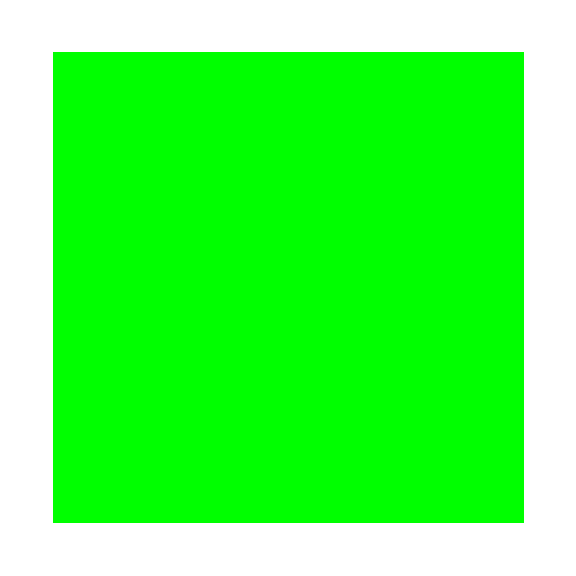

```mathematica
differences=MapThread[Not@*Equal,{CovMatrix50x30tabzSKA[[1]],Transpose[CovMatrix30x50tabzSKA[[1]]]},2];
ArrayPlot[differences,ColorRules->{True->Red,False->Green}, FrameTicks->{{Table[{i,If[Mod[i,36]==0,i,""]},{i,Length[CovMatrix50x30tabzSKA[[1]]]}],None},{Table[{i,If[Mod[i,36]==0,i,""]},{i,Length[CovMatrix50x30tabzSKA[[1]]]}],None}}, ImageSize->Large  (*Adjust the size as needed*)]
```

```mathematica
SymmetricMatrixQ[MultiSplitCovMatrixzSKA[[1]]]
```

True

```mathematica
differences=MapThread[Not@*Equal,{MultiSplitCovMatrixzSKA[[1]],Transpose[MultiSplitCovMatrixzSKA[[1]]]},2];
ArrayPlot[differences,ColorRules->{True->Red,False->Green}, FrameTicks->{{Table[{i,If[Mod[i,36]==0,i,""]},{i,Length[MultiSplitCovMatrixzSKA[[1]]]}],None},{Table[{i,If[Mod[i,36]==0,i,""]},{i,Length[MultiSplitCovMatrixzSKA[[1]]]}],None}}, ImageSize->Large  (*Adjust the size as needed*)]
```

-Graphics-

## COVARIANCE MATRIX + OCTUPOLE JOINT 10x50

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance

```mathematica
SetDirectory["octupole"]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance/octupole

```mathematica
CovMatrixOCT50Bx50FzSKA = Table[Import["CovarianceMatrixOCT_at_z"<>ToString[zSKA[[i]]]<>"_d20to160_msplit-50B_50F.txt", "Table"], {i,Length[zSKA]}];
CovMatrixOCT30Bx70FzSKA = Table[Import["CovarianceMatrixOCT_at_z"<>ToString[zSKA[[i]]]<>"_d20to160_msplit-10B_90F.txt", "Table"], {i,Length[zSKA]}];
```

```mathematica
CovMatrixOCT50Bx50FzSKA[[1,1,1]]
```

0.0000114066

```mathematica
CovMatrixOCT30Bx70FzSKA[[1,1,1]]
```

0.0000654395

```mathematica
MultiSplitCovMatrixOCTzSKA = Table[
Join[ArrayFlatten[{{CovMatrixOCT50Bx50FzSKA[[i]], CovMatrixOCT50x30tabzSKA[[i]]}}], 
ArrayFlatten[{{CovMatrixOCT30x50tabzSKA[[i]], CovMatrixOCT30Bx70FzSKA[[i]]}}]],
{i,Length[zSKA]}];
```

```mathematica
Dimensions[MultiSplitCovMatrixOCTzSKA]
```

{19,648,648}

```mathematica
MultiSplitCovMatrixOCTzSKA[[All,325;;648,325;;648]]== CovMatrixOCT30Bx70FzSKA[[All]]
MultiSplitCovMatrixOCTzSKA[[All,1;;324,325;;648]]== CovMatrixOCT50x30tabzSKA[[All]]
MultiSplitCovMatrixOCTzSKA[[All,325;;648,1;;324]]== CovMatrixOCT30x50tabzSKA[[All]]
```

True

True

True

```mathematica
SymmetricMatrixQ[CovMatrixOCT50x30tabzSKA[[1]]]
SymmetricMatrixQ[CovMatrixOCT30x50tabzSKA[[1]]]
```

False

False

```mathematica
Table[CovMatrixOCT50x30tabzSKA[[i]] ==CovMatrixOCT30x50tabzSKA[[i]],{i,1,ktot}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

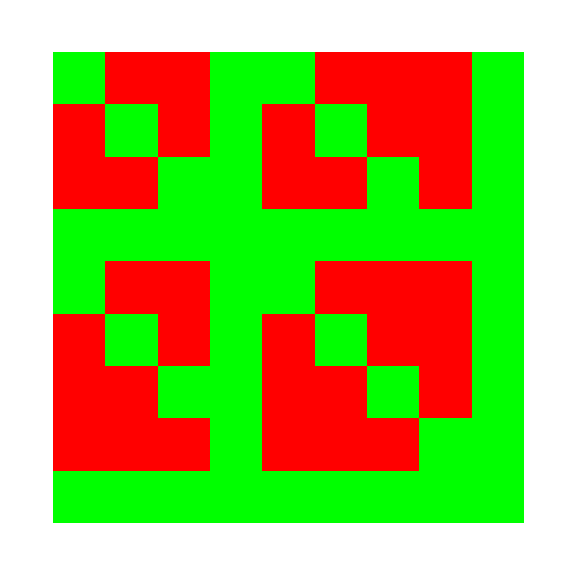

```mathematica
differences=MapThread[Not@*Equal,{CovMatrixOCT50x30tabzSKA[[1]],CovMatrixOCT30x50tabzSKA[[1]]},2];
ArrayPlot[differences,ColorRules->{True->Red,False->Green}, FrameTicks->{{Table[{i,If[Mod[i,36]==0,i,""]},{i,Length[CovMatrixOCT50x30tabzSKA[[1]]]}],None},{Table[{i,If[Mod[i,36]==0,i,""]},{i,Length[CovMatrixOCT30x50tabzSKA[[1]]]}],None}}, ImageSize->Large  (*Adjust the size as needed*)]
```

```mathematica
SymmetricMatrixQ[MultiSplitCovMatrixOCTzSKA[[1]]]
```

True

```mathematica
differences=MapThread[Not@*Equal,{MultiSplitCovMatrixOCTzSKA[[1]],Transpose[MultiSplitCovMatrixOCTzSKA[[1]]]},2];
ArrayPlot[differences,ColorRules->{True->Red,False->Green}, FrameTicks->{{Table[{i,If[Mod[i,36]==0,i,""]},{i,Length[MultiSplitCovMatrixOCTzSKA[[1]]]}],None},{Table[{i,If[Mod[i,36]==0,i,""]},{i,Length[MultiSplitCovMatrixOCTzSKA[[1]]]}],None}}, ImageSize->Large  (*Adjust the size as needed*)]
```

-Graphics-

# EXPORT

```mathematica
Dimensions[MultiSplitCovMatrixzSKA]
Dimensions[MultiSplitCovMatrixOCTzSKA]
```

{19,576,576}

{19,648,648}

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance

```mathematica
SetDirectory["multi_split"]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance/multi_split

```mathematica
For[i=1,i<= Length[zSKA],i++,
Export["CovarianceMatrix_all_50x10_at_z"<>ToString[zSKA[[i]]]<>"_d"<>ToString[distances[[indist]]]<>"to"<>ToString[distances[[maxsep]]]<>".txt",MultiSplitCovMatrixzSKA[[i]],"Table","FieldSeparators"->" ",OverwriteTarget->True]]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance

```mathematica
SetDirectory["octupole"]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance/octupole

```mathematica
For[i=1,i<= Length[zSKA],i++,
Export["CovarianceMatrixOCT_all_50x10_at_z"<>ToString[zSKA[[i]]]<>"_d"<>ToString[distances[[indist]]]<>"to"<>ToString[distances[[maxsep]]]<>".txt",MultiSplitCovMatrixOCTzSKA[[i]],"Table","FieldSeparators"->" ",OverwriteTarget->True]]
```

```mathematica
Exit[]
```